# Potential Testing for Claire

This notebook shows an example of how to load in HDF5 potential data from chplUltra and what it looks like.

```mathematica
SetDirectory[NotebookDirectory[] ];
```

### How does importing the potential work?

Below, ff opens the file “phi_ 000000.h5”, while ff[“/phi”] gets the data under the “/phi” key--aka, the 128 x 128 x 128 array of potential values.

```mathematica
ff = Import["test/saves/phi_000000.h5", "Data"];
pot = ff["/phi"] (* this is the actual data you want!*)
```

{1}
 |  |  |  |

Below, we can plot it quickly (ArrayPlot[] is not very pretty but it’s quite quick; DensityPlot[] is the version with more bells and whistles). This plots the y-z plane for the 64th x-index of pot:

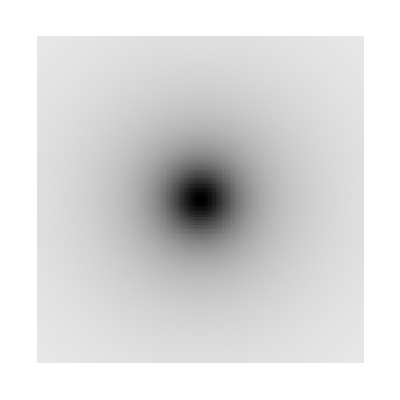

```mathematica
ArrayPlot[pot[[64,;;,;;]]]
```

We can also plot one cross section of potential as below:

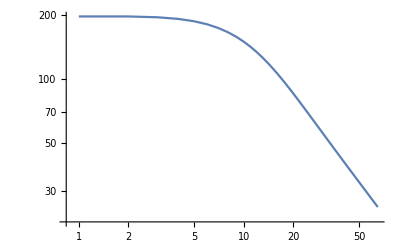

```mathematica
ListLogLogPlot[Abs@pot[[64,64,64;;]], Joined->True]
```

Note that above you’re just plotting the values of pot against numbers running from 1 to 64. If you wanted to define a radius to plot against, you could do something like this:

```mathematica
rval = (Range[0,64] +0.5)* 2.0/128;
```

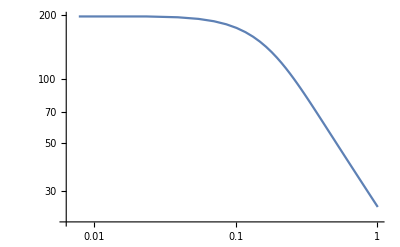

```mathematica
ListLogLogPlot[Transpose[{rval,Abs@pot[[64,64,64;;]]}], Joined->True]
```

### What is the run.h5 file?

The run.h5 file is sort of the main output of chplUltra--it has things like the evolution of the mass, the density and energy profiles, etc.

```mathematica
ff = Import["test/run.h5", "Data"];
Keys@ff
```

{/info,/profiles/000000/KEc,/profiles/000000/KEq,/profiles/000000/PE,/profiles/000000/counts,/profiles/000000/mass,/profiles/000001/KEc,/profiles/000001/KEq,/profiles/000001/PE,/profiles/000001/counts,/profiles/000001/mass,/profiles/000002/KEc,/profiles/000002/KEq,/profiles/000002/PE,/profiles/000002/counts,/profiles/000002/mass,/profiles/000003/KEc,/profiles/000003/KEq,/profiles/000003/PE,/profiles/000003/counts,/profiles/000003/mass,/profiles/000004/KEc,/profiles/000004/KEq,/profiles/000004/PE,/profiles/000004/counts,/profiles/000004/mass,/profiles/000005/KEc,/profiles/000005/KEq,/profiles/000005/PE,/profiles/000005/counts,/profiles/000005/mass,/profiles/000006/KEc,/profiles/000006/KEq,/profiles/000006/PE,/profiles/000006/counts,/profiles/000006/mass,/profiles/000007/KEc,/profiles/000007/KEq,/profiles/000007/PE,/profiles/000007/counts,/profiles/000007/mass,/profiles/000008/KEc,/profiles/000008/KEq,/profiles/000008/PE,/profiles/000008/counts,/profiles/000008/mass,/profiles/000009/KEc,/profiles/000009/KEq,/profiles/000009/PE,/profiles/000009/counts,/profiles/000009/mass,/profiles/000010/KEc,/profiles/000010/KEq,/profiles/000010/PE,/profiles/000010/counts,/profiles/000010/mass,/timing}

"Keys" are what you give ff to ask for a specific bit of information. Eg, if you wanted to know how much time each of the steps took:

```mathematica
ff["/timing"]
```

{<|kick→0.,stream→0.,pot→0.,sponge→0.,analyse→0.|>,<|kick→0.021387,stream→0.353974,pot→0.708924,sponge→0.000174,analyse→0.810269|>,<|kick→0.04251,stream→0.70321,pot→1.41164,sponge→0.000348,analyse→1.29956|>,<|kick→0.063384,stream→1.05192,pot→2.11392,sponge→0.000521,analyse→1.7646|>,<|kick→0.08438,stream→1.40097,pot→2.81625,sponge→0.00069,analyse→2.28825|>,<|kick→0.105227,stream→1.74935,pot→3.5149,sponge→0.000862,analyse→2.76687|>,<|kick→0.126181,stream→2.09756,pot→4.21805,sponge→0.001035,analyse→3.26068|>,<|kick→0.146845,stream→2.44703,pot→4.91535,sponge→0.001208,analyse→3.77778|>,<|kick→0.167488,stream→2.79581,pot→5.61542,sponge→0.001385,analyse→4.26319|>,<|kick→0.188095,stream→3.14471,pot→6.31933,sponge→0.001556,analyse→4.7534|>,<|kick→0.208651,stream→3.49287,pot→7.01879,sponge→0.001728,analyse→5.2262|>}

See an example of how to get to the DM density profiles from run.h5 below :

```mathematica
ff = Import["test/run.h5", "Data"];
rho = ff["/profiles/000000/mass"]/ff["/profiles/000000/counts"];
```

You have to remember to divide by counts, otherwise you’ll get a cumulative density instead of a density profile!

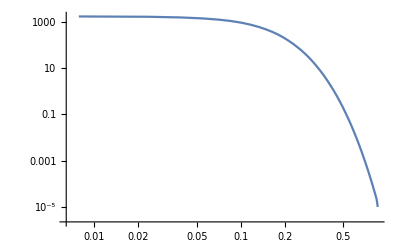

```mathematica
rval = (Range[1,64] -0.5)* 2.0/128;
ListLogLogPlot[Transpose[{rval,rho}], Joined->True]
```

### chplUltra Units

λ and m22 are constants; we tend to set them to 1.

#### Code units and conversions

```mathematica
maxion[m22_]:= (m22 10^-22)*(1.783*10^-36)  (* kg *)
hbar=1.0545718*10^-34; (* m^2 kg/s *)
parsec=3.0857*10^16 ; (* m *)
ly=9.4607*10^15 ; (* m *)
kpc = 3.086*10^19; (* m *)
mSun=1.989* 10^30; (* kg *)
G=6.673*10^-11; (*N m2 kg-2.*)
omegaM0=0.31 ;
H0=(67.7 * 10^3)/(parsec*10^6) ; (* s^-1 *)
```

#### Defining code units (in SI):

```mathematica
timeUnit[ λ_]:=((8*Pi)/(3 * H0^2* omegaM0))^(1/2)λ^-2 (*seconds*)
lengthUnit[m22_, λ_] := ((8 π hbar^2)/(3*maxion[m22]^2* H0^2*omegaM0))^(1/4)λ^-1 (*meters*)
massUnit[m22_, λ_] := 1/G((8 Pi)/(3 * H0^2*omegaM0))^(-1/4)(hbar/maxion[m22])^(3/2)λ^1 (*kg*)
```

#### Code units in “astronomical” units:

```mathematica
timeUnityears[ λ_] := timeUnit[ λ]/(Pi * 10^7) (* years *)
lengthUnitkpc[m22_, λ_] := lengthUnit[m22, λ]/kpc (* kpc *)
massUnitsolar[m22_, λ_] := massUnit[m22, λ]/mSun (* Solar masses *)
```

```mathematica
lengthUnitkpc[1,1]
```

38.3609

```mathematica
lengthUnitkpc[1,2.55739]
```

15.

```mathematica
Clear[λ]
```

```mathematica
Solve[((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)λ^-1/kpc ==15, λ]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{λ→2.55739}}

Need to calculate the lambda you want for a choice of parameters; in the meantime, posting the table below with some ideas:

-Graphics-

### Units

λ = 8.7 is equivalent to one gigayear in code units
1. timeUnit[8.7] converts a gigayear from code units to seconds
2. timeUnityears[8.7] converts a gigayear from code units to years
3.

```mathematica
timeUnit[1]
timeUnityears[1]
lengthUnit[1,1]
lengthUnitkpc[1,1]
((8 π hbar^2)/(3*maxion[1]^2* H0^2*omegaM0))^(1/4)
```

2.36943×10^18

7.54212×10^10

1.18382×10^21

38.3609

1.18382×10^21

### Run in ChplUltra units

#### 1. Dimensionless ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp1pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10,6;;7}];
bp1pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",10;;20,6;;7}];
bp1pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",100;;110,6;;7}];
bp1pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",200;;210,6;;7}];
bp1pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",300;;310,6;;7}];
bp1pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",990;;1000,6;;7}];
bp1pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1990;;2000,6;;7}];
bp1pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",2990;;3000,6;;7}];
bp1pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",3990;;4000,6;;7}];
bp1pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",4990;;5000,6;;7}];
bp1pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",5990;;6000,6;;7}];
bp1pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",6990;;7000,6;;7}];
bp1pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",7990;;8000,6;;7}];
bp1pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",8990;;9000,6;;7}];
bp1pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

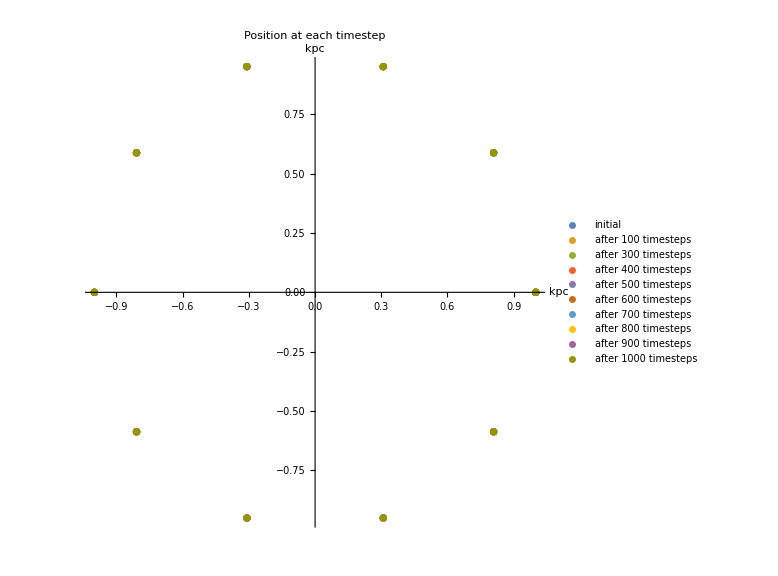

```mathematica
bp1posgraph = ListPlot[{bp1pos1,bp1pos100,bp1pos300,bp1pos400,bp1pos500,bp1pos600,bp1pos700,bp1pos800,bp1pos900,bp1pos1000},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 2. ChplUltra units NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp2pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1;;10,6;;7}];
bp2pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",10;;20,6;;7}];
bp2pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",100;;110,6;;7}];
bp2pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",200;;210,6;;7}];
bp2pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",300;;310,6;;7}];
bp2pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",990;;1000,6;;7}];
bp2pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",1990;;2000,6;;7}];
bp2pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",2990;;3000,6;;7}];
bp2pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",3990;;4000,6;;7}];
bp2pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",4990;;5000,6;;7}];
bp2pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",5990;;6000,6;;7}];
bp2pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",6990;;7000,6;;7}];
bp2pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",7990;;8000,6;;7}];
bp2pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",8990;;9000,6;;7}];
bp2pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp2.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

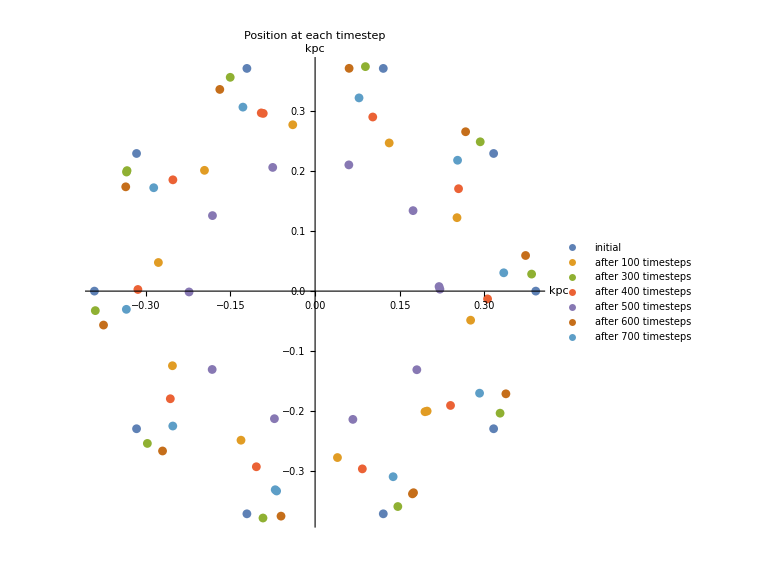

```mathematica
bp2posgraph = ListPlot[{bp2pos1,bp2pos100,bp2pos300,bp2pos400,bp2pos500,bp2pos600,bp2pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### 3. Comparing grids between ChplUltra units and dimensionless units

Import Boxes

```mathematica
box1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/nfwbox1.csv",{"Data",1;;16384,1;;128}];
Min[box1]
box2 =Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/nfwbox2.csv",{"Data",1;;16384,1;;128}];
```

Min[25.2022,nan]

```mathematica
Min[Flatten@box1]
```

Min[25.2022,nan]

Setup

```mathematica
kpckm = 1/(3.24078^(-17))
yrsec = 60*60*24*365.24
f[a_,b_]:=(a - ((b * 38.3609 *(1.94249*10^16)*(1.94249*10^16))/ ((75.4212*10^9*yrsec)^2*15) ))
diff = {}
row = {}
```

4.7978×10^8

3.15567×10^7

{}

{}

Compare Boxes

```mathematica
For[i = 1,i<129,i++,row = {};For[j=1,j<129,j++,row = Append[row,f[box1[[i]][[j]],box2[[i]][[j]]]] ];diff=Append[diff,row]]
Print[diff]
```

{{-2.91902×10^-6,0.0000222289,0.0000584291,0.0000353309,0.0000936357,0.000092642,2.70066×10^-6,-5.83767×10^-6,0.0000670271,0.0000509441,0.0000162641,0.0000629872,0.0000614642,0.000141344,2.6272×10^-6,0.0000860148,0.000121156,0.000108051,0.0000467005,7.45417×10^-6,-9.68762×10^-6,-4.72483×10^-6,0.0000926933,0.000112216,0.000124194,0.0000582767,0.0000551654,0.0000445095,0.0000966596,0.0000412652,0.000119028,0.000159596,0.000162971,0.0000291513,0.0000988396,0.000031334,0.0000673361,0.000036495,9.16154×10^-6,0.0000853357,-5.33325×10^-6,0.0000778562,0.0000645532,-0.0000452421,0.0000891718,0.000127093,0.0000388731,0.0000245114,0.000154359,-0.0000122861,0.0000356288,0.0000574022,0.0000233847,0.0000335763,0.0000879772,0.0000865871,0.0000294063,0.0000867853,0.0000180228,0.000134171,0.0000241774,0.0000287438,0.0000478702,0.0000112057,0.0000891011,0.0000112057,0.0000478702,0.0000287438,0.0000241774,0.000134171,0.0000180228,0.0000867853,0.0000294063,0.0000865871,0.0000879772,0.0000335763,0.0000233847,0.0000574022,0.0000356288,-0.0000122861,0.000154359,0.0000245114,0.0000388731,0.000127093,0.0000891718,-0.0000452421,0.0000645532,0.0000778562,-5.33325×10^-6,0.0000853357,9.16154×10^-6,0.000036495,0.0000673361,0.000031334,0.0000988396,0.0000291513,0.000162971,0.000159596,0.000119028,0.0000412652,0.0000966596,0.0000445095,0.0000551654,0.0000582767,0.000124194,0.000112216,0.0000926933,-4.72483×10^-6,-9.68762×10^-6,7.45417×10^-6,0.0000467005,0.000108051,0.000121156,0.0000860148,2.6272×10^-6,0.000141344,0.0000614642,0.0000629872,0.0000162641,0.0000509441,0.0000670271,-5.83767×10^-6,2.70066×10^-6,0.000092642,0.0000936357,0.0000353309,0.0000584291,0.0000222289},{0.0000222289,0.000095623,0.0000393679,0.0000645159,0.0000303653,7.26709×10^-6,0.0000655719,0.000134929,0.0000153384,-0.0000228492,0.0000203663,0.000115336,0.0000213572,0.0000791326,0.0000886618,-0.0000204059,0.0000926309,0.0000574216,0.000144317,0.0000829659,0.0000437195,0.0000265777,0.000101891,-6.9058×10^-7,-0.0000108171,0.0000715117,0.0000462958,0.0000838861,0.0000139317,6.78339×10^-6,0.000132792,0.0000512559,0.000102877,0.0000876543,0.000035238,0.0000863294,0.0000705776,-0.0000120173,0.0000792462,0.000103667,0.0000315946,0.000133381,0.000138675,-0.0000525234,0.000100487,-0.0000429942,0.0000577334,0.0000323194,0.000151114,0.000143768,0.0000102799,0.0000913517,-0.000053718,0.0000157721,0.0000294714,0.0000873799,0.000159848,0.0000765257,0.0000374124,0.000012859,0.000102866,0.0000370812,0.000156208,-0.0000508077,0.0000270877,-0.0000508077,0.000156208,0.0000370812,0.000102866,0.000012859,0.0000374124,0.0000765257,0.000159848,0.0000873799,0.0000294714,0.0000157721,-0.000053718,0.0000913517,0.0000102799,0.000143768,0.000151114,0.0000323194,0.0000577334,-0.0000429942,0.000100487,-0.0000525234,0.000138675,0.000133381,0.0000315946,0.000103667,0.0000792462,-0.0000120173,0.0000705776,0.0000863294,0.000035238,0.0000876543,0.000102877,0.0000512559,0.000132792,6.78339×10^-6,0.0000139317,0.0000838861,0.0000462958,0.0000715117,-0.0000108171,-6.9058×10^-7,0.000101891,0.0000265777,0.0000437195,0.0000829659,0.000144317,0.0000574216,0.0000926309,-0.0000204059,0.0000886618,0.0000791326,0.0000213572,0.000115336,0.0000203663,-0.0000228492,0.0000153384,0.000134929,0.0000655719,7.26709×10^-6,0.0000303653,0.0000645159,0.0000393679,0.000095623},{0.0000584291,0.0000393679,0.000031359,0.000134402,0.0000781473,0.0000329444,0.000169145,-0.0000539536,0.000074702,0.00011441,0.0000355208,0.0000380347,0.0000923025,-0.0000423774,0.0000450472,0.0000842257,4.80716×10^-6,-0.0000525068,0.000112284,0.0000288284,-0.0000325226,0.0000985818,0.000151791,0.0000271044,-5.12674×10^-6,0.000125448,-0.0000218722,-6.3865×10^-6,0.0000719053,0.000113003,-0.0000534436,0.0000836172,0.0000131334,0.0000461573,0.000112338,0.0000413247,0.00014417,9.8212×10^-6,0.0000493309,0.0000923482,0.0000388731,-0.0000110943,0.0000127967,0.000010546,0.0000821538,0.00012762,0.0000469444,0.000110478,0.0000478702,0.0000294714,0.0000552818,0.0000253013,0.00003953,0.000168319,-0.0000290344,0.000158523,0.0000199394,0.0000662662,0.0000568021,0.0000618979,0.0000815537,0.000115769,-5.80584×10^-6,0.0000575297,-0.0000349257,0.0000575297,-5.80584×10^-6,0.000115769,0.0000815537,0.0000618979,0.0000568021,0.0000662662,0.0000199394,0.000158523,-0.0000290344,0.000168319,0.00003953,0.0000253013,0.0000552818,0.0000294714,0.0000478702,0.000110478,0.0000469444,0.00012762,0.0000821538,0.000010546,0.0000127967,-0.0000110943,0.0000388731,0.0000923482,0.0000493309,9.8212×10^-6,0.00014417,0.0000413247,0.000112338,0.0000461573,0.0000131334,0.0000836172,-0.0000534436,0.000113003,0.0000719053,-6.3865×10^-6,-0.0000218722,0.000125448,-5.12674×10^-6,0.0000271044,0.000151791,0.0000985818,-0.0000325226,0.0000288284,0.000112284,-0.0000525068,4.80716×10^-6,0.0000842257,0.0000450472,-0.0000423774,0.0000923025,0.0000380347,0.0000355208,0.00011441,0.000074702,-0.0000539536,0.000169145,0.0000329444,0.0000781473,0.000134402,0.000031359,0.0000393679},{0.0000353309,0.0000645159,0.000134402,0.0000449904,-0.0000333693,0.000169674,0.0000134189,0.000138567,0.0000747671,0.0000923704,0.0000913767,0.0000717861,0.0000335985,0.0000471648,0.000112485,-0.000040792,0.0000280357,0.0000486172,0.0000209525,0.0000857432,0.000102288,-0.0000590633,-0.0000279589,0.0000956008,0.0000412652,0.0000497356,0.0000506613,0.0000440424,2.29626×10^-7,0.0000895737,0.0000713731,0.0000863294,-0.0000359082,0.0000453618,-0.0000105621,0.0000370216,0.000088113,0.0000723612,0.0000601171,0.0000513806,0.000116502,0.000085132,0.00012762,0.000143966,0.000134171,0.000098234,0.000106506,0.0000886368,0.0000149766,0.0000855256,2.83658×10^-7,0.000129602,0.0000327781,-0.0000494856,-0.0000171894,0.000129667,0.000120732,0.000126357,0.000146543,0.000181288,-0.0000397582,0.0000241067,0.000172882,0.000065867,-0.0000265883,0.000065867,0.000172882,0.0000241067,-0.0000397582,0.000181288,0.000146543,0.000126357,0.000120732,0.000129667,-0.0000171894,-0.0000494856,0.0000327781,0.000129602,2.83658×10^-7,0.0000855256,0.0000149766,0.0000886368,0.000106506,0.000098234,0.000134171,0.000143966,0.00012762,0.000085132,0.000116502,0.0000513806,0.0000601171,0.0000723612,0.000088113,0.0000370216,-0.0000105621,0.0000453618,-0.0000359082,0.0000863294,0.0000713731,0.0000895737,2.29626×10^-7,0.0000440424,0.0000506613,0.0000497356,0.0000412652,0.0000956008,-0.0000279589,-0.0000590633,0.000102288,0.0000857432,0.0000209525,0.0000486172,0.0000280357,-0.000040792,0.000112485,0.0000471648,0.0000335985,0.0000717861,0.0000913767,0.0000923704,0.0000747671,0.000138567,0.0000134189,0.000169674,-0.0000333693,0.0000449904,0.000134402,0.0000645159},{0.0000936357,0.0000303653,0.0000781473,-0.0000333693,0.000136517,0.000147105,0.0000687455,0.0000717889,0.0000858845,0.0000813832,0.000158285,0.00011659,0.0000562977,0.000147759,0.0000206241,0.0000452426,0.0000919657,0.0000904426,0.0000406734,0.0000130087,0.0000777994,-5.65614×10^-6,3.34367×10^-6,0.000104799,-0.0000716414,0.0000147244,-6.45441×10^-6,0.0000351729,0.000139606,0.000036495,-0.0000334594,0.000129743,0.0000557516,0.000014917,0.0000775901,0.00017342,0.000102407,0.0000349012,0.000141254,0.000151114,0.0000644826,0.000151709,0.0000424431,-0.0000226136,-0.000013812,0.0000391988,0.000066068,0.0000371463,0.0000524338,0.0000119305,0.0000156363,0.000033902,-3.6231×10^-6,-0.0000265883,0.0000650064,8.10283×10^-7,0.000121525,-0.0000135515,0.000136283,0.000100677,0.000179631,0.0000731456,-0.0000187803,-0.0000257956,0.0001521,-0.0000257956,-0.0000187803,0.0000731456,0.000179631,0.000100677,0.000136283,-0.0000135515,0.000121525,8.10283×10^-7,0.0000650064,-0.0000265883,-3.6231×10^-6,0.000033902,0.0000156363,0.0000119305,0.0000524338,0.0000371463,0.000066068,0.0000391988,-0.000013812,-0.0000226136,0.0000424431,0.000151709,0.0000644826,0.000151114,0.000141254,0.0000349012,0.000102407,0.00017342,0.0000775901,0.000014917,0.0000557516,0.000129743,-0.0000334594,0.000036495,0.000139606,0.0000351729,-6.45441×10^-6,0.0000147244,-0.0000716414,0.000104799,3.34367×10^-6,-5.65614×10^-6,0.0000777994,0.0000130087,0.0000406734,0.0000904426,0.0000919657,0.0000452426,0.0000206241,0.000147759,0.0000562977,0.00011659,0.000158285,0.0000813832,0.0000858845,0.0000717889,0.0000687455,0.000147105,0.000136517,-0.0000333693,0.0000781473,0.0000303653},{0.000092642,7.26709×10^-6,0.0000329444,0.000169674,0.000147105,0.0000355887,0.0000351244,0.000116063,0.000108054,0.0000110976,0.0000658948,0.000102095,0.000119698,0.0000187046,0.000139816,0.0000423295,-3.40272×10^-6,0.0000729696,0.000171447,0.000121677,0.0000940126,-0.0000115475,-0.0000246522,0.0000546984,0.000126504,0.0000907655,0.0000474821,0.0000670049,0.0000493337,-5.53143×10^-6,0.00017276,0.000113858,0.000088113,0.0000955246,0.000136093,0.0000801692,0.0000574022,0.000108494,-7.25823×10^-6,0.000121199,-0.0000171866,0.0000886368,0.000168319,-0.0000484919,0.000149257,-0.0000494856,0.0000663313,0.000126357,-0.0000397582,8.68617×10^-6,0.0000716904,0.0000789039,0.000100677,0.0000666597,0.000117553,0.0000126553,0.0000926683,0.0000872413,0.0000963741,0.0000200669,0.0000990211,0.0000221845,0.0000302586,0.000123243,0.000030788,0.000123243,0.0000302586,0.0000221845,0.0000990211,0.0000200669,0.0000963741,0.0000872413,0.0000926683,0.0000126553,0.000117553,0.0000666597,0.000100677,0.0000789039,0.0000716904,8.68617×10^-6,-0.0000397582,0.000126357,0.0000663313,-0.0000494856,0.000149257,-0.0000484919,0.000168319,0.0000886368,-0.0000171866,0.000121199,-7.25823×10^-6,0.000108494,0.0000574022,0.0000801692,0.000136093,0.0000955246,0.000088113,0.000113858,0.00017276,-5.53143×10^-6,0.0000493337,0.0000670049,0.0000474821,0.0000907655,0.000126504,0.0000546984,-0.0000246522,-0.0000115475,0.0000940126,0.000121677,0.000171447,0.0000729696,-3.40272×10^-6,0.0000423295,0.000139816,0.0000187046,0.000119698,0.000102095,0.0000658948,0.0000110976,0.000108054,0.000116063,0.0000351244,0.0000355887,0.000147105,0.000169674,0.0000329444,7.26709×10^-6},{2.70066×10^-6,0.0000655719,0.000169145,0.0000134189,0.0000687455,0.0000351244,0.0000125556,0.00017139,0.000141276,0.000022215,0.000154908,-1.34747×10^-6,0.0000941512,-0.000028947,-2.91448×10^-7,0.000150469,0.0000826319,-0.0000334511,0.000142921,0.0000710474,0.000121278,-6.3865×10^-6,0.0000584042,0.0000156502,0.0000653515,0.000107508,0.0000421202,0.000109889,0.0000701133,-6.85632×10^-6,0.0000493309,0.000138675,-9.17488×10^-6,0.0000464829,0.0000352976,0.00012762,0.0000530991,0.0000524366,0.0000552818,-0.0000383654,0.000112197,0.0000662662,-5.80584×10^-6,0.0000663313,0.0000123268,0.000172882,0.000107296,0.0000859191,8.7513×10^-6,0.0000461434,0.0000980954,0.0000942565,0.000104978,0.0000302586,0.00014045,0.0000948511,0.0000341626,-0.000011966,0.0000268161,0.000150509,0.0000887616,0.000111925,0.0000496482,-0.0000277178,0.000150178,-0.0000277178,0.0000496482,0.000111925,0.0000887616,0.000150509,0.0000268161,-0.000011966,0.0000341626,0.0000948511,0.00014045,0.0000302586,0.000104978,0.0000942565,0.0000980954,0.0000461434,8.7513×10^-6,0.0000859191,0.000107296,0.000172882,0.0000123268,0.0000663313,-5.80584×10^-6,0.0000662662,0.000112197,-0.0000383654,0.0000552818,0.0000524366,0.0000530991,0.00012762,0.0000352976,0.0000464829,-9.17488×10^-6,0.000138675,0.0000493309,-6.85632×10^-6,0.0000701133,0.000109889,0.0000421202,0.000107508,0.0000653515,0.0000156502,0.0000584042,-6.3865×10^-6,0.000121278,0.0000710474,0.000142921,-0.0000334511,0.0000826319,0.000150469,-2.91448×10^-7,-0.000028947,0.0000941512,-1.34747×10^-6,0.000154908,0.000022215,0.000141276,0.00017139,0.0000125556,0.0000351244,0.0000687455,0.0000134189,0.000169145,0.0000655719},{-5.83767×10^-6,0.000134929,-0.0000539536,0.000138567,0.0000717889,0.000116063,0.00017139,0.0000377686,0.0000855505,0.0000443848,-0.000015378,0.0000766131,-0.0000203436,0.0000344536,0.0000410046,-6.9058×10^-7,9.36804×10^-6,0.000141531,0.000125448,0.00013147,0.000159596,0.000109827,0.0000525128,0.0000876543,-0.0000550997,0.000135303,0.0000478106,0.0000934749,0.0000315946,0.000102871,0.0000369537,4.1932×10^-6,4.58955×10^-6,0.000108494,0.000145554,0.0000157721,0.000159848,0.0000370812,0.000158523,0.0000131223,0.0000119305,0.000084597,0.000031122,0.000121856,-0.0000135515,-4.74982×10^-6,0.000118612,0.0000861825,0.0000979623,-0.0000460487,0.0000948511,0.000150311,0.0000499795,0.0000345589,0.0000336983,0.000117748,0.000116358,0.000099879,0.0000979595,-0.0000190492,-0.0000511473,0.000172016,0.000109739,0.000132373,0.000139918,0.000132373,0.000109739,0.000172016,-0.0000511473,-0.0000190492,0.0000979595,0.000099879,0.000116358,0.000117748,0.0000336983,0.0000345589,0.0000499795,0.000150311,0.0000948511,-0.0000460487,0.0000979623,0.0000861825,0.000118612,-4.74982×10^-6,-0.0000135515,0.000121856,0.000031122,0.000084597,0.0000119305,0.0000131223,0.000158523,0.0000370812,0.000159848,0.0000157721,0.000145554,0.000108494,4.58955×10^-6,4.1932×10^-6,0.0000369537,0.000102871,0.0000315946,0.0000934749,0.0000478106,0.000135303,-0.0000550997,0.0000876543,0.0000525128,0.000109827,0.000159596,0.00013147,0.000125448,0.000141531,9.36804×10^-6,-6.9058×10^-7,0.0000410046,0.0000344536,-0.0000203436,0.0000766131,-0.000015378,0.0000443848,0.0000855505,0.0000377686,0.00017139,0.000116063,0.0000717889,0.000138567,-0.0000539536,0.000134929},{0.0000670271,0.0000153384,0.000074702,0.0000747671,0.0000858845,0.000108054,0.000141276,0.0000855505,0.0000408771,-0.0000223932,-4.26057×10^-6,-4.72483×10^-6,0.0000465647,0.0000792573,-6.64704×10^-6,0.0000295532,0.000117507,0.0000572151,0.000119028,0.000102945,-0.0000613846,0.000137092,0.000157674,3.59895×10^-7,5.85208×10^-6,3.79961×10^-6,0.0000645532,0.000088113,4.12806×10^-6,0.0000533,0.0000356288,0.000151114,0.0000294063,0.0000112057,0.0000965127,0.0000149766,0.000107299,0.0000327781,0.000102466,0.0000756623,0.0000227167,0.0000436294,8.7513×10^-6,0.000118082,1.27177×10^-6,0.0000990211,-0.0000293711,-0.0000432035,0.0000575241,0.0000728116,-0.0000676917,0.0000767156,0.0000356828,0.000179561,-0.0000323521,0.0000109964,-0.0000310952,0.000182075,0.000109805,0.000122445,0.000119996,2.45807×10^-6,0.000140181,-7.53542×10^-6,9.24247×10^-9,-7.53542×10^-6,0.000140181,2.45807×10^-6,0.000119996,0.000122445,0.000109805,0.000182075,-0.0000310952,0.0000109964,-0.0000323521,0.000179561,0.0000356828,0.0000767156,-0.0000676917,0.0000728116,0.0000575241,-0.0000432035,-0.0000293711,0.0000990211,1.27177×10^-6,0.000118082,8.7513×10^-6,0.0000436294,0.0000227167,0.0000756623,0.000102466,0.0000327781,0.000107299,0.0000149766,0.0000965127,0.0000112057,0.0000294063,0.000151114,0.0000356288,0.0000533,4.12806×10^-6,0.000088113,0.0000645532,3.79961×10^-6,5.85208×10^-6,3.59895×10^-7,0.000157674,0.000137092,-0.0000613846,0.000102945,0.000119028,0.0000572151,0.000117507,0.0000295532,-6.64704×10^-6,0.0000792573,0.0000465647,-4.72483×10^-6,-4.26057×10^-6,-0.0000223932,0.0000408771,0.0000855505,0.000141276,0.000108054,0.0000858845,0.0000747671,0.000074702,0.0000153384},{0.0000509441,-0.0000228492,0.00011441,0.0000923704,0.0000813832,0.0000110976,0.000022215,0.0000443848,-0.0000223932,-7.7682×10^-6,0.0000882599,0.0000656911,0.0000245253,0.000135113,0.0000271044,-0.0000291507,0.0000366987,0.000054302,0.0000940099,0.0000854715,0.0000693885,0.0000754101,0.000173887,-5.53143×10^-6,0.0000778562,0.0000536991,0.0000923482,0.0000938034,-0.0000122861,0.000085132,0.000145356,0.000138737,0.0000652753,0.0000249701,0.000158523,0.000125233,-4.54886×10^-6,0.0000395272,-0.000012889,0.0000789039,-0.0000257956,0.0000137141,0.0000974329,0.0000550101,-0.0000432035,0.0000731428,0.0000336983,0.000108814,0.0000281382,0.000132373,0.0000808178,0.0000141728,-0.0000379122,-5.08659×10^-6,0.0000126497,0.000115297,0.0000325037,0.000104972,-7.99968×10^-6,0.00003429,-0.0000385095,0.0000439523,0.000111325,-0.0000363919,0.0000711527,-0.0000363919,0.000111325,0.0000439523,-0.0000385095,0.00003429,-7.99968×10^-6,0.000104972,0.0000325037,0.000115297,0.0000126497,-5.08659×10^-6,-0.0000379122,0.0000141728,0.0000808178,0.000132373,0.0000281382,0.000108814,0.0000336983,0.0000731428,-0.0000432035,0.0000550101,0.0000974329,0.0000137141,-0.0000257956,0.0000789039,-0.000012889,0.0000395272,-4.54886×10^-6,0.000125233,0.000158523,0.0000249701,0.0000652753,0.000138737,0.000145356,0.000085132,-0.0000122861,0.0000938034,0.0000923482,0.0000536991,0.0000778562,-5.53143×10^-6,0.000173887,0.0000754101,0.0000693885,0.0000854715,0.0000940099,0.000054302,0.0000366987,-0.0000291507,0.0000271044,0.000135113,0.0000245253,0.0000656911,0.0000882599,-7.7682×10^-6,-0.0000223932,0.0000443848,0.000022215,0.0000110976,0.0000813832,0.0000923704,0.00011441,-0.0000228492},{0.0000162641,0.0000203663,0.0000355208,0.0000913767,0.000158285,0.0000658948,0.000154908,-0.000015378,-4.26057×10^-6,0.0000882599,0.000162183,0.0000471592,0.0000838889,2.02156×10^-6,0.000142259,0.000163899,0.000137293,0.000132792,0.0000800445,0.0000494016,0.000111214,0.000095131,1.15261×10^-6,0.00016998,0.0000609126,0.0000146509,0.0000311954,0.000010546,0.0000527027,0.000128016,0.0000661359,0.0000374124,0.000112197,0.000120138,0.000131586,0.000146543,0.0000650064,0.000157329,0.0000531586,0.0000931977,0.000107095,0.0000948511,0.0000268161,2.99025×10^-6,0.0000937243,0.0000583168,0.00010782,0.000101532,0.000109805,0.000132637,-0.0000299712,-7.66846×10^-6,-4.55024×10^-7,0.0000916691,0.0000983531,0.000160299,0.000036804,0.0000685708,-0.0000147516,0.0000571873,0.000014037,0.0000261481,0.0000935206,0.000145804,-0.0000170023,0.000145804,0.0000935206,0.0000261481,0.000014037,0.0000571873,-0.0000147516,0.0000685708,0.000036804,0.000160299,0.0000983531,0.0000916691,-4.55024×10^-7,-7.66846×10^-6,-0.0000299712,0.000132637,0.000109805,0.000101532,0.00010782,0.0000583168,0.0000937243,2.99025×10^-6,0.0000268161,0.0000948511,0.000107095,0.0000931977,0.0000531586,0.000157329,0.0000650064,0.000146543,0.000131586,0.000120138,0.000112197,0.0000374124,0.0000661359,0.000128016,0.0000527027,0.000010546,0.0000311954,0.0000146509,0.0000609126,0.00016998,1.15261×10^-6,0.000095131,0.000111214,0.0000494016,0.0000800445,0.000132792,0.000137293,0.000163899,0.000142259,2.02156×10^-6,0.0000838889,0.0000471592,0.000162183,0.0000882599,-4.26057×10^-6,-0.000015378,0.000154908,0.0000658948,0.000158285,0.0000913767,0.0000355208,0.0000203663},{0.0000629872,0.000115336,0.0000380347,0.0000717861,0.00011659,0.000102095,-1.34747×10^-6,0.0000766131,-4.72483×10^-6,0.0000656911,0.0000471592,0.000180381,0.0000246555,0.0000206836,0.0000684656,0.0000680013,0.000119291,0.0000223342,0.0000474821,-5.26534×10^-6,-0.0000359082,0.0000259042,9.8212×10^-6,0.0000565443,0.000025372,-0.0000429942,0.0000514457,8.69172×10^-6,0.0000287438,0.0000819528,0.000168319,0.0000174906,0.0000701702,0.000126357,0.0000157014,0.0000789039,0.000045614,0.0000861825,0.0000302586,0.0000185438,0.0000806875,0.0000870403,0.000137602,0.000132373,0.0000713537,-0.0000454569,0.0000226432,0.0000349525,0.0000321724,0.0000439523,0.000140643,0.000151893,0.000148054,0.000129126,0.0000951088,0.000046002,0.0000521566,0.000043222,-0.0000104513,0.0000911369,0.0000776358,0.0000193961,0.000116418,0.000168701,5.89501×10^-6,0.000168701,0.000116418,0.0000193961,0.0000776358,0.0000911369,-0.0000104513,0.000043222,0.0000521566,0.000046002,0.0000951088,0.000129126,0.000148054,0.000151893,0.000140643,0.0000439523,0.0000321724,0.0000349525,0.0000226432,-0.0000454569,0.0000713537,0.000132373,0.000137602,0.0000870403,0.0000806875,0.0000185438,0.0000302586,0.0000861825,0.000045614,0.0000789039,0.0000157014,0.000126357,0.0000701702,0.0000174906,0.000168319,0.0000819528,0.0000287438,8.69172×10^-6,0.0000514457,-0.0000429942,0.000025372,0.0000565443,9.8212×10^-6,0.0000259042,-0.0000359082,-5.26534×10^-6,0.0000474821,0.0000223342,0.000119291,0.0000680013,0.0000684656,0.0000206836,0.0000246555,0.000180381,0.0000471592,0.0000656911,-4.72483×10^-6,0.0000766131,-1.34747×10^-6,0.000102095,0.00011659,0.0000717861,0.0000380347,0.000115336},{0.0000614642,0.0000213572,0.0000923025,0.0000335985,0.0000562977,0.000119698,0.0000941512,-0.0000203436,0.0000465647,0.0000245253,0.0000838889,0.0000246555,0.0000468252,0.0000207488,0.000146426,0.0000535065,0.0000826915,0.0000636303,0.000166674,0.0000214708,-0.0000312767,0.000108431,0.0000702436,0.0000245114,0.000141585,0.000151114,0.0000530991,-0.0000117595,-0.000013812,0.0000172924,0.0000815537,0.0000789718,9.54679×10^-6,0.0000436294,-0.0000187803,0.0000926683,0.000107625,0.0000260885,0.0000887616,0.000125293,0.0000356828,-9.71816×10^-6,0.000159441,2.45807×10^-6,0.0000600353,0.0000321724,0.00011887,0.000120126,0.000135943,-0.0000336798,0.0000519585,0.0000521566,-0.0000627345,0.0000776358,0.000102917,0.0000131084,0.0000785616,0.0000992761,4.90135×10^-6,-0.000034212,0.000152287,0.000123696,0.0000503675,0.0000322999,0.0000398446,0.0000322999,0.0000503675,0.000123696,0.000152287,-0.000034212,4.90135×10^-6,0.0000992761,0.0000785616,0.0000131084,0.000102917,0.0000776358,-0.0000627345,0.0000521566,0.0000519585,-0.0000336798,0.000135943,0.000120126,0.00011887,0.0000321724,0.0000600353,2.45807×10^-6,0.000159441,-9.71816×10^-6,0.0000356828,0.000125293,0.0000887616,0.0000260885,0.000107625,0.0000926683,-0.0000187803,0.0000436294,9.54679×10^-6,0.0000789718,0.0000815537,0.0000172924,-0.000013812,-0.0000117595,0.0000530991,0.000151114,0.000141585,0.0000245114,0.0000702436,0.000108431,-0.0000312767,0.0000214708,0.000166674,0.0000636303,0.0000826915,0.0000535065,0.000146426,0.0000207488,0.0000468252,0.0000246555,0.0000838889,0.0000245253,0.0000465647,-0.0000203436,0.0000941512,0.000119698,0.0000562977,0.0000335985,0.0000923025,0.0000213572},{0.000141344,0.0000791326,-0.0000423774,0.0000471648,0.000147759,0.0000187046,-0.000028947,0.0000344536,0.0000792573,0.000135113,2.02156×10^-6,0.0000206836,0.0000207488,0.000172568,0.00010579,0.0000907655,0.0000274952,0.0000863294,-3.0826×10^-6,0.0000999608,-0.0000452421,0.0000723612,0.000112069,0.000144232,0.0000688508,0.0000562755,0.000106506,-0.0000508077,0.000095386,0.000104386,0.000146543,0.000121856,0.000100677,0.0000126553,0.0000984917,0.0000878358,0.0000806875,0.000117748,0.0000583168,0.0000430945,0.0000720813,0.000145277,-7.66846×10^-6,0.000124297,0.000100471,0.0000208541,0.0000261481,0.000046002,0.0000507666,-0.0000299089,0.000144677,0.000033823,0.0000782303,0.000107548,0.000021777,-8.73281×10^-6,0.00018637,-3.9682×10^-6,0.0000313063,0.0000218422,0.00013799,0.0000390491,0.0000657201,0.000147653,0.0000848465,0.000147653,0.0000657201,0.0000390491,0.00013799,0.0000218422,0.0000313063,-3.9682×10^-6,0.00018637,-8.73281×10^-6,0.000021777,0.000107548,0.0000782303,0.000033823,0.000144677,-0.0000299089,0.0000507666,0.000046002,0.0000261481,0.0000208541,0.000100471,0.000124297,-7.66846×10^-6,0.000145277,0.0000720813,0.0000430945,0.0000583168,0.000117748,0.0000806875,0.0000878358,0.0000984917,0.0000126553,0.000100677,0.000121856,0.000146543,0.000104386,0.000095386,-0.0000508077,0.000106506,0.0000562755,0.0000688508,0.000144232,0.000112069,0.0000723612,-0.0000452421,0.0000999608,-3.0826×10^-6,0.0000863294,0.0000274952,0.0000907655,0.00010579,0.000172568,0.0000207488,0.0000206836,2.02156×10^-6,0.000135113,0.0000792573,0.0000344536,-0.000028947,0.0000187046,0.000147759,0.0000471648,-0.0000423774,0.0000791326},{2.6272×10^-6,0.0000886618,0.0000450472,0.000112485,0.0000206241,0.000139816,-2.91448×10^-7,0.0000410046,-6.64704×10^-6,0.0000271044,0.000142259,0.0000684656,0.000146426,0.00010579,-0.0000534436,9.42762×10^-6,0.0000240527,0.000160782,0.0000492657,0.0000598538,-7.45363×10^-6,0.0000176943,0.0000352976,0.000145356,0.0000478702,0.00011319,-0.0000290344,0.0000618979,0.0000156363,0.000172882,0.0000929344,0.0000461434,2.85998×10^-6,0.0000630842,0.0000268161,0.0000644063,5.50421×10^-6,0.0000204605,0.0000796259,0.0000126497,0.0000898827,0.000111325,-0.0000230239,0.0000571873,0.0000519585,0.00016129,0.00018518,0.0000236313,0.0000469929,0.0000552651,-0.0000515519,0.0000968924,0.000130247,0.0000485132,0.0000220404,0.00012118,0.00010523,0.0000445413,0.0000391142,0.0000592994,0.000034746,0.0000358048,0.000092125,0.0000740575,0.000111251,0.0000740575,0.000092125,0.0000358048,0.000034746,0.0000592994,0.0000391142,0.0000445413,0.00010523,0.00012118,0.0000220404,0.0000485132,0.000130247,0.0000968924,-0.0000515519,0.0000552651,0.0000469929,0.0000236313,0.00018518,0.00016129,0.0000519585,0.0000571873,-0.0000230239,0.000111325,0.0000898827,0.0000126497,0.0000796259,0.0000204605,5.50421×10^-6,0.0000644063,0.0000268161,0.0000630842,2.85998×10^-6,0.0000461434,0.0000929344,0.000172882,0.0000156363,0.0000618979,-0.0000290344,0.00011319,0.0000478702,0.000145356,0.0000352976,0.0000176943,-7.45363×10^-6,0.0000598538,0.0000492657,0.000160782,0.0000240527,9.42762×10^-6,-0.0000534436,0.00010579,0.000146426,0.0000684656,0.000142259,0.0000271044,-6.64704×10^-6,0.0000410046,-2.91448×10^-7,0.000139816,0.0000206241,0.000112485,0.0000450472,0.0000886618},{0.0000860148,-0.0000204059,0.0000842257,-0.000040792,0.0000452426,0.0000423295,0.000150469,-6.9058×10^-7,0.0000295532,-0.0000291507,0.000163899,0.0000680013,0.0000535065,0.0000907655,9.42762×10^-6,0.000150194,-0.000027636,0.0000166383,-0.0000169828,0.0000715006,0.0000820886,0.000085132,0.0000102799,0.000098234,0.0000786433,-0.0000484919,0.0000575297,0.000126357,0.0000579912,0.0000227818,0.0000207293,0.0000221845,-0.0000432035,0.0000652669,6.89423×10^-6,0.0000927307,0.000182075,0.000145277,0.0000823381,-0.0000363919,-0.0000109128,0.000129126,0.000113375,0.0000418319,0.0001552,0.0000127772,0.0000552651,0.0000826637,0.000094973,0.0000218422,3.97281×10^-6,0.0000413649,0.0000636676,0.0000412318,0.0000740575,0.0000621446,0.000105493,0.000174454,0.000198676,0.0000781597,0.0000832555,0.0000139635,0.000170284,0.0000818655,0.0000190594,0.0000818655,0.000170284,0.0000139635,0.0000832555,0.0000781597,0.000198676,0.000174454,0.000105493,0.0000621446,0.0000740575,0.0000412318,0.0000636676,0.0000413649,3.97281×10^-6,0.0000218422,0.000094973,0.0000826637,0.0000552651,0.0000127772,0.0001552,0.0000418319,0.000113375,0.000129126,-0.0000109128,-0.0000363919,0.0000823381,0.000145277,0.000182075,0.0000927307,6.89423×10^-6,0.0000652669,-0.0000432035,0.0000221845,0.0000207293,0.0000227818,0.0000579912,0.000126357,0.0000575297,-0.0000484919,0.0000786433,0.000098234,0.0000102799,0.000085132,0.0000820886,0.0000715006,-0.0000169828,0.0000166383,-0.000027636,0.000150194,9.42762×10^-6,0.0000907655,0.0000535065,0.0000680013,0.000163899,-0.0000291507,0.0000295532,-6.9058×10^-7,0.000150469,0.0000423295,0.0000452426,-0.000040792,0.0000842257,-0.0000204059},{0.000121156,0.0000926309,4.80716×10^-6,0.0000280357,0.0000919657,-3.40272×10^-6,0.0000826319,9.36804×10^-6,0.000117507,0.0000366987,0.000137293,0.000119291,0.0000826915,0.0000274952,0.0000240527,-0.000027636,0.00014278,-5.40116×10^-6,0.0000388731,0.0000349012,0.0000233847,-0.0000660273,0.000107367,0.000102866,0.0000611703,0.0000119305,0.0000958475,-0.0000277802,0.0001521,0.0000947859,-0.0000293711,0.0000499795,0.000132838,-0.0000511473,0.000109077,2.45807×10^-6,0.0000400483,0.000051497,0.000036804,-0.0000336798,0.000110396,0.0000283308,0.000131176,0.0000782303,0.0000398446,0.00018637,0.000147454,0.0000934499,0.000124356,0.000040173,0.000111251,0.000137591,0.0000488416,0.0000153535,0.000107478,0.000154863,0.0000575102,0.0000857694,0.0000692901,-0.000021577,0.000013168,-0.0000264747,-0.0000405052,-0.0000289235,8.27038×10^-6,-0.0000289235,-0.0000405052,-0.0000264747,0.000013168,-0.000021577,0.0000692901,0.0000857694,0.0000575102,0.000154863,0.000107478,0.0000153535,0.0000488416,0.000137591,0.000111251,0.000040173,0.000124356,0.0000934499,0.000147454,0.00018637,0.0000398446,0.0000782303,0.000131176,0.0000283308,0.000110396,-0.0000336798,0.000036804,0.000051497,0.0000400483,2.45807×10^-6,0.000109077,-0.0000511473,0.000132838,0.0000499795,-0.0000293711,0.0000947859,0.0001521,-0.0000277802,0.0000958475,0.0000119305,0.0000611703,0.000102866,0.000107367,-0.0000660273,0.0000233847,0.0000349012,0.0000388731,-5.40116×10^-6,0.00014278,-0.000027636,0.0000240527,0.0000274952,0.0000826915,0.000119291,0.000137293,0.0000366987,0.000117507,9.36804×10^-6,0.0000826319,-3.40272×10^-6,0.0000919657,0.0000280357,4.80716×10^-6,0.0000926309},{0.000108051,0.0000574216,-0.0000525068,0.0000486172,0.0000904426,0.0000729696,-0.0000334511,0.000141531,0.0000572151,0.000054302,0.000132792,0.0000223342,0.0000636303,0.0000863294,0.000160782,0.0000166383,-5.40116×10^-6,0.000094664,0.0000464829,0.0000204065,0.0000867853,0.000175269,0.000156208,0.000129602,-4.54886×10^-6,0.0000241067,0.0000859191,0.0000401869,0.0000979623,0.0000185438,-0.0000277178,0.000099879,-9.71816×10^-6,-0.0000454569,0.0000926628,0.00003429,0.000120126,9.47055×10^-6,0.000113375,0.0000911369,0.0000131084,0.0000496399,0.000100731,-3.9682×10^-6,-0.000023757,0.0000413649,0.0000210467,-0.0000143608,0.000105493,0.000110258,0.000170284,0.0000152205,0.0000857694,0.0000412291,0.0000223009,0.0000289849,-9.06959×10^-6,0.000148839,0.000162009,0.000100791,0.000165185,0.0000551917,0.0000708104,0.0000823921,0.000119586,0.0000823921,0.0000708104,0.0000551917,0.000165185,0.000100791,0.000162009,0.000148839,-9.06959×10^-6,0.0000289849,0.0000223009,0.0000412291,0.0000857694,0.0000152205,0.000170284,0.000110258,0.000105493,-0.0000143608,0.0000210467,0.0000413649,-0.000023757,-3.9682×10^-6,0.000100731,0.0000496399,0.0000131084,0.0000911369,0.000113375,9.47055×10^-6,0.000120126,0.00003429,0.0000926628,-0.0000454569,-9.71816×10^-6,0.000099879,-0.0000277178,0.0000185438,0.0000979623,0.0000401869,0.0000859191,0.0000241067,-4.54886×10^-6,0.000129602,0.000156208,0.000175269,0.0000867853,0.0000204065,0.0000464829,0.000094664,-5.40116×10^-6,0.0000166383,0.000160782,0.0000863294,0.0000636303,0.0000223342,0.000132792,0.000054302,0.0000572151,0.000141531,-0.0000334511,0.0000729696,0.0000904426,0.0000486172,-0.0000525068,0.0000574216},{0.0000467005,0.000144317,0.000112284,0.0000209525,0.0000406734,0.000171447,0.000142921,0.000125448,0.000119028,0.0000940099,0.0000800445,0.0000474821,0.000166674,-3.0826×10^-6,0.0000492657,-0.0000169828,0.0000388731,0.0000464829,0.0000761973,0.000128016,0.00010194,0.000168319,0.0000568021,0.000108092,0.0000518365,-0.0000416125,0.0000980954,0.0000302586,-4.42137×10^-6,0.0000644063,-3.95988×10^-6,0.000101532,0.000140181,0.0000823381,0.0000983531,0.0000882266,0.0000519585,-0.0000104513,-0.0000286519,0.000167707,0.0000379252,0.0000227028,0.0000220404,0.000106289,0.000034746,0.000118465,0.0000167436,0.000170284,0.000108735,0.0000320962,0.0000107192,0.000114954,0.0000744511,0.0000892092,0.000129579,0.0000252112,-0.0000535448,0.0000636621,0.0000361305,0.000104562,0.0000986053,0.0000182611,0.0000338798,-0.0000248893,0.0000123046,-0.0000248893,0.0000338798,0.0000182611,0.0000986053,0.000104562,0.0000361305,0.0000636621,-0.0000535448,0.0000252112,0.000129579,0.0000892092,0.0000744511,0.000114954,0.0000107192,0.0000320962,0.000108735,0.000170284,0.0000167436,0.000118465,0.000034746,0.000106289,0.0000220404,0.0000227028,0.0000379252,0.000167707,-0.0000286519,-0.0000104513,0.0000519585,0.0000882266,0.0000983531,0.0000823381,0.000140181,0.000101532,-3.95988×10^-6,0.0000644063,-4.42137×10^-6,0.0000302586,0.0000980954,-0.0000416125,0.0000518365,0.000108092,0.0000568021,0.000168319,0.00010194,0.000128016,0.0000761973,0.0000464829,0.0000388731,-0.0000169828,0.0000492657,-3.0826×10^-6,0.000166674,0.0000474821,0.0000800445,0.0000940099,0.000119028,0.000125448,0.000142921,0.000171447,0.0000406734,0.0000209525,0.000112284,0.000144317},{7.45417×10^-6,0.0000829659,0.0000288284,0.0000857432,0.0000130087,0.000121677,0.0000710474,0.00013147,0.000102945,0.0000854715,0.0000494016,-5.26534×10^-6,0.0000214708,0.0000999608,0.0000598538,0.0000715006,0.0000349012,0.0000204065,0.000128016,0.0000873799,0.0000391988,0.0000131223,0.000049852,8.68617×10^-6,0.000100677,0.0000147729,0.000132376,0.0000424348,-0.0000143497,0.000132373,0.0000419026,0.00012529,0.0000418347,0.000132238,0.0000261481,-6.08303×10^-6,5.89501×10^-6,-8.26855×10^-6,0.000021777,-3.9682×10^-6,0.0000848465,0.000188221,0.0000358048,0.0000682992,0.0000153535,-0.0000526814,0.000134545,-0.0000636686,0.00006373,0.0000760393,0.00004361,0.000136793,0.000185237,0.0000889431,0.0000182611,0.000143542,0.0000240845,0.00010059,0.000102708,0.0000304373,0.0000541301,0.000173786,0.000119054,0.0000602847,0.0000271279,0.0000602847,0.000119054,0.000173786,0.0000541301,0.0000304373,0.000102708,0.00010059,0.0000240845,0.000143542,0.0000182611,0.0000889431,0.000185237,0.000136793,0.00004361,0.0000760393,0.00006373,-0.0000636686,0.000134545,-0.0000526814,0.0000153535,0.0000682992,0.0000358048,0.000188221,0.0000848465,-3.9682×10^-6,0.000021777,-8.26855×10^-6,5.89501×10^-6,-6.08303×10^-6,0.0000261481,0.000132238,0.0000418347,0.00012529,0.0000419026,0.000132373,-0.0000143497,0.0000424348,0.000132376,0.0000147729,0.000100677,8.68617×10^-6,0.000049852,0.0000131223,0.0000391988,0.0000873799,0.000128016,0.0000204065,0.0000349012,0.0000715006,0.0000598538,0.0000999608,0.0000214708,-5.26534×10^-6,0.0000494016,0.0000854715,0.000102945,0.00013147,0.0000710474,0.000121677,0.0000130087,0.0000857432,0.0000288284,0.0000829659},{-9.68762×10^-6,0.0000437195,-0.0000325226,0.000102288,0.0000777994,0.0000940126,0.000121278,0.000159596,-0.0000613846,0.0000693885,0.000111214,-0.0000359082,-0.0000312767,-0.0000452421,-7.45363×10^-6,0.0000820886,0.0000233847,0.0000867853,0.00010194,0.0000391988,0.000168913,0.000120732,0.0000650064,1.73604×10^-6,1.27177×10^-6,0.0000636136,0.0000887616,0.0000767156,-2.1735×10^-6,0.000122445,0.00018022,0.0000711527,0.000135943,0.000104242,0.000146398,-7.93733×10^-6,0.000152287,0.00018637,-5.68945×10^-6,0.000187162,0.0000538723,0.000105493,0.0000716738,0.0000524144,0.0000180657,-0.0000313723,0.0000744511,0.000165185,0.0000408299,0.0000420869,0.0000986053,0.0000103852,0.000118128,0.0000107816,-6.01947×10^-7,0.0000136267,0.000123818,0.000159622,0.0000210384,-0.0000215826,0.0000317594,0.0000810644,0.000126332,0.0000972125,0.000134406,0.0000972125,0.000126332,0.0000810644,0.0000317594,-0.0000215826,0.0000210384,0.000159622,0.000123818,0.0000136267,-6.01947×10^-7,0.0000107816,0.000118128,0.0000103852,0.0000986053,0.0000420869,0.0000408299,0.000165185,0.0000744511,-0.0000313723,0.0000180657,0.0000524144,0.0000716738,0.000105493,0.0000538723,0.000187162,-5.68945×10^-6,0.00018637,0.000152287,-7.93733×10^-6,0.000146398,0.000104242,0.000135943,0.0000711527,0.00018022,0.000122445,-2.1735×10^-6,0.0000767156,0.0000887616,0.0000636136,1.27177×10^-6,1.73604×10^-6,0.0000650064,0.000120732,0.000168913,0.0000391988,0.00010194,0.0000867853,0.0000233847,0.0000820886,-7.45363×10^-6,-0.0000452421,-0.0000312767,-0.0000359082,0.000111214,0.0000693885,-0.0000613846,0.000159596,0.000121278,0.0000940126,0.0000777994,0.000102288,-0.0000325226,0.0000437195},{-4.72483×10^-6,0.0000265777,0.0000985818,-0.0000590633,-5.65614×10^-6,-0.0000115475,-6.3865×10^-6,0.000109827,0.000137092,0.0000754101,0.000095131,0.0000259042,0.000108431,0.0000723612,0.0000176943,0.000085132,-0.0000660273,0.000175269,0.000168319,0.0000131223,0.000120732,0.000150446,0.000172616,0.0000872413,-5.67835×10^-6,0.0000345589,0.000137602,3.45174×10^-6,2.45807×10^-6,0.000104972,0.000140643,9.47055×10^-6,0.0000521566,0.000168701,0.0000887532,0.0000826637,0.000120783,0.0000327614,0.0000592994,0.0000300465,0.0000153535,0.0000152205,0.0000296474,0.0000289849,0.000113233,0.0000823921,0.0000364617,0.0000457927,0.0000103852,0.00010059,-0.0000242947,0.000146784,0.0000731234,0.0000250754,0.0000729904,0.000146518,0.0000456569,0.0000407592,0.0000318246,0.0000188528,0.000101844,0.0000807983,0.000155716,0.0000265957,-6.56118×10^-6,0.0000265957,0.000155716,0.0000807983,0.000101844,0.0000188528,0.0000318246,0.0000407592,0.0000456569,0.000146518,0.0000729904,0.0000250754,0.0000731234,0.000146784,-0.0000242947,0.00010059,0.0000103852,0.0000457927,0.0000364617,0.0000823921,0.000113233,0.0000289849,0.0000296474,0.0000152205,0.0000153535,0.0000300465,0.0000592994,0.0000327614,0.000120783,0.0000826637,0.0000887532,0.000168701,0.0000521566,9.47055×10^-6,0.000140643,0.000104972,2.45807×10^-6,3.45174×10^-6,0.000137602,0.0000345589,-5.67835×10^-6,0.0000872413,0.000172616,0.000150446,0.000120732,0.0000131223,0.000168319,0.000175269,-0.0000660273,0.000085132,0.0000176943,0.0000723612,0.000108431,0.0000259042,0.000095131,0.0000754101,0.000137092,0.000109827,-6.3865×10^-6,-0.0000115475,-5.65614×10^-6,-0.0000590633,0.0000985818,0.0000265777},{0.0000926933,0.000101891,0.000151791,-0.0000279589,3.34367×10^-6,-0.0000246522,0.0000584042,0.0000525128,0.000157674,0.000173887,1.15261×10^-6,9.8212×10^-6,0.0000702436,0.000112069,0.0000352976,0.0000102799,0.000107367,0.000156208,0.0000568021,0.000049852,0.0000650064,0.000172616,2.33058×10^-6,0.0000948511,0.000150178,0.0000979595,0.0000788983,0.0000226432,-4.55024×10^-7,0.000179954,0.0000935206,-0.0000597563,0.000131176,0.0000552651,0.000123563,0.0000657201,0.0000817352,0.00011231,0.0000167436,0.0000357369,0.0000692901,0.0000174032,0.0000504271,-1.9892×10^-6,0.000100856,0.0000182611,0.0000612784,0.0000892064,0.000142747,-0.0000188025,0.000115611,5.2866×10^-6,0.000190925,0.0000318246,0.0000686872,0.000101513,-0.0000400493,0.0000847023,0.0000350661,0.000151744,-5.96664×10^-6,0.000172988,0.000077554,0.000148434,0.0000152773,0.000148434,0.000077554,0.000172988,-5.96664×10^-6,0.000151744,0.0000350661,0.0000847023,-0.0000400493,0.000101513,0.0000686872,0.0000318246,0.000190925,5.2866×10^-6,0.000115611,-0.0000188025,0.000142747,0.0000892064,0.0000612784,0.0000182611,0.000100856,-1.9892×10^-6,0.0000504271,0.0000174032,0.0000692901,0.0000357369,0.0000167436,0.00011231,0.0000817352,0.0000657201,0.000123563,0.0000552651,0.000131176,-0.0000597563,0.0000935206,0.000179954,-4.55024×10^-7,0.0000226432,0.0000788983,0.0000979595,0.000150178,0.0000948511,2.33058×10^-6,0.000172616,0.0000650064,0.000049852,0.0000568021,0.000156208,0.000107367,0.0000102799,0.0000352976,0.000112069,0.0000702436,9.8212×10^-6,1.15261×10^-6,0.000173887,0.000157674,0.0000525128,0.0000584042,-0.0000246522,3.34367×10^-6,-0.0000279589,0.000151791,0.000101891},{0.000112216,-6.9058×10^-7,0.0000271044,0.0000956008,0.000104799,0.0000546984,0.0000156502,0.0000876543,3.59895×10^-7,-5.53143×10^-6,0.00016998,0.0000565443,0.0000245114,0.000144232,0.000145356,0.000098234,0.000102866,0.000129602,0.000108092,8.68617×10^-6,1.73604×10^-6,0.0000872413,0.0000948511,0.0000652669,0.0000281382,-0.0000461845,0.0000126497,0.00003429,-0.0000109128,0.000047392,0.0000388537,0.000033823,0.0000322999,0.000174986,0.00012118,0.0000412318,0.000105493,0.0000139635,-0.0000333569,0.0000338826,0.000015682,0.0000823921,0.0000636621,0.000129843,0.0000809341,0.0000169362,0.0000785505,0.0000250754,0.0000972125,0.000194962,0.000147973,0.0000265957,0.000201182,0.0000310291,0.0000271902,0.000119314,0.0000370507,0.000121101,0.000101114,0.0000770897,-0.0000509713,0.000157632,0.000162199,0.000062728,0.0000295711,0.000062728,0.000162199,0.000157632,-0.0000509713,0.0000770897,0.000101114,0.000121101,0.0000370507,0.000119314,0.0000271902,0.0000310291,0.000201182,0.0000265957,0.000147973,0.000194962,0.0000972125,0.0000250754,0.0000785505,0.0000169362,0.0000809341,0.000129843,0.0000636621,0.0000823921,0.000015682,0.0000338826,-0.0000333569,0.0000139635,0.000105493,0.0000412318,0.00012118,0.000174986,0.0000322999,0.000033823,0.0000388537,0.000047392,-0.0000109128,0.00003429,0.0000126497,-0.0000461845,0.0000281382,0.0000652669,0.0000948511,0.0000872413,1.73604×10^-6,8.68617×10^-6,0.000108092,0.000129602,0.000102866,0.000098234,0.000145356,0.000144232,0.0000245114,0.0000565443,0.00016998,-5.53143×10^-6,3.59895×10^-7,0.0000876543,0.0000156502,0.0000546984,0.000104799,0.0000956008,0.0000271044,-6.9058×10^-7},{0.000124194,-0.0000108171,-5.12674×10^-6,0.0000412652,-0.0000716414,0.000126504,0.0000653515,-0.0000550997,5.85208×10^-6,0.0000778562,0.0000609126,0.000025372,0.000141585,0.0000688508,0.0000478702,0.0000786433,0.0000611703,-4.54886×10^-6,0.0000518365,0.000100677,1.27177×10^-6,-5.67835×10^-6,0.000150178,0.0000281382,-0.0000310952,0.000142828,9.20724×10^-6,8.74297×10^-6,-0.0000585644,0.0000776358,0.0000469929,0.0000198576,0.0000665807,0.000187162,0.000111251,0.0000795497,0.0000920571,-0.000021577,0.000149699,0.000165185,0.0000952308,0.0000398363,0.000139703,0.0000541301,0.000123818,-0.0000215826,0.000158629,0.0000237505,0.000184835,0.000201182,-0.0000272106,0.000110711,3.8938×10^-6,0.00016339,0.0000484993,0.0000295711,0.000176957,-0.0000500455,0.0000596167,0.000165242,0.0000668302,0.000105083,0.0000392985,0.0000398279,6.67107×10^-6,0.0000398279,0.0000392985,0.000105083,0.0000668302,0.000165242,0.0000596167,-0.0000500455,0.000176957,0.0000295711,0.0000484993,0.00016339,3.8938×10^-6,0.000110711,-0.0000272106,0.000201182,0.000184835,0.0000237505,0.000158629,-0.0000215826,0.000123818,0.0000541301,0.000139703,0.0000398363,0.0000952308,0.000165185,0.000149699,-0.000021577,0.0000920571,0.0000795497,0.000111251,0.000187162,0.0000665807,0.0000198576,0.0000469929,0.0000776358,-0.0000585644,8.74297×10^-6,9.20724×10^-6,0.000142828,-0.0000310952,0.0000281382,0.000150178,-5.67835×10^-6,1.27177×10^-6,0.000100677,0.0000518365,-4.54886×10^-6,0.0000611703,0.0000786433,0.0000478702,0.0000688508,0.000141585,0.000025372,0.0000609126,0.0000778562,5.85208×10^-6,-0.0000550997,0.0000653515,0.000126504,-0.0000716414,0.0000412652,-5.12674×10^-6,-0.0000108171},{0.0000582767,0.0000715117,0.000125448,0.0000497356,0.0000147244,0.0000907655,0.000107508,0.000135303,3.79961×10^-6,0.0000536991,0.0000146509,-0.0000429942,0.000151114,0.0000562755,0.00011319,-0.0000484919,0.0000119305,0.0000241067,-0.0000416125,0.0000147729,0.0000636136,0.0000345589,0.0000979595,-0.0000461845,0.000142828,0.000124297,0.0000685708,0.000046002,0.000126941,0.0000706857,0.000088289,0.0000390491,0.0000636676,0.0000621446,0.00013448,0.0000806736,-0.0000289235,0.0000760393,0.0000252112,0.0000889431,-0.0000327651,0.0000304373,0.0000785505,0.000111574,0.0000295088,0.000173055,0.000101513,0.0000555825,-0.0000350865,0.0000702075,0.000101114,0.000157632,-0.0000602372,-0.0000117928,0.0000326145,0.0000729848,9.31808×10^-6,0.000182316,-0.0000190742,0.0001162,-0.0000525623,0.0000153397,0.000149555,-0.000020266,0.0000465771,-0.000020266,0.000149555,0.0000153397,-0.0000525623,0.0001162,-0.0000190742,0.000182316,9.31808×10^-6,0.0000729848,0.0000326145,-0.0000117928,-0.0000602372,0.000157632,0.000101114,0.0000702075,-0.0000350865,0.0000555825,0.000101513,0.000173055,0.0000295088,0.000111574,0.0000785505,0.0000304373,-0.0000327651,0.0000889431,0.0000252112,0.0000760393,-0.0000289235,0.0000806736,0.00013448,0.0000621446,0.0000636676,0.0000390491,0.000088289,0.0000706857,0.000126941,0.000046002,0.0000685708,0.000124297,0.000142828,-0.0000461845,0.0000979595,0.0000345589,0.0000636136,0.0000147729,-0.0000416125,0.0000241067,0.0000119305,-0.0000484919,0.00011319,0.0000562755,0.000151114,-0.0000429942,0.0000146509,0.0000536991,3.79961×10^-6,0.000135303,0.000107508,0.0000907655,0.0000147244,0.0000497356,0.000125448,0.0000715117},{0.0000551654,0.0000462958,-0.0000218722,0.0000506613,-6.45441×10^-6,0.0000474821,0.0000421202,0.0000478106,0.0000645532,0.0000923482,0.0000311954,0.0000514457,0.0000530991,0.000106506,-0.0000290344,0.0000575297,0.0000958475,0.0000859191,0.0000980954,0.000132376,0.0000887616,0.000137602,0.0000788983,0.0000126497,9.20724×10^-6,0.0000685708,0.000161091,0.000116418,4.90135×10^-6,0.0000968924,0.0000220404,0.0000210467,0.0000235607,0.000170284,0.000120515,0.000114954,0.0000536035,0.0000364617,0.0000338798,0.0000458579,0.000142747,0.000154195,0.000150555,0.0000318246,-0.000031644,-0.0000398511,0.000077554,0.0000502206,0.0000484993,0.0000723903,0.0000218934,-0.0000326404,8.78868×10^-6,0.000116532,0.0000498866,0.000149555,0.0000451871,7.13256×10^-6,0.000105743,0.000100315,-0.0000387978,0.0000587533,0.0000226182,0.000123148,0.00001964,0.000123148,0.0000226182,0.0000587533,-0.0000387978,0.000100315,0.000105743,7.13256×10^-6,0.0000451871,0.000149555,0.0000498866,0.000116532,8.78868×10^-6,-0.0000326404,0.0000218934,0.0000723903,0.0000484993,0.0000502206,0.000077554,-0.0000398511,-0.000031644,0.0000318246,0.000150555,0.000154195,0.000142747,0.0000458579,0.0000338798,0.0000364617,0.0000536035,0.000114954,0.000120515,0.000170284,0.0000235607,0.0000210467,0.0000220404,0.0000968924,4.90135×10^-6,0.000116418,0.000161091,0.0000685708,9.20724×10^-6,0.0000126497,0.0000788983,0.000137602,0.0000887616,0.000132376,0.0000980954,0.0000859191,0.0000958475,0.0000575297,-0.0000290344,0.000106506,0.0000530991,0.0000514457,0.0000311954,0.0000923482,0.0000645532,0.0000478106,0.0000421202,0.0000474821,-6.45441×10^-6,0.0000506613,-0.0000218722,0.0000462958},{0.0000445095,0.0000838861,-6.3865×10^-6,0.0000440424,0.0000351729,0.0000670049,0.000109889,0.0000934749,0.000088113,0.0000938034,0.000010546,8.69172×10^-6,-0.0000117595,-0.0000508077,0.0000618979,0.000126357,-0.0000277802,0.0000401869,0.0000302586,0.0000424348,0.0000767156,3.45174×10^-6,0.0000226432,0.00003429,8.74297×10^-6,0.000046002,0.000116418,0.0000496399,0.00018637,-0.0000140947,0.0000592994,0.0000362011,0.0000869613,0.0000412291,0.000039706,0.0000823921,-1.06344×10^-6,0.000100392,-0.0000242947,0.0000359295,0.0000810644,0.0000407592,0.000155716,0.0000555825,0.000110711,0.000121101,0.000086752,-0.0000219845,0.000165242,7.72987×10^-6,0.000116532,0.000150945,0.0000813222,7.66196×10^-6,0.000100315,0.000159283,0.000014213,0.000105808,-6.63464×10^-6,0.0000175875,0.0000784742,0.000105675,-8.11228×10^-7,0.0000293674,0.0000962105,0.0000293674,-8.11228×10^-7,0.000105675,0.0000784742,0.0000175875,-6.63464×10^-6,0.000105808,0.000014213,0.000159283,0.000100315,7.66196×10^-6,0.0000813222,0.000150945,0.000116532,7.72987×10^-6,0.000165242,-0.0000219845,0.000086752,0.000121101,0.000110711,0.0000555825,0.000155716,0.0000407592,0.0000810644,0.0000359295,-0.0000242947,0.000100392,-1.06344×10^-6,0.0000823921,0.000039706,0.0000412291,0.0000869613,0.0000362011,0.0000592994,-0.0000140947,0.00018637,0.0000496399,0.000116418,0.000046002,8.74297×10^-6,0.00003429,0.0000226432,3.45174×10^-6,0.0000767156,0.0000424348,0.0000302586,0.0000401869,-0.0000277802,0.000126357,0.0000618979,-0.0000508077,-0.0000117595,8.69172×10^-6,0.000010546,0.0000938034,0.000088113,0.0000934749,0.000109889,0.0000670049,0.0000351729,0.0000440424,-6.3865×10^-6,0.0000838861},{0.0000966596,0.0000139317,0.0000719053,2.29626×10^-7,0.000139606,0.0000493337,0.0000701133,0.0000315946,4.12806×10^-6,-0.0000122861,0.0000527027,0.0000287438,-0.000013812,0.000095386,0.0000156363,0.0000579912,0.0001521,0.0000979623,-4.42137×10^-6,-0.0000143497,-2.1735×10^-6,2.45807×10^-6,-4.55024×10^-7,-0.0000109128,-0.0000585644,0.000126941,4.90135×10^-6,0.00018637,0.0000306438,0.0000784257,0.0000297153,0.000154863,0.000013168,0.000015682,0.0000624051,0.0000829866,0.000118128,0.0000271279,0.0000210384,0.0000295088,0.00012289,0.000201182,-5.96664×10^-6,0.0000124973,0.0000862226,0.000115209,0.0000994576,9.31808×10^-6,0.0000151415,0.0000465771,-0.0000260243,-2.66274×10^-6,0.0000870125,2.30004×10^-6,0.000054252,2.167×10^-6,0.0000867465,0.00013764,0.0000548466,0.000108718,0.000128903,0.0000857528,0.0000792669,-0.0000609052,0.000105938,-0.0000609052,0.0000792669,0.0000857528,0.000128903,0.000108718,0.0000548466,0.00013764,0.0000867465,2.167×10^-6,0.000054252,2.30004×10^-6,0.0000870125,-2.66274×10^-6,-0.0000260243,0.0000465771,0.0000151415,9.31808×10^-6,0.0000994576,0.000115209,0.0000862226,0.0000124973,-5.96664×10^-6,0.000201182,0.00012289,0.0000295088,0.0000210384,0.0000271279,0.000118128,0.0000829866,0.0000624051,0.000015682,0.000013168,0.000154863,0.0000297153,0.0000784257,0.0000306438,0.00018637,4.90135×10^-6,0.000126941,-0.0000585644,-0.0000109128,-4.55024×10^-7,2.45807×10^-6,-2.1735×10^-6,-0.0000143497,-4.42137×10^-6,0.0000979623,0.0001521,0.0000579912,0.0000156363,0.000095386,-0.000013812,0.0000287438,0.0000527027,-0.0000122861,4.12806×10^-6,0.0000315946,0.0000701133,0.0000493337,0.000139606,2.29626×10^-7,0.0000719053,0.0000139317},{0.0000412652,6.78339×10^-6,0.000113003,0.0000895737,0.000036495,-5.53143×10^-6,-6.85632×10^-6,0.000102871,0.0000533,0.000085132,0.000128016,0.0000819528,0.0000172924,0.000104386,0.000172882,0.0000227818,0.0000947859,0.0000185438,0.0000644063,0.000132373,0.000122445,0.000104972,0.000179954,0.000047392,0.0000776358,0.0000706857,0.0000968924,-0.0000140947,0.0000784257,0.000174454,0.000103639,-0.0000636686,0.000113233,-6.35745×10^-6,0.0000182611,-0.0000129112,1.25633×10^-7,0.0000277224,0.0000698791,0.0000265957,0.000068223,0.0000947609,6.20958×10^-6,-0.0000270803,0.000165242,-0.0000575251,0.0000156709,0.000114479,0.000138899,0.000159283,5.27827×10^-6,0.0000175875,0.0000962105,0.0000707965,0.0000116962,0.0000189097,0.0000627876,0.0000729793,0.000119835,0.0000330053,-0.0000171603,0.000139689,0.0000628527,0.0000226806,0.000189524,0.0000226806,0.0000628527,0.000139689,-0.0000171603,0.0000330053,0.000119835,0.0000729793,0.0000627876,0.0000189097,0.0000116962,0.0000707965,0.0000962105,0.0000175875,5.27827×10^-6,0.000159283,0.000138899,0.000114479,0.0000156709,-0.0000575251,0.000165242,-0.0000270803,6.20958×10^-6,0.0000947609,0.000068223,0.0000265957,0.0000698791,0.0000277224,1.25633×10^-7,-0.0000129112,0.0000182611,-6.35745×10^-6,0.000113233,-0.0000636686,0.000103639,0.000174454,0.0000784257,-0.0000140947,0.0000968924,0.0000706857,0.0000776358,0.000047392,0.000179954,0.000104972,0.000122445,0.000132373,0.0000644063,0.0000185438,0.0000947859,0.0000227818,0.000172882,0.000104386,0.0000172924,0.0000819528,0.000128016,0.000085132,0.0000533,0.000102871,-6.85632×10^-6,-5.53143×10^-6,0.000036495,0.0000895737,0.000113003,6.78339×10^-6},{0.000119028,0.000132792,-0.0000534436,0.0000713731,-0.0000334594,0.00017276,0.0000493309,0.0000369537,0.0000356288,0.000145356,0.0000661359,0.000168319,0.0000815537,0.000146543,0.0000929344,0.0000207293,-0.0000293711,-0.0000277178,-3.95988×10^-6,0.0000419026,0.00018022,0.000140643,0.0000935206,0.0000388537,0.0000469929,0.000088289,0.0000220404,0.0000592994,0.0000297153,0.000103639,0.0000107192,0.000162009,-0.0000535448,-0.0000248893,0.0000479755,0.000165049,0.000126332,0.0000318246,0.000122227,0.0000271902,0.0000170637,0.000162199,0.0000218934,7.20047×10^-6,0.000047769,0.0000139496,0.000105743,0.000123148,0.0000661649,0.000175496,0.0000104392,0.0000116962,0.0000792669,0.0000428006,0.0000429988,9.51071×10^-6,0.000112687,0.0000821773,0.0000883319,0.000031151,0.0000106346,0.0000971335,0.000120297,0.000180125,0.0000766172,0.000180125,0.000120297,0.0000971335,0.0000106346,0.000031151,0.0000883319,0.0000821773,0.000112687,9.51071×10^-6,0.0000429988,0.0000428006,0.0000792669,0.0000116962,0.0000104392,0.000175496,0.0000661649,0.000123148,0.000105743,0.0000139496,0.000047769,7.20047×10^-6,0.0000218934,0.000162199,0.0000170637,0.0000271902,0.000122227,0.0000318246,0.000126332,0.000165049,0.0000479755,-0.0000248893,-0.0000535448,0.000162009,0.0000107192,0.000103639,0.0000297153,0.0000592994,0.0000220404,0.000088289,0.0000469929,0.0000388537,0.0000935206,0.000140643,0.00018022,0.0000419026,-3.95988×10^-6,-0.0000277178,-0.0000293711,0.0000207293,0.0000929344,0.000146543,0.0000815537,0.000168319,0.0000661359,0.000145356,0.0000356288,0.0000369537,0.0000493309,0.00017276,-0.0000334594,0.0000713731,-0.0000534436,0.000132792},{0.000159596,0.0000512559,0.0000836172,0.0000863294,0.000129743,0.000113858,0.000138675,4.1932×10^-6,0.000151114,0.000138737,0.0000374124,0.0000174906,0.0000789718,0.000121856,0.0000461434,0.0000221845,0.0000499795,0.000099879,0.000101532,0.00012529,0.0000711527,9.47055×10^-6,-0.0000597563,0.000033823,0.0000198576,0.0000390491,0.0000210467,0.0000362011,0.000154863,-0.0000636686,0.000162009,0.000020843,-0.0000464644,0.0000304373,-0.0000188025,0.000146518,-0.000014304,0.000109785,0.000148434,1.64315×10^-6,-0.0000602372,0.0000331439,0.000181786,0.0000153397,0.0000745051,0.000159283,-6.78184×10^-7,0.000105675,0.00013764,0.000165568,0.0000894586,0.0000796633,0.0000361817,0.0000590139,0.0000481598,0.0000739701,0.000136445,-0.0000347664,0.000101038,0.0000735059,0.0000826387,0.0000987869,0.000151599,0.0000410766,0.00010792,0.0000410766,0.000151599,0.0000987869,0.0000826387,0.0000735059,0.000101038,-0.0000347664,0.000136445,0.0000739701,0.0000481598,0.0000590139,0.0000361817,0.0000796633,0.0000894586,0.000165568,0.00013764,0.000105675,-6.78184×10^-7,0.000159283,0.0000745051,0.0000153397,0.000181786,0.0000331439,-0.0000602372,1.64315×10^-6,0.000148434,0.000109785,-0.000014304,0.000146518,-0.0000188025,0.0000304373,-0.0000464644,0.000020843,0.000162009,-0.0000636686,0.000154863,0.0000362011,0.0000210467,0.0000390491,0.0000198576,0.000033823,-0.0000597563,9.47055×10^-6,0.0000711527,0.00012529,0.000101532,0.000099879,0.0000499795,0.0000221845,0.0000461434,0.000121856,0.0000789718,0.0000174906,0.0000374124,0.000138737,0.000151114,4.1932×10^-6,0.000138675,0.000113858,0.000129743,0.0000863294,0.0000836172,0.0000512559},{0.000162971,0.000102877,0.0000131334,-0.0000359082,0.0000557516,0.000088113,-9.17488×10^-6,4.58955×10^-6,0.0000294063,0.0000652753,0.000112197,0.0000701702,9.54679×10^-6,0.000100677,2.85998×10^-6,-0.0000432035,0.000132838,-9.71816×10^-6,0.000140181,0.0000418347,0.000135943,0.0000521566,0.000131176,0.0000322999,0.0000665807,0.0000636676,0.0000235607,0.0000869613,0.000013168,0.000113233,-0.0000535448,-0.0000464644,0.0000344743,0.000159622,0.000158629,0.000101844,-0.0000107313,0.0000616041,0.0000484993,-0.0000500455,6.67107×10^-6,0.0000482984,0.0000451871,-2.66274×10^-6,0.0000750996,0.0000784742,0.000107461,0.00006206,0.0000829727,0.0000294977,0.000112687,0.0000918395,0.000137306,0.0000490855,-2.47012×10^-6,0.0000826387,0.000104412,0.00016285,0.000157952,-0.0000102809,0.0000285012,0.0000742986,0.000127111,0.000116588,0.000113081,0.000116588,0.000127111,0.0000742986,0.0000285012,-0.0000102809,0.000157952,0.00016285,0.000104412,0.0000826387,-2.47012×10^-6,0.0000490855,0.000137306,0.0000918395,0.000112687,0.0000294977,0.0000829727,0.00006206,0.000107461,0.0000784742,0.0000750996,-2.66274×10^-6,0.0000451871,0.0000482984,6.67107×10^-6,-0.0000500455,0.0000484993,0.0000616041,-0.0000107313,0.000101844,0.000158629,0.000159622,0.0000344743,-0.0000464644,-0.0000535448,0.000113233,0.000013168,0.0000869613,0.0000235607,0.0000636676,0.0000665807,0.0000322999,0.000131176,0.0000521566,0.000135943,0.0000418347,0.000140181,-9.71816×10^-6,0.000132838,-0.0000432035,2.85998×10^-6,0.000100677,9.54679×10^-6,0.0000701702,0.000112197,0.0000652753,0.0000294063,4.58955×10^-6,-9.17488×10^-6,0.000088113,0.0000557516,-0.0000359082,0.0000131334,0.000102877},{0.0000291513,0.0000876543,0.0000461573,0.0000453618,0.000014917,0.0000955246,0.0000464829,0.000108494,0.0000112057,0.0000249701,0.000120138,0.000126357,0.0000436294,0.0000126553,0.0000630842,0.0000652669,-0.0000511473,-0.0000454569,0.0000823381,0.000132238,0.000104242,0.000168701,0.0000552651,0.000174986,0.000187162,0.0000621446,0.000170284,0.0000412291,0.000015682,-6.35745×10^-6,-0.0000248893,0.0000304373,0.000159622,0.000162666,0.000109918,0.0000310291,0.0000370507,0.000157632,0.0000927736,-0.0000575251,-0.0000525623,7.66196×10^-6,0.000123148,0.0000938948,0.0000199033,0.0000418749,0.0000894586,0.0000330053,0.000072515,7.98764×10^-6,0.000180125,0.000148225,0.0000826387,0.0000537171,0.00016146,0.0000355165,0.000116588,0.0000343246,0.000159076,0.0000204923,0.0000889236,0.0000643702,0.0000468321,0.0000363092,0.0000328016,0.0000363092,0.0000468321,0.0000643702,0.0000889236,0.0000204923,0.000159076,0.0000343246,0.000116588,0.0000355165,0.00016146,0.0000537171,0.0000826387,0.000148225,0.000180125,7.98764×10^-6,0.000072515,0.0000330053,0.0000894586,0.0000418749,0.0000199033,0.0000938948,0.000123148,7.66196×10^-6,-0.0000525623,-0.0000575251,0.0000927736,0.000157632,0.0000370507,0.0000310291,0.000109918,0.000162666,0.000159622,0.0000304373,-0.0000248893,-6.35745×10^-6,0.000015682,0.0000412291,0.000170284,0.0000621446,0.000187162,0.000174986,0.0000552651,0.000168701,0.000104242,0.000132238,0.0000823381,-0.0000454569,-0.0000511473,0.0000652669,0.0000630842,0.0000126553,0.0000436294,0.000126357,0.000120138,0.0000249701,0.0000112057,0.000108494,0.0000464829,0.0000955246,0.000014917,0.0000453618,0.0000461573,0.0000876543},{0.0000988396,0.000035238,0.000112338,-0.0000105621,0.0000775901,0.000136093,0.0000352976,0.000145554,0.0000965127,0.000158523,0.000131586,0.0000157014,-0.0000187803,0.0000984917,0.0000268161,6.89423×10^-6,0.000109077,0.0000926628,0.0000983531,0.0000261481,0.000146398,0.0000887532,0.000123563,0.00012118,0.000111251,0.00013448,0.000120515,0.000039706,0.0000624051,0.0000182611,0.0000479755,-0.0000188025,0.000158629,0.000109918,0.0000350661,0.000074774,0.000129042,0.0000275187,0.000181257,0.000149555,2.76431×10^-6,0.0000112347,-0.0000250334,0.0000643107,0.0000792669,0.000119835,0.0000860161,0.0000481598,0.0000766172,0.000101038,0.0000917716,0.0000488194,0.0000425318,2.55781×10^-6,0.000169599,2.95416×10^-6,0.0000433245,0.0000203593,0.00017476,0.000165825,0.000063906,0.0000690018,-0.0000188871,0.00007059,0.0000670824,0.00007059,-0.0000188871,0.0000690018,0.000063906,0.000165825,0.00017476,0.0000203593,0.0000433245,2.95416×10^-6,0.000169599,2.55781×10^-6,0.0000425318,0.0000488194,0.0000917716,0.000101038,0.0000766172,0.0000481598,0.0000860161,0.000119835,0.0000792669,0.0000643107,-0.0000250334,0.0000112347,2.76431×10^-6,0.000149555,0.000181257,0.0000275187,0.000129042,0.000074774,0.0000350661,0.000109918,0.000158629,-0.0000188025,0.0000479755,0.0000182611,0.0000624051,0.000039706,0.000120515,0.00013448,0.000111251,0.00012118,0.000123563,0.0000887532,0.000146398,0.0000261481,0.0000983531,0.0000926628,0.000109077,6.89423×10^-6,0.0000268161,0.0000984917,-0.0000187803,0.0000157014,0.000131586,0.000158523,0.0000965127,0.000145554,0.0000352976,0.000136093,0.0000775901,-0.0000105621,0.000112338,0.000035238},{0.000031334,0.0000863294,0.0000413247,0.0000370216,0.00017342,0.0000801692,0.00012762,0.0000157721,0.0000149766,0.000125233,0.000146543,0.0000789039,0.0000926683,0.0000878358,0.0000644063,0.0000927307,2.45807×10^-6,0.00003429,0.0000882266,-6.08303×10^-6,-7.93733×10^-6,0.0000826637,0.0000657201,0.0000412318,0.0000795497,0.0000806736,0.000114954,0.0000823921,0.0000829866,-0.0000129112,0.000165049,0.000146518,0.000101844,0.0000310291,0.000074774,0.000062728,0.000165242,0.000182316,0.0000139496,0.000100845,2.30004×10^-6,0.0000293674,0.0000116962,0.000119637,-0.0000171603,0.0000420051,0.0000971335,0.000148225,0.0000952792,0.000108647,0.0000883291,0.0000343246,0.0000169847,0.0000363092,0.0000922982,-0.0000150483,-0.0000153795,-8.69544×10^-6,0.000105004,0.000125718,0.0000534482,-0.0000118067,0.000100304,0.0000194307,0.0000159231,0.0000194307,0.000100304,-0.0000118067,0.0000534482,0.000125718,0.000105004,-8.69544×10^-6,-0.0000153795,-0.0000150483,0.0000922982,0.0000363092,0.0000169847,0.0000343246,0.0000883291,0.000108647,0.0000952792,0.000148225,0.0000971335,0.0000420051,-0.0000171603,0.000119637,0.0000116962,0.0000293674,2.30004×10^-6,0.000100845,0.0000139496,0.000182316,0.000165242,0.000062728,0.000074774,0.0000310291,0.000101844,0.000146518,0.000165049,-0.0000129112,0.0000829866,0.0000823921,0.000114954,0.0000806736,0.0000795497,0.0000412318,0.0000657201,0.0000826637,-7.93733×10^-6,-6.08303×10^-6,0.0000882266,0.00003429,2.45807×10^-6,0.0000927307,0.0000644063,0.0000878358,0.0000926683,0.0000789039,0.000146543,0.000125233,0.0000149766,0.0000157721,0.00012762,0.0000801692,0.00017342,0.0000370216,0.0000413247,0.0000863294},{0.0000673361,0.0000705776,0.00014417,0.000088113,0.000102407,0.0000574022,0.0000530991,0.000159848,0.000107299,-4.54886×10^-6,0.0000650064,0.000045614,0.000107625,0.0000806875,5.50421×10^-6,0.000182075,0.0000400483,0.000120126,0.0000519585,5.89501×10^-6,0.000152287,0.000120783,0.0000817352,0.000105493,0.0000920571,-0.0000289235,0.0000536035,-1.06344×10^-6,0.000118128,1.25633×10^-7,0.000126332,-0.000014304,-0.0000107313,0.0000370507,0.000129042,0.000165242,0.000116002,0.0000813222,-0.0000387978,-3.65641×10^-6,0.0000867465,0.00006206,0.0000629858,0.000189524,0.0000713231,0.0000490855,0.0000228109,0.00016285,0.0000285012,0.000030817,-5.53467×10^-7,0.000104741,0.0000763483,-0.0000153795,-9.19758×10^-8,0.000122211,0.000081178,0.0000471605,0.0000201583,0.0000705221,0.000127901,0.000162646,0.000104407,0.000123533,0.0000496745,0.000123533,0.000104407,0.000162646,0.000127901,0.0000705221,0.0000201583,0.0000471605,0.000081178,0.000122211,-9.19758×10^-8,-0.0000153795,0.0000763483,0.000104741,-5.53467×10^-7,0.000030817,0.0000285012,0.00016285,0.0000228109,0.0000490855,0.0000713231,0.000189524,0.0000629858,0.00006206,0.0000867465,-3.65641×10^-6,-0.0000387978,0.0000813222,0.000116002,0.000165242,0.000129042,0.0000370507,-0.0000107313,-0.000014304,0.000126332,1.25633×10^-7,0.000118128,-1.06344×10^-6,0.0000536035,-0.0000289235,0.0000920571,0.000105493,0.0000817352,0.000120783,0.000152287,5.89501×10^-6,0.0000519585,0.000120126,0.0000400483,0.000182075,5.50421×10^-6,0.0000806875,0.000107625,0.000045614,0.0000650064,-4.54886×10^-6,0.000107299,0.000159848,0.0000530991,0.0000574022,0.000102407,0.000088113,0.00014417,0.0000705776},{0.000036495,-0.0000120173,9.8212×10^-6,0.0000723612,0.0000349012,0.000108494,0.0000524366,0.0000370812,0.0000327781,0.0000395272,0.000157329,0.0000861825,0.0000260885,0.000117748,0.0000204605,0.000145277,0.000051497,9.47055×10^-6,-0.0000104513,-8.26855×10^-6,0.00018637,0.0000327614,0.00011231,0.0000139635,-0.000021577,0.0000760393,0.0000364617,0.000100392,0.0000271279,0.0000277224,0.0000318246,0.000109785,0.0000616041,0.000157632,0.0000275187,0.000182316,0.0000813222,0.0000948884,-6.63464×10^-6,0.0000471037,0.0000857528,0.0000796633,0.000099186,0.0000739701,0.0000447173,0.0000410766,0.00010375,0.000162386,0.0000169847,0.000108248,0.000165825,-0.0000102836,0.0000206226,-0.0000118067,0.0000627793,0.0000740297,0.000162646,0.0000879272,0.0000905742,2.36471×10^-7,0.000157616,0.0000516591,0.0000934194,0.000112546,0.0000386873,0.000112546,0.0000934194,0.0000516591,0.000157616,2.36471×10^-7,0.0000905742,0.0000879272,0.000162646,0.0000740297,0.0000627793,-0.0000118067,0.0000206226,-0.0000102836,0.000165825,0.000108248,0.0000169847,0.000162386,0.00010375,0.0000410766,0.0000447173,0.0000739701,0.000099186,0.0000796633,0.0000857528,0.0000471037,-6.63464×10^-6,0.0000948884,0.0000813222,0.000182316,0.0000275187,0.000157632,0.0000616041,0.000109785,0.0000318246,0.0000277224,0.0000271279,0.000100392,0.0000364617,0.0000760393,-0.000021577,0.0000139635,0.00011231,0.0000327614,0.00018637,-8.26855×10^-6,-0.0000104513,9.47055×10^-6,0.000051497,0.000145277,0.0000204605,0.000117748,0.0000260885,0.0000861825,0.000157329,0.0000395272,0.0000327781,0.0000370812,0.0000524366,0.000108494,0.0000349012,0.0000723612,9.8212×10^-6,-0.0000120173},{9.16154×10^-6,0.0000792462,0.0000493309,0.0000601171,0.000141254,-7.25823×10^-6,0.0000552818,0.000158523,0.000102466,-0.000012889,0.0000531586,0.0000302586,0.0000887616,0.0000583168,0.0000796259,0.0000823381,0.000036804,0.000113375,-0.0000286519,0.000021777,-5.68945×10^-6,0.0000592994,0.0000167436,-0.0000333569,0.000149699,0.0000252112,0.0000338798,-0.0000242947,0.0000210384,0.0000698791,0.000122227,0.000148434,0.0000484993,0.0000927736,0.000181257,0.0000139496,-0.0000387978,-6.63464×10^-6,0.0000104392,0.0000124238,0.0000696698,0.0000821773,0.000120297,0.000013678,0.000103022,0.0000883291,0.000169599,0.0000468321,-9.6212×10^-6,0.00007059,0.0000171149,0.000100304,0.0000201583,0.0000470275,0.0000105612,0.000151461,0.0000290251,0.0000839553,0.000116252,0.000055563,0.0000722406,0.0000662841,0.0000376937,0.00015682,0.0000829616,0.00015682,0.0000376937,0.0000662841,0.0000722406,0.000055563,0.000116252,0.0000839553,0.0000290251,0.000151461,0.0000105612,0.0000470275,0.0000201583,0.000100304,0.0000171149,0.00007059,-9.6212×10^-6,0.0000468321,0.000169599,0.0000883291,0.000103022,0.000013678,0.000120297,0.0000821773,0.0000696698,0.0000124238,0.0000104392,-6.63464×10^-6,-0.0000387978,0.0000139496,0.000181257,0.0000927736,0.0000484993,0.000148434,0.000122227,0.0000698791,0.0000210384,-0.0000242947,0.0000338798,0.0000252112,0.000149699,-0.0000333569,0.0000167436,0.0000592994,-5.68945×10^-6,0.000021777,-0.0000286519,0.000113375,0.000036804,0.0000823381,0.0000796259,0.0000583168,0.0000887616,0.0000302586,0.0000531586,-0.000012889,0.000102466,0.000158523,0.0000552818,-7.25823×10^-6,0.000141254,0.0000601171,0.0000493309,0.0000792462},{0.0000853357,0.000103667,0.0000923482,0.0000513806,0.000151114,0.000121199,-0.0000383654,0.0000131223,0.0000756623,0.0000789039,0.0000931977,0.0000185438,0.000125293,0.0000430945,0.0000126497,-0.0000363919,-0.0000336798,0.0000911369,0.000167707,-3.9682×10^-6,0.000187162,0.0000300465,0.0000357369,0.0000338826,0.000165185,0.0000889431,0.0000458579,0.0000359295,0.0000295088,0.0000265957,0.0000271902,1.64315×10^-6,-0.0000500455,-0.0000575251,0.000149555,0.000100845,-3.65641×10^-6,0.0000471037,0.0000124238,0.0000330053,0.000108848,0.000139953,0.0000263185,0.000108647,0.000116588,0.0000204923,0.0000203593,0.000156891,0.0000893851,-0.0000118067,0.000194017,0.0000661538,0.000145306,0.0000611231,0.0000839553,0.000184153,0.0000210162,0.000105596,0.0000971903,0.0000661511,0.0000124778,0.000106521,7.58018×10^-6,0.0000563558,-0.0000175026,0.0000563558,7.58018×10^-6,0.000106521,0.0000124778,0.0000661511,0.0000971903,0.000105596,0.0000210162,0.000184153,0.0000839553,0.0000611231,0.000145306,0.0000661538,0.000194017,-0.0000118067,0.0000893851,0.000156891,0.0000203593,0.0000204923,0.000116588,0.000108647,0.0000263185,0.000139953,0.000108848,0.0000330053,0.0000124238,0.0000471037,-3.65641×10^-6,0.000100845,0.000149555,-0.0000575251,-0.0000500455,1.64315×10^-6,0.0000271902,0.0000265957,0.0000295088,0.0000359295,0.0000458579,0.0000889431,0.000165185,0.0000338826,0.0000357369,0.0000300465,0.000187162,-3.9682×10^-6,0.000167707,0.0000911369,-0.0000336798,-0.0000363919,0.0000126497,0.0000430945,0.000125293,0.0000185438,0.0000931977,0.0000789039,0.0000756623,0.0000131223,-0.0000383654,0.000121199,0.000151114,0.0000513806,0.0000923482,0.000103667},{-5.33325×10^-6,0.0000315946,0.0000388731,0.000116502,0.0000644826,-0.0000171866,0.000112197,0.0000119305,0.0000227167,-0.0000257956,0.000107095,0.0000806875,0.0000356828,0.0000720813,0.0000898827,-0.0000109128,0.000110396,0.0000131084,0.0000379252,0.0000848465,0.0000538723,0.0000153535,0.0000692901,0.000015682,0.0000952308,-0.0000327651,0.000142747,0.0000810644,0.00012289,0.000068223,0.0000170637,-0.0000602372,6.67107×10^-6,-0.0000525623,2.76431×10^-6,2.30004×10^-6,0.0000867465,0.0000857528,0.0000696698,0.000108848,0.0000329374,0.0000826387,0.000157952,0.000158878,0.000085416,0.0000782677,0.0000670824,0.000122211,0.000143653,0.0000314088,0.00012618,0.000157616,0.000125716,0.000100831,0.0000829616,0.000142458,0.00010897,-0.0000175026,3.74132×10^-6,2.3513×10^-6,0.000148678,2.02008×10^-6,3.07888×10^-6,0.0000518545,0.0000779961,0.0000518545,3.07888×10^-6,2.02008×10^-6,0.000148678,2.3513×10^-6,3.74132×10^-6,-0.0000175026,0.00010897,0.000142458,0.0000829616,0.000100831,0.000125716,0.000157616,0.00012618,0.0000314088,0.000143653,0.000122211,0.0000670824,0.0000782677,0.000085416,0.000158878,0.000157952,0.0000826387,0.0000329374,0.000108848,0.0000696698,0.0000857528,0.0000867465,2.30004×10^-6,2.76431×10^-6,-0.0000525623,6.67107×10^-6,-0.0000602372,0.0000170637,0.000068223,0.00012289,0.0000810644,0.000142747,-0.0000327651,0.0000952308,0.000015682,0.0000692901,0.0000153535,0.0000538723,0.0000848465,0.0000379252,0.0000131084,0.000110396,-0.0000109128,0.0000898827,0.0000720813,0.0000356828,0.0000806875,0.000107095,-0.0000257956,0.0000227167,0.0000119305,0.000112197,-0.0000171866,0.0000644826,0.000116502,0.0000388731,0.0000315946},{0.0000778562,0.000133381,-0.0000110943,0.000085132,0.000151709,0.0000886368,0.0000662662,0.000084597,0.0000436294,0.0000137141,0.0000948511,0.0000870403,-9.71816×10^-6,0.000145277,0.000111325,0.000129126,0.0000283308,0.0000496399,0.0000227028,0.000188221,0.000105493,0.0000152205,0.0000174032,0.0000823921,0.0000398363,0.0000304373,0.000154195,0.0000407592,0.000201182,0.0000947609,0.000162199,0.0000331439,0.0000482984,7.66196×10^-6,0.0000112347,0.0000293674,0.00006206,0.0000796633,0.0000821773,0.000139953,0.0000826387,0.000050937,0.0000448475,0.0000643702,0.0000798559,-8.69544×10^-6,0.0000690669,0.000113143,0.000123533,2.36471×10^-7,0.0000839553,4.33864×10^-6,0.0000317372,0.0000661511,7.58018×10^-6,0.000126375,0.0000521857,0.000125713,6.25529×10^-6,0.0000345145,0.0000401397,-6.51825×10^-6,0.0000945406,-0.0000270346,-8.93017×10^-7,-0.0000270346,0.0000945406,-6.51825×10^-6,0.0000401397,0.0000345145,6.25529×10^-6,0.000125713,0.0000521857,0.000126375,7.58018×10^-6,0.0000661511,0.0000317372,4.33864×10^-6,0.0000839553,2.36471×10^-7,0.000123533,0.000113143,0.0000690669,-8.69544×10^-6,0.0000798559,0.0000643702,0.0000448475,0.000050937,0.0000826387,0.000139953,0.0000821773,0.0000796633,0.00006206,0.0000293674,0.0000112347,7.66196×10^-6,0.0000482984,0.0000331439,0.000162199,0.0000947609,0.000201182,0.0000407592,0.000154195,0.0000304373,0.0000398363,0.0000823921,0.0000174032,0.0000152205,0.000105493,0.000188221,0.0000227028,0.0000496399,0.0000283308,0.000129126,0.000111325,0.000145277,-9.71816×10^-6,0.0000870403,0.0000948511,0.0000137141,0.0000436294,0.000084597,0.0000662662,0.0000886368,0.000151709,0.000085132,-0.0000110943,0.000133381},{0.0000645532,0.000138675,0.0000127967,0.00012762,0.0000424431,0.000168319,-5.80584×10^-6,0.000031122,8.7513×10^-6,0.0000974329,0.0000268161,0.000137602,0.000159441,-7.66846×10^-6,-0.0000230239,0.000113375,0.000131176,0.000100731,0.0000220404,0.0000358048,0.0000716738,0.0000296474,0.0000504271,0.0000636621,0.000139703,0.0000785505,0.000150555,0.000155716,-5.96664×10^-6,6.20958×10^-6,0.0000218934,0.000181786,0.0000451871,0.000123148,-0.0000250334,0.0000116962,0.0000629858,0.000099186,0.000120297,0.0000263185,0.000157952,0.0000448475,0.000057355,0.000165825,-9.19758×10^-8,0.000100304,0.000167014,0.0000296875,0.0000290251,0.0000650271,0.0000376937,0.000117375,0.000104073,0.0000274341,0.0000281617,6.25529×10^-6,0.0000617149,0.0000945406,4.73222×10^-6,0.0000626407,0.000168266,0.000151257,0.0000819652,0.00006039,0.0000865316,0.00006039,0.0000819652,0.000151257,0.000168266,0.0000626407,4.73222×10^-6,0.0000945406,0.0000617149,6.25529×10^-6,0.0000281617,0.0000274341,0.000104073,0.000117375,0.0000376937,0.0000650271,0.0000290251,0.0000296875,0.000167014,0.000100304,-9.19758×10^-8,0.000165825,0.000057355,0.0000448475,0.000157952,0.0000263185,0.000120297,0.000099186,0.0000629858,0.0000116962,-0.0000250334,0.000123148,0.0000451871,0.000181786,0.0000218934,6.20958×10^-6,-5.96664×10^-6,0.000155716,0.000150555,0.0000785505,0.000139703,0.0000636621,0.0000504271,0.0000296474,0.0000716738,0.0000358048,0.0000220404,0.000100731,0.000131176,0.000113375,-0.0000230239,-7.66846×10^-6,0.000159441,0.000137602,0.0000268161,0.0000974329,8.7513×10^-6,0.000031122,-5.80584×10^-6,0.000168319,0.0000424431,0.00012762,0.0000127967,0.000138675},{-0.0000452421,-0.0000525234,0.000010546,0.000143966,-0.0000226136,-0.0000484919,0.0000663313,0.000121856,0.000118082,0.0000550101,2.99025×10^-6,0.000132373,2.45807×10^-6,0.000124297,0.0000571873,0.0000418319,0.0000782303,-3.9682×10^-6,0.000106289,0.0000682992,0.0000524144,0.0000289849,-1.9892×10^-6,0.000129843,0.0000541301,0.000111574,0.0000318246,0.0000555825,0.0000124973,-0.0000270803,7.20047×10^-6,0.0000153397,-2.66274×10^-6,0.0000938948,0.0000643107,0.000119637,0.000189524,0.0000739701,0.000013678,0.000108647,0.000158878,0.0000643702,0.000165825,0.0000928928,0.0000159231,0.000105267,0.0000905742,0.000112546,0.000100831,0.0000257808,0.000157746,0.000126375,2.02008×10^-6,0.000155031,0.000115057,0.000052449,0.0000672071,0.000129682,0.0000695229,0.000157081,0.0000220043,0.000104996,-0.0000346472,0.0000437776,0.0000699192,0.0000437776,-0.0000346472,0.000104996,0.0000220043,0.000157081,0.0000695229,0.000129682,0.0000672071,0.000052449,0.000115057,0.000155031,2.02008×10^-6,0.000126375,0.000157746,0.0000257808,0.000100831,0.000112546,0.0000905742,0.000105267,0.0000159231,0.0000928928,0.000165825,0.0000643702,0.000158878,0.000108647,0.000013678,0.0000739701,0.000189524,0.000119637,0.0000643107,0.0000938948,-2.66274×10^-6,0.0000153397,7.20047×10^-6,-0.0000270803,0.0000124973,0.0000555825,0.0000318246,0.000111574,0.0000541301,0.000129843,-1.9892×10^-6,0.0000289849,0.0000524144,0.0000682992,0.000106289,-3.9682×10^-6,0.0000782303,0.0000418319,0.0000571873,0.000124297,2.45807×10^-6,0.000132373,2.99025×10^-6,0.0000550101,0.000118082,0.000121856,0.0000663313,-0.0000484919,-0.0000226136,0.000143966,0.000010546,-0.0000525234},{0.0000891718,0.000100487,0.0000821538,0.000134171,-0.000013812,0.000149257,0.0000123268,-0.0000135515,1.27177×10^-6,-0.0000432035,0.0000937243,0.0000713537,0.0000600353,0.000100471,0.0000519585,0.0001552,0.0000398446,-0.000023757,0.000034746,0.0000153535,0.0000180657,0.000113233,0.000100856,0.0000809341,0.000123818,0.0000295088,-0.000031644,0.000110711,0.0000862226,0.000165242,0.000047769,0.0000745051,0.0000750996,0.0000199033,0.0000792669,-0.0000171603,0.0000713231,0.0000447173,0.000103022,0.000116588,0.000085416,0.0000798559,-9.19758×10^-8,0.0000159231,0.000127901,0.0000358422,0.0000804477,0.0000210162,0.0000685999,-0.0000175026,0.000173761,0.000201689,0.000136632,0.0000785906,0.000168266,0.0000649564,0.000109364,0.000131137,0.000100627,0.0000474834,0.0000124071,0.000125048,0.0000854049,0.00016383,0.0000196206,0.00016383,0.0000854049,0.000125048,0.0000124071,0.0000474834,0.000100627,0.000131137,0.000109364,0.0000649564,0.000168266,0.0000785906,0.000136632,0.000201689,0.000173761,-0.0000175026,0.0000685999,0.0000210162,0.0000804477,0.0000358422,0.000127901,0.0000159231,-9.19758×10^-8,0.0000798559,0.000085416,0.000116588,0.000103022,0.0000447173,0.0000713231,-0.0000171603,0.0000792669,0.0000199033,0.0000750996,0.0000745051,0.000047769,0.000165242,0.0000862226,0.000110711,-0.000031644,0.0000295088,0.000123818,0.0000809341,0.000100856,0.000113233,0.0000180657,0.0000153535,0.000034746,-0.000023757,0.0000398446,0.0001552,0.0000519585,0.000100471,0.0000600353,0.0000713537,0.0000937243,-0.0000432035,1.27177×10^-6,-0.0000135515,0.0000123268,0.000149257,-0.000013812,0.000134171,0.0000821538,0.000100487},{0.000127093,-0.0000429942,0.00012762,0.000098234,0.0000391988,-0.0000494856,0.000172882,-4.74982×10^-6,0.0000990211,0.0000731428,0.0000583168,-0.0000454569,0.0000321724,0.0000208541,0.00016129,0.0000127772,0.00018637,0.0000413649,0.000118465,-0.0000526814,-0.0000313723,0.0000823921,0.0000182611,0.0000169362,-0.0000215826,0.000173055,-0.0000398511,0.000121101,0.000115209,-0.0000575251,0.0000139496,0.000159283,0.0000784742,0.0000418749,0.000119835,0.0000420051,0.0000490855,0.0000410766,0.0000883291,0.0000204923,0.0000782677,-8.69544×10^-6,0.000100304,0.000105267,0.0000358422,0.000103082,0.0000662841,0.0000661511,0.000102683,0.0000758785,0.00015609,-0.0000270346,0.0000672071,0.000138815,0.0000174378,0.0000437776,0.0000474834,-1.09397×10^-6,0.0000980454,0.000144902,0.000139475,0.0000817642,0.000142122,0.000150196,0.000176337,0.000150196,0.000142122,0.0000817642,0.000139475,0.000144902,0.0000980454,-1.09397×10^-6,0.0000474834,0.0000437776,0.0000174378,0.000138815,0.0000672071,-0.0000270346,0.00015609,0.0000758785,0.000102683,0.0000661511,0.0000662841,0.000103082,0.0000358422,0.000105267,0.000100304,-8.69544×10^-6,0.0000782677,0.0000204923,0.0000883291,0.0000410766,0.0000490855,0.0000420051,0.000119835,0.0000418749,0.0000784742,0.000159283,0.0000139496,-0.0000575251,0.000115209,0.000121101,-0.0000398511,0.000173055,-0.0000215826,0.0000169362,0.0000182611,0.0000823921,-0.0000313723,-0.0000526814,0.000118465,0.0000413649,0.00018637,0.0000127772,0.00016129,0.0000208541,0.0000321724,-0.0000454569,0.0000583168,0.0000731428,0.0000990211,-4.74982×10^-6,0.000172882,-0.0000494856,0.0000391988,0.000098234,0.00012762,-0.0000429942},{0.0000388731,0.0000577334,0.0000469444,0.000106506,0.000066068,0.0000663313,0.000107296,0.000118612,-0.0000293711,0.0000336983,0.00010782,0.0000226432,0.00011887,0.0000261481,0.00018518,0.0000552651,0.000147454,0.0000210467,0.0000167436,0.000134545,0.0000744511,0.0000364617,0.0000612784,0.0000785505,0.000158629,0.000101513,0.000077554,0.000086752,0.0000994576,0.0000156709,0.000105743,-6.78184×10^-7,0.000107461,0.0000894586,0.0000860161,0.0000971335,0.0000228109,0.00010375,0.000169599,0.0000203593,0.0000670824,0.0000690669,0.000167014,0.0000905742,0.0000804477,0.0000662841,0.000088785,0.0000775997,3.07888×10^-6,0.000135573,4.73222×10^-6,0.000151257,0.000104797,-0.0000346472,0.000073625,0.0000592633,0.0000926184,0.00017369,0.000032128,0.000108633,0.0000328556,0.0000751453,0.0000651519,0.0000732259,0.0000993675,0.0000732259,0.0000651519,0.0000751453,0.0000328556,0.000108633,0.000032128,0.00017369,0.0000926184,0.0000592633,0.000073625,-0.0000346472,0.000104797,0.000151257,4.73222×10^-6,0.000135573,3.07888×10^-6,0.0000775997,0.000088785,0.0000662841,0.0000804477,0.0000905742,0.000167014,0.0000690669,0.0000670824,0.0000203593,0.000169599,0.00010375,0.0000228109,0.0000971335,0.0000860161,0.0000894586,0.000107461,-6.78184×10^-7,0.000105743,0.0000156709,0.0000994576,0.000086752,0.000077554,0.000101513,0.000158629,0.0000785505,0.0000612784,0.0000364617,0.0000744511,0.000134545,0.0000167436,0.0000210467,0.000147454,0.0000552651,0.00018518,0.0000261481,0.00011887,0.0000226432,0.00010782,0.0000336983,-0.0000293711,0.000118612,0.000107296,0.0000663313,0.000066068,0.000106506,0.0000469444,0.0000577334},{0.0000245114,0.0000323194,0.000110478,0.0000886368,0.0000371463,0.000126357,0.0000859191,0.0000861825,-0.0000432035,0.000108814,0.000101532,0.0000349525,0.000120126,0.000046002,0.0000236313,0.0000826637,0.0000934499,-0.0000143608,0.000170284,-0.0000636686,0.000165185,0.0000457927,0.0000892064,0.0000250754,0.0000237505,0.0000555825,0.0000502206,-0.0000219845,9.31808×10^-6,0.000114479,0.000123148,0.000105675,0.00006206,0.0000330053,0.0000481598,0.000148225,0.00016285,0.000162386,0.0000468321,0.000156891,0.000122211,0.000113143,0.0000296875,0.000112546,0.0000210162,0.0000661511,0.0000775997,0.000125713,0.0000401397,0.000131933,0.00006039,-4.13733×10^-6,8.70134×10^-6,-1.09397×10^-6,0.0000664767,0.0000817642,0.0000744178,0.000185139,0.0000732259,0.0000793805,0.000103603,0.000175542,0.000165548,3.27151×10^-6,0.000129413,3.27151×10^-6,0.000165548,0.000175542,0.000103603,0.0000793805,0.0000732259,0.000185139,0.0000744178,0.0000817642,0.0000664767,-1.09397×10^-6,8.70134×10^-6,-4.13733×10^-6,0.00006039,0.000131933,0.0000401397,0.000125713,0.0000775997,0.0000661511,0.0000210162,0.000112546,0.0000296875,0.000113143,0.000122211,0.000156891,0.0000468321,0.000162386,0.00016285,0.000148225,0.0000481598,0.0000330053,0.00006206,0.000105675,0.000123148,0.000114479,9.31808×10^-6,-0.0000219845,0.0000502206,0.0000555825,0.0000237505,0.0000250754,0.0000892064,0.0000457927,0.000165185,-0.0000636686,0.000170284,-0.0000143608,0.0000934499,0.0000826637,0.0000236313,0.000046002,0.000120126,0.0000349525,0.000101532,0.000108814,-0.0000432035,0.0000861825,0.0000859191,0.000126357,0.0000371463,0.0000886368,0.000110478,0.0000323194},{0.000154359,0.000151114,0.0000478702,0.0000149766,0.0000524338,-0.0000397582,8.7513×10^-6,0.0000979623,0.0000575241,0.0000281382,0.000109805,0.0000321724,0.000135943,0.0000507666,0.0000469929,0.000094973,0.000124356,0.000105493,0.000108735,0.00006373,0.0000408299,0.0000103852,0.000142747,0.0000972125,0.000184835,-0.0000350865,0.0000484993,0.000165242,0.0000151415,0.000138899,0.0000661649,0.00013764,0.0000829727,0.000072515,0.0000766172,0.0000952792,0.0000285012,0.0000169847,-9.6212×10^-6,0.0000893851,0.000143653,0.000123533,0.0000290251,0.000100831,0.0000685999,0.000102683,3.07888×10^-6,0.0000401397,0.0000842158,0.0000649564,0.0000527123,0.0000474834,0.0000196206,0.000139475,0.0000663437,0.0000409297,0.0000632324,0.000103603,0.0000213391,0.0000571429,0.000111014,0.0000126025,0.000102609,0.0000403324,0.000066474,0.0000403324,0.000102609,0.0000126025,0.000111014,0.0000571429,0.0000213391,0.000103603,0.0000632324,0.0000409297,0.0000663437,0.000139475,0.0000196206,0.0000474834,0.0000527123,0.0000649564,0.0000842158,0.0000401397,3.07888×10^-6,0.000102683,0.0000685999,0.000100831,0.0000290251,0.000123533,0.000143653,0.0000893851,-9.6212×10^-6,0.0000169847,0.0000285012,0.0000952792,0.0000766172,0.000072515,0.0000829727,0.00013764,0.0000661649,0.000138899,0.0000151415,0.000165242,0.0000484993,-0.0000350865,0.000184835,0.0000972125,0.000142747,0.0000103852,0.0000408299,0.00006373,0.000108735,0.000105493,0.000124356,0.000094973,0.0000469929,0.0000507666,0.000135943,0.0000321724,0.000109805,0.0000281382,0.0000575241,0.0000979623,8.7513×10^-6,-0.0000397582,0.0000524338,0.0000149766,0.0000478702,0.000151114},{-0.0000122861,0.000143768,0.0000294714,0.0000855256,0.0000119305,8.68617×10^-6,0.0000461434,-0.0000460487,0.0000728116,0.000132373,0.000132637,0.0000439523,-0.0000336798,-0.0000299089,0.0000552651,0.0000218422,0.000040173,0.000110258,0.0000320962,0.0000760393,0.0000420869,0.00010059,-0.0000188025,0.000194962,0.000201182,0.0000702075,0.0000723903,7.72987×10^-6,0.0000465771,0.000159283,0.000175496,0.000165568,0.0000294977,7.98764×10^-6,0.000101038,0.000108647,0.000030817,0.000108248,0.00007059,-0.0000118067,0.0000314088,2.36471×10^-7,0.0000650271,0.0000257808,-0.0000175026,0.0000758785,0.000135573,0.000131933,0.0000649564,0.000104996,0.00015205,6.11947×10^-6,0.000107906,0.0000167075,0.0000732259,0.0000774611,0.000129413,0.000129082,-0.0000235325,0.000112271,0.000095792,0.0000973802,0.000117036,0.0000547592,0.0000105501,0.0000547592,0.000117036,0.0000973802,0.000095792,0.000112271,-0.0000235325,0.000129082,0.000129413,0.0000774611,0.0000732259,0.0000167075,0.000107906,6.11947×10^-6,0.00015205,0.000104996,0.0000649564,0.000131933,0.000135573,0.0000758785,-0.0000175026,0.0000257808,0.0000650271,2.36471×10^-7,0.0000314088,-0.0000118067,0.00007059,0.000108248,0.000030817,0.000108647,0.000101038,7.98764×10^-6,0.0000294977,0.000165568,0.000175496,0.000159283,0.0000465771,7.72987×10^-6,0.0000723903,0.0000702075,0.000201182,0.000194962,-0.0000188025,0.00010059,0.0000420869,0.0000760393,0.0000320962,0.000110258,0.000040173,0.0000218422,0.0000552651,-0.0000299089,-0.0000336798,0.0000439523,0.000132637,0.000132373,0.0000728116,-0.0000460487,0.0000461434,8.68617×10^-6,0.0000119305,0.0000855256,0.0000294714,0.000143768},{0.0000356288,0.0000102799,0.0000552818,2.83658×10^-7,0.0000156363,0.0000716904,0.0000980954,0.0000948511,-0.0000676917,0.0000808178,-0.0000299712,0.000140643,0.0000519585,0.000144677,-0.0000515519,3.97281×10^-6,0.000111251,0.000170284,0.0000107192,0.00004361,0.0000986053,-0.0000242947,0.000115611,0.000147973,-0.0000272106,0.000101114,0.0000218934,0.000116532,-0.0000260243,5.27827×10^-6,0.0000104392,0.0000894586,0.000112687,0.000180125,0.0000917716,0.0000883291,-5.53467×10^-7,0.000165825,0.0000171149,0.000194017,0.00012618,0.0000839553,0.0000376937,0.000157746,0.000173761,0.00015609,4.73222×10^-6,0.00006039,0.0000527123,0.00015205,0.0000584027,0.000142122,0.0000328556,0.0000713065,0.000157474,0.0000210078,0.000102609,0.000131927,0.000179313,0.000074415,-0.0000124151,0.0000891731,0.000108829,0.000146552,0.000102343,0.000146552,0.000108829,0.0000891731,-0.0000124151,0.000074415,0.000179313,0.000131927,0.000102609,0.0000210078,0.000157474,0.0000713065,0.0000328556,0.000142122,0.0000584027,0.00015205,0.0000527123,0.00006039,4.73222×10^-6,0.00015609,0.000173761,0.000157746,0.0000376937,0.0000839553,0.00012618,0.000194017,0.0000171149,0.000165825,-5.53467×10^-7,0.0000883291,0.0000917716,0.000180125,0.000112687,0.0000894586,0.0000104392,5.27827×10^-6,-0.0000260243,0.000116532,0.0000218934,0.000101114,-0.0000272106,0.000147973,0.000115611,-0.0000242947,0.0000986053,0.00004361,0.0000107192,0.000170284,0.000111251,3.97281×10^-6,-0.0000515519,0.000144677,0.0000519585,0.000140643,-0.0000299712,0.0000808178,-0.0000676917,0.0000948511,0.0000980954,0.0000716904,0.0000156363,2.83658×10^-7,0.0000552818,0.0000102799},{0.0000574022,0.0000913517,0.0000253013,0.000129602,0.000033902,0.0000789039,0.0000942565,0.000150311,0.0000767156,0.0000141728,-7.66846×10^-6,0.000151893,0.0000521566,0.000033823,0.0000968924,0.0000413649,0.000137591,0.0000152205,0.000114954,0.000136793,0.0000103852,0.000146784,5.2866×10^-6,0.0000265957,0.000110711,0.000157632,-0.0000326404,0.000150945,-2.66274×10^-6,0.0000175875,0.0000116962,0.0000796633,0.0000918395,0.000148225,0.0000488194,0.0000343246,0.000104741,-0.0000102836,0.000100304,0.0000661538,0.000157616,4.33864×10^-6,0.000117375,0.000126375,0.000201689,-0.0000270346,0.000151257,-4.13733×10^-6,0.0000474834,6.11947×10^-6,0.000142122,0.000185139,0.000105522,3.27151×10^-6,0.0000487376,0.000112271,0.000053171,0.0000121383,0.0000891731,0.0000842754,0.000197445,0.000128683,0.0000779877,0.000115711,0.0000715019,0.000115711,0.0000779877,0.000128683,0.000197445,0.0000842754,0.0000891731,0.0000121383,0.000053171,0.000112271,0.0000487376,3.27151×10^-6,0.000105522,0.000185139,0.000142122,6.11947×10^-6,0.0000474834,-4.13733×10^-6,0.000151257,-0.0000270346,0.000201689,0.000126375,0.000117375,4.33864×10^-6,0.000157616,0.0000661538,0.000100304,-0.0000102836,0.000104741,0.0000343246,0.0000488194,0.000148225,0.0000918395,0.0000796633,0.0000116962,0.0000175875,-2.66274×10^-6,0.000150945,-0.0000326404,0.000157632,0.000110711,0.0000265957,5.2866×10^-6,0.000146784,0.0000103852,0.000136793,0.000114954,0.0000152205,0.000137591,0.0000413649,0.0000968924,0.000033823,0.0000521566,0.000151893,-7.66846×10^-6,0.0000141728,0.0000767156,0.000150311,0.0000942565,0.0000789039,0.000033902,0.000129602,0.0000253013,0.0000913517},{0.0000233847,-0.000053718,0.00003953,0.0000327781,-3.6231×10^-6,0.000100677,0.000104978,0.0000499795,0.0000356828,-0.0000379122,-4.55024×10^-7,0.000148054,-0.0000627345,0.0000782303,0.000130247,0.0000636676,0.0000488416,0.0000857694,0.0000744511,0.000185237,0.000118128,0.0000731234,0.000190925,0.000201182,3.8938×10^-6,-0.0000602372,8.78868×10^-6,0.0000813222,0.0000870125,0.0000962105,0.0000792669,0.0000361817,0.000137306,0.0000826387,0.0000425318,0.0000169847,0.0000763483,0.0000206226,0.0000201583,0.000145306,0.000125716,0.0000317372,0.000104073,2.02008×10^-6,0.000136632,0.0000672071,0.000104797,8.70134×10^-6,0.0000196206,0.000107906,0.0000328556,0.000105522,-0.000014796,0.0000126025,-0.0000122821,0.0000105501,0.0000514498,0.0000400663,0.0000467503,0.0000715019,0.000014321,0.0000455585,0.0000948634,0.000132587,0.0000883776,0.000132587,0.0000948634,0.0000455585,0.000014321,0.0000715019,0.0000467503,0.0000400663,0.0000514498,0.0000105501,-0.0000122821,0.0000126025,-0.000014796,0.000105522,0.0000328556,0.000107906,0.0000196206,8.70134×10^-6,0.000104797,0.0000672071,0.000136632,2.02008×10^-6,0.000104073,0.0000317372,0.000125716,0.000145306,0.0000201583,0.0000206226,0.0000763483,0.0000169847,0.0000425318,0.0000826387,0.000137306,0.0000361817,0.0000792669,0.0000962105,0.0000870125,0.0000813222,8.78868×10^-6,-0.0000602372,3.8938×10^-6,0.000201182,0.000190925,0.0000731234,0.000118128,0.000185237,0.0000744511,0.0000857694,0.0000488416,0.0000636676,0.000130247,0.0000782303,-0.0000627345,0.000148054,-4.55024×10^-7,-0.0000379122,0.0000356828,0.0000499795,0.000104978,0.000100677,-3.6231×10^-6,0.0000327781,0.00003953,-0.000053718},{0.0000335763,0.0000157721,0.000168319,-0.0000494856,-0.0000265883,0.0000666597,0.0000302586,0.0000345589,0.000179561,-5.08659×10^-6,0.0000916691,0.000129126,0.0000776358,0.000107548,0.0000485132,0.0000412318,0.0000153535,0.0000412291,0.0000892092,0.0000889431,0.0000107816,0.0000250754,0.0000318246,0.0000310291,0.00016339,-0.0000117928,0.000116532,7.66196×10^-6,2.30004×10^-6,0.0000707965,0.0000428006,0.0000590139,0.0000490855,0.0000537171,2.55781×10^-6,0.0000363092,-0.0000153795,-0.0000118067,0.0000470275,0.0000611231,0.000100831,0.0000661511,0.0000274341,0.000155031,0.0000785906,0.000138815,-0.0000346472,-1.09397×10^-6,0.000139475,0.0000167075,0.0000713065,3.27151×10^-6,0.0000126025,0.0000696504,0.000074415,0.0000268964,0.000197445,0.000115711,0.0000520443,6.44514×10^-6,0.0000492643,0.0000101509,0.0000594559,0.0000971792,0.00015297,0.0000971792,0.0000594559,0.0000101509,0.0000492643,6.44514×10^-6,0.0000520443,0.000115711,0.000197445,0.0000268964,0.000074415,0.0000696504,0.0000126025,3.27151×10^-6,0.0000713065,0.0000167075,0.000139475,-1.09397×10^-6,-0.0000346472,0.000138815,0.0000785906,0.000155031,0.0000274341,0.0000661511,0.000100831,0.0000611231,0.0000470275,-0.0000118067,-0.0000153795,0.0000363092,2.55781×10^-6,0.0000537171,0.0000490855,0.0000590139,0.0000428006,0.0000707965,2.30004×10^-6,7.66196×10^-6,0.000116532,-0.0000117928,0.00016339,0.0000310291,0.0000318246,0.0000250754,0.0000107816,0.0000889431,0.0000892092,0.0000412291,0.0000153535,0.0000412318,0.0000485132,0.000107548,0.0000776358,0.000129126,0.0000916691,-5.08659×10^-6,0.000179561,0.0000345589,0.0000302586,0.0000666597,-0.0000265883,-0.0000494856,0.000168319,0.0000157721},{0.0000879772,0.0000294714,-0.0000290344,-0.0000171894,0.0000650064,0.000117553,0.00014045,0.0000336983,-0.0000323521,0.0000126497,0.0000983531,0.0000951088,0.000102917,0.000021777,0.0000220404,0.0000740575,0.000107478,0.0000223009,0.000129579,0.0000182611,-6.01947×10^-7,0.0000729904,0.0000686872,0.0000271902,0.0000484993,0.0000326145,0.0000498866,0.000100315,0.000054252,0.0000116962,0.0000429988,0.0000481598,-2.47012×10^-6,0.00016146,0.000169599,0.0000922982,-9.19758×10^-8,0.0000627793,0.0000105612,0.0000839553,0.0000829616,7.58018×10^-6,0.0000281617,0.000115057,0.000168266,0.0000174378,0.000073625,0.0000664767,0.0000663437,0.0000732259,0.000157474,0.0000487376,-0.0000122821,0.000074415,0.000108829,0.0000909595,0.0000208069,0.000139073,5.05511×10^-6,0.0000594559,0.0000319243,-7.18902×10^-6,0.000142116,0.000109488,0.0000652793,0.000109488,0.000142116,-7.18902×10^-6,0.0000319243,0.0000594559,5.05511×10^-6,0.000139073,0.0000208069,0.0000909595,0.000108829,0.000074415,-0.0000122821,0.0000487376,0.000157474,0.0000732259,0.0000663437,0.0000664767,0.000073625,0.0000174378,0.000168266,0.000115057,0.0000281617,7.58018×10^-6,0.0000829616,0.0000839553,0.0000105612,0.0000627793,-9.19758×10^-8,0.0000922982,0.000169599,0.00016146,-2.47012×10^-6,0.0000481598,0.0000429988,0.0000116962,0.000054252,0.000100315,0.0000498866,0.0000326145,0.0000484993,0.0000271902,0.0000686872,0.0000729904,-6.01947×10^-7,0.0000182611,0.000129579,0.0000223009,0.000107478,0.0000740575,0.0000220404,0.000021777,0.000102917,0.0000951088,0.0000983531,0.0000126497,-0.0000323521,0.0000336983,0.00014045,0.000117553,0.0000650064,-0.0000171894,-0.0000290344,0.0000294714},{0.0000865871,0.0000873799,0.000158523,0.000129667,8.10283×10^-7,0.0000126553,0.0000948511,0.000117748,0.0000109964,0.000115297,0.000160299,0.000046002,0.0000131084,-8.73281×10^-6,0.00012118,0.0000621446,0.000154863,0.0000289849,0.0000252112,0.000143542,0.0000136267,0.000146518,0.000101513,0.000119314,0.0000295711,0.0000729848,0.000149555,0.000159283,2.167×10^-6,0.0000189097,9.51071×10^-6,0.0000739701,0.0000826387,0.0000355165,2.95416×10^-6,-0.0000150483,0.000122211,0.0000740297,0.000151461,0.000184153,0.000142458,0.000126375,6.25529×10^-6,0.000052449,0.0000649564,0.0000437776,0.0000592633,0.0000817642,0.0000409297,0.0000774611,0.0000210078,0.000112271,0.0000105501,0.0000268964,0.0000909595,0.000102739,0.000132587,0.0000101509,-0.0000238665,0.000130534,0.0000326519,0.0000935386,0.0000724928,0.0000398653,-4.34384×10^-6,0.0000398653,0.0000724928,0.0000935386,0.0000326519,0.000130534,-0.0000238665,0.0000101509,0.000132587,0.000102739,0.0000909595,0.0000268964,0.0000105501,0.000112271,0.0000210078,0.0000774611,0.0000409297,0.0000817642,0.0000592633,0.0000437776,0.0000649564,0.000052449,6.25529×10^-6,0.000126375,0.000142458,0.000184153,0.000151461,0.0000740297,0.000122211,-0.0000150483,2.95416×10^-6,0.0000355165,0.0000826387,0.0000739701,9.51071×10^-6,0.0000189097,2.167×10^-6,0.000159283,0.000149555,0.0000729848,0.0000295711,0.000119314,0.000101513,0.000146518,0.0000136267,0.000143542,0.0000252112,0.0000289849,0.000154863,0.0000621446,0.00012118,-8.73281×10^-6,0.0000131084,0.000046002,0.000160299,0.000115297,0.0000109964,0.000117748,0.0000948511,0.0000126553,8.10283×10^-7,0.000129667,0.000158523,0.0000873799},{0.0000294063,0.000159848,0.0000199394,0.000120732,0.000121525,0.0000926683,0.0000341626,0.000116358,-0.0000310952,0.0000325037,0.000036804,0.0000521566,0.0000785616,0.00018637,0.00010523,0.000105493,0.0000575102,-9.06959×10^-6,-0.0000535448,0.0000240845,0.000123818,0.0000456569,-0.0000400493,0.0000370507,0.000176957,9.31808×10^-6,0.0000451871,0.000014213,0.0000867465,0.0000627876,0.000112687,0.000136445,0.000104412,0.000116588,0.0000433245,-0.0000153795,0.000081178,0.000162646,0.0000290251,0.0000210162,0.00010897,0.0000521857,0.0000617149,0.0000672071,0.000109364,0.0000474834,0.0000926184,0.0000744178,0.0000632324,0.000129413,0.000102609,0.000053171,0.0000514498,0.000197445,0.0000208069,0.000132587,0.0000920834,0.0000696476,0.0000652793,0.0000493294,0.000051447,0.000112334,0.0000912879,0.00015866,0.000114451,0.00015866,0.0000912879,0.000112334,0.000051447,0.0000493294,0.0000652793,0.0000696476,0.0000920834,0.000132587,0.0000208069,0.000197445,0.0000514498,0.000053171,0.000102609,0.000129413,0.0000632324,0.0000744178,0.0000926184,0.0000474834,0.000109364,0.0000672071,0.0000617149,0.0000521857,0.00010897,0.0000210162,0.0000290251,0.000162646,0.000081178,-0.0000153795,0.0000433245,0.000116588,0.000104412,0.000136445,0.000112687,0.0000627876,0.0000867465,0.000014213,0.0000451871,9.31808×10^-6,0.000176957,0.0000370507,-0.0000400493,0.0000456569,0.000123818,0.0000240845,-0.0000535448,-9.06959×10^-6,0.0000575102,0.000105493,0.00010523,0.00018637,0.0000785616,0.0000521566,0.000036804,0.0000325037,-0.0000310952,0.000116358,0.0000341626,0.0000926683,0.000121525,0.000120732,0.0000199394,0.000159848},{0.0000867853,0.0000765257,0.0000662662,0.000126357,-0.0000135515,0.0000872413,-0.000011966,0.000099879,0.000182075,0.000104972,0.0000685708,0.000043222,0.0000992761,-3.9682×10^-6,0.0000445413,0.000174454,0.0000857694,0.000148839,0.0000636621,0.00010059,0.000159622,0.0000407592,0.0000847023,0.000121101,-0.0000500455,0.000182316,7.13256×10^-6,0.000105808,0.00013764,0.0000729793,0.0000821773,-0.0000347664,0.00016285,0.0000343246,0.0000203593,-8.69544×10^-6,0.0000471605,0.0000879272,0.0000839553,0.000105596,-0.0000175026,0.000125713,0.0000945406,0.000129682,0.000131137,-1.09397×10^-6,0.00017369,0.000185139,0.000103603,0.000129082,0.000131927,0.0000121383,0.0000400663,0.000115711,0.000139073,0.0000101509,0.0000696476,-0.000023139,0.0000724928,0.000156543,0.00015866,0.000149196,0.0000577998,0.0000251724,0.0000809632,0.0000251724,0.0000577998,0.000149196,0.00015866,0.000156543,0.0000724928,-0.000023139,0.0000696476,0.0000101509,0.000139073,0.000115711,0.0000400663,0.0000121383,0.000131927,0.000129082,0.000103603,0.000185139,0.00017369,-1.09397×10^-6,0.000131137,0.000129682,0.0000945406,0.000125713,-0.0000175026,0.000105596,0.0000839553,0.0000879272,0.0000471605,-8.69544×10^-6,0.0000203593,0.0000343246,0.00016285,-0.0000347664,0.0000821773,0.0000729793,0.00013764,0.000105808,7.13256×10^-6,0.000182316,-0.0000500455,0.000121101,0.0000847023,0.0000407592,0.000159622,0.00010059,0.0000636621,0.000148839,0.0000857694,0.000174454,0.0000445413,-3.9682×10^-6,0.0000992761,0.000043222,0.0000685708,0.000104972,0.000182075,0.000099879,-0.000011966,0.0000872413,-0.0000135515,0.000126357,0.0000662662,0.0000765257},{0.0000180228,0.0000374124,0.0000568021,0.000146543,0.000136283,0.0000963741,0.0000268161,0.0000979595,0.000109805,-7.99968×10^-6,-0.0000147516,-0.0000104513,4.90135×10^-6,0.0000313063,0.0000391142,0.000198676,0.0000692901,0.000162009,0.0000361305,0.000102708,0.0000210384,0.0000318246,0.0000350661,0.000101114,0.0000596167,-0.0000190742,0.000105743,-6.63464×10^-6,0.0000548466,0.000119835,0.0000883319,0.000101038,0.000157952,0.000159076,0.00017476,0.000105004,0.0000201583,0.0000905742,0.000116252,0.0000971903,3.74132×10^-6,6.25529×10^-6,4.73222×10^-6,0.0000695229,0.000100627,0.0000980454,0.000032128,0.0000732259,0.0000213391,-0.0000235325,0.000179313,0.0000891731,0.0000467503,0.0000520443,5.05511×10^-6,-0.0000238665,0.0000652793,0.0000724928,0.000168125,0.000181824,0.0000135907,0.000104127,0.0000830808,-0.0000198974,0.0000358934,-0.0000198974,0.0000830808,0.000104127,0.0000135907,0.000181824,0.000168125,0.0000724928,0.0000652793,-0.0000238665,5.05511×10^-6,0.0000520443,0.0000467503,0.0000891731,0.000179313,-0.0000235325,0.0000213391,0.0000732259,0.000032128,0.0000980454,0.000100627,0.0000695229,4.73222×10^-6,6.25529×10^-6,3.74132×10^-6,0.0000971903,0.000116252,0.0000905742,0.0000201583,0.000105004,0.00017476,0.000159076,0.000157952,0.000101038,0.0000883319,0.000119835,0.0000548466,-6.63464×10^-6,0.000105743,-0.0000190742,0.0000596167,0.000101114,0.0000350661,0.0000318246,0.0000210384,0.000102708,0.0000361305,0.000162009,0.0000692901,0.000198676,0.0000391142,0.0000313063,4.90135×10^-6,-0.0000104513,-0.0000147516,-7.99968×10^-6,0.000109805,0.0000979595,0.0000268161,0.0000963741,0.000136283,0.000146543,0.0000568021,0.0000374124},{0.000134171,0.000012859,0.0000618979,0.000181288,0.000100677,0.0000200669,0.000150509,-0.0000190492,0.000122445,0.00003429,0.0000571873,0.0000911369,-0.000034212,0.0000218422,0.0000592994,0.0000781597,-0.000021577,0.000100791,0.000104562,0.0000304373,-0.0000215826,0.0000188528,0.000151744,0.0000770897,0.000165242,0.0001162,0.000100315,0.0000175875,0.000108718,0.0000330053,0.000031151,0.0000735059,-0.0000102809,0.0000204923,0.000165825,0.000125718,0.0000705221,2.36471×10^-7,0.000055563,0.0000661511,2.3513×10^-6,0.0000345145,0.0000626407,0.000157081,0.0000474834,0.000144902,0.000108633,0.0000793805,0.0000571429,0.000112271,0.000074415,0.0000842754,0.0000715019,6.44514×10^-6,0.0000594559,0.000130534,0.0000493294,0.000156543,0.000181824,0.0000251724,0.00012729,0.0000474751,0.000126429,0.0000234511,-0.000020758,0.0000234511,0.000126429,0.0000474751,0.00012729,0.0000251724,0.000181824,0.000156543,0.0000493294,0.000130534,0.0000594559,6.44514×10^-6,0.0000715019,0.0000842754,0.000074415,0.000112271,0.0000571429,0.0000793805,0.000108633,0.000144902,0.0000474834,0.000157081,0.0000626407,0.0000345145,2.3513×10^-6,0.0000661511,0.000055563,2.36471×10^-7,0.0000705221,0.000125718,0.000165825,0.0000204923,-0.0000102809,0.0000735059,0.000031151,0.0000330053,0.000108718,0.0000175875,0.000100315,0.0001162,0.000165242,0.0000770897,0.000151744,0.0000188528,-0.0000215826,0.0000304373,0.000104562,0.000100791,-0.000021577,0.0000781597,0.0000592994,0.0000218422,-0.000034212,0.0000911369,0.0000571873,0.00003429,0.000122445,-0.0000190492,0.000150509,0.0000200669,0.000100677,0.000181288,0.0000618979,0.000012859},{0.0000241774,0.000102866,0.0000815537,-0.0000397582,0.000179631,0.0000990211,0.0000887616,-0.0000511473,0.000119996,-0.0000385095,0.000014037,0.0000776358,0.000152287,0.00013799,0.000034746,0.0000832555,0.000013168,0.000165185,0.0000986053,0.0000541301,0.0000317594,0.000101844,-5.96664×10^-6,-0.0000509713,0.0000668302,-0.0000525623,-0.0000387978,0.0000784742,0.000128903,-0.0000171603,0.0000106346,0.0000826387,0.0000285012,0.0000889236,0.000063906,0.0000534482,0.000127901,0.000157616,0.0000722406,0.0000124778,0.000148678,0.0000401397,0.000168266,0.0000220043,0.0000124071,0.000139475,0.0000328556,0.000103603,0.000111014,0.000095792,-0.0000124151,0.000197445,0.000014321,0.0000492643,0.0000319243,0.0000326519,0.000051447,0.00015866,0.0000135907,0.00012729,0.0000590568,-0.000020758,0.000158196,0.0000552179,0.0000110088,0.0000552179,0.000158196,-0.000020758,0.0000590568,0.00012729,0.0000135907,0.00015866,0.000051447,0.0000326519,0.0000319243,0.0000492643,0.000014321,0.000197445,-0.0000124151,0.000095792,0.000111014,0.000103603,0.0000328556,0.000139475,0.0000124071,0.0000220043,0.000168266,0.0000401397,0.000148678,0.0000124778,0.0000722406,0.000157616,0.000127901,0.0000534482,0.000063906,0.0000889236,0.0000285012,0.0000826387,0.0000106346,-0.0000171603,0.000128903,0.0000784742,-0.0000387978,-0.0000525623,0.0000668302,-0.0000509713,-5.96664×10^-6,0.000101844,0.0000317594,0.0000541301,0.0000986053,0.000165185,0.000013168,0.0000832555,0.000034746,0.00013799,0.000152287,0.0000776358,0.000014037,-0.0000385095,0.000119996,-0.0000511473,0.0000887616,0.0000990211,0.000179631,-0.0000397582,0.0000815537,0.000102866},{0.0000287438,0.0000370812,0.000115769,0.0000241067,0.0000731456,0.0000221845,0.000111925,0.000172016,2.45807×10^-6,0.0000439523,0.0000261481,0.0000193961,0.000123696,0.0000390491,0.0000358048,0.0000139635,-0.0000264747,0.0000551917,0.0000182611,0.000173786,0.0000810644,0.0000807983,0.000172988,0.000157632,0.000105083,0.0000153397,0.0000587533,0.000105675,0.0000857528,0.000139689,0.0000971335,0.0000987869,0.0000742986,0.0000643702,0.0000690018,-0.0000118067,0.000162646,0.0000516591,0.0000662841,0.000106521,2.02008×10^-6,-6.51825×10^-6,0.000151257,0.000104996,0.000125048,0.0000817642,0.0000751453,0.000175542,0.0000126025,0.0000973802,0.0000891731,0.000128683,0.0000455585,0.0000101509,-7.18902×10^-6,0.0000935386,0.000112334,0.000149196,0.000104127,0.0000474751,-0.000020758,0.000169778,0.0000783813,-0.0000245969,0.0000311939,-0.0000245969,0.0000783813,0.000169778,-0.000020758,0.0000474751,0.000104127,0.000149196,0.000112334,0.0000935386,-7.18902×10^-6,0.0000101509,0.0000455585,0.000128683,0.0000891731,0.0000973802,0.0000126025,0.000175542,0.0000751453,0.0000817642,0.000125048,0.000104996,0.000151257,-6.51825×10^-6,2.02008×10^-6,0.000106521,0.0000662841,0.0000516591,0.000162646,-0.0000118067,0.0000690018,0.0000643702,0.0000742986,0.0000987869,0.0000971335,0.000139689,0.0000857528,0.000105675,0.0000587533,0.0000153397,0.000105083,0.000157632,0.000172988,0.0000807983,0.0000810644,0.000173786,0.0000182611,0.0000551917,-0.0000264747,0.0000139635,0.0000358048,0.0000390491,0.000123696,0.0000193961,0.0000261481,0.0000439523,2.45807×10^-6,0.000172016,0.000111925,0.0000221845,0.0000731456,0.0000241067,0.000115769,0.0000370812},{0.0000478702,0.000156208,-5.80584×10^-6,0.000172882,-0.0000187803,0.0000302586,0.0000496482,0.000109739,0.000140181,0.000111325,0.0000935206,0.000116418,0.0000503675,0.0000657201,0.000092125,0.000170284,-0.0000405052,0.0000708104,0.0000338798,0.000119054,0.000126332,0.000155716,0.000077554,0.000162199,0.0000392985,0.000149555,0.0000226182,-8.11228×10^-7,0.0000792669,0.0000628527,0.000120297,0.000151599,0.000127111,0.0000468321,-0.0000188871,0.000100304,0.000104407,0.0000934194,0.0000376937,7.58018×10^-6,3.07888×10^-6,0.0000945406,0.0000819652,-0.0000346472,0.0000854049,0.000142122,0.0000651519,0.000165548,0.000102609,0.000117036,0.000108829,0.0000779877,0.0000948634,0.0000594559,0.000142116,0.0000724928,0.0000912879,0.0000577998,0.0000830808,0.000126429,0.000158196,0.0000783813,0.0000869848,0.000154357,0.0000397974,0.000154357,0.0000869848,0.0000783813,0.000158196,0.000126429,0.0000830808,0.0000577998,0.0000912879,0.0000724928,0.000142116,0.0000594559,0.0000948634,0.0000779877,0.000108829,0.000117036,0.000102609,0.000165548,0.0000651519,0.000142122,0.0000854049,-0.0000346472,0.0000819652,0.0000945406,3.07888×10^-6,7.58018×10^-6,0.0000376937,0.0000934194,0.000104407,0.000100304,-0.0000188871,0.0000468321,0.000127111,0.000151599,0.000120297,0.0000628527,0.0000792669,-8.11228×10^-7,0.0000226182,0.000149555,0.0000392985,0.000162199,0.000077554,0.000155716,0.000126332,0.000119054,0.0000338798,0.0000708104,-0.0000405052,0.000170284,0.000092125,0.0000657201,0.0000503675,0.000116418,0.0000935206,0.000111325,0.000140181,0.000109739,0.0000496482,0.0000302586,-0.0000187803,0.000172882,-5.80584×10^-6,0.000156208},{0.0000112057,-0.0000508077,0.0000575297,0.000065867,-0.0000257956,0.000123243,-0.0000277178,0.000132373,-7.53542×10^-6,-0.0000363919,0.000145804,0.000168701,0.0000322999,0.000147653,0.0000740575,0.0000818655,-0.0000289235,0.0000823921,-0.0000248893,0.0000602847,0.0000972125,0.0000265957,0.000148434,0.000062728,0.0000398279,-0.000020266,0.000123148,0.0000293674,-0.0000609052,0.0000226806,0.000180125,0.0000410766,0.000116588,0.0000363092,0.00007059,0.0000194307,0.000123533,0.000112546,0.00015682,0.0000563558,0.0000518545,-0.0000270346,0.00006039,0.0000437776,0.00016383,0.000150196,0.0000732259,3.27151×10^-6,0.0000403324,0.0000547592,0.000146552,0.000115711,0.000132587,0.0000971792,0.000109488,0.0000398653,0.00015866,0.0000251724,-0.0000198974,0.0000234511,0.0000552179,-0.0000245969,0.000154357,0.0000513791,0.00010717,0.0000513791,0.000154357,-0.0000245969,0.0000552179,0.0000234511,-0.0000198974,0.0000251724,0.00015866,0.0000398653,0.000109488,0.0000971792,0.000132587,0.000115711,0.000146552,0.0000547592,0.0000403324,3.27151×10^-6,0.0000732259,0.000150196,0.00016383,0.0000437776,0.00006039,-0.0000270346,0.0000518545,0.0000563558,0.00015682,0.000112546,0.000123533,0.0000194307,0.00007059,0.0000363092,0.000116588,0.0000410766,0.000180125,0.0000226806,-0.0000609052,0.0000293674,0.000123148,-0.000020266,0.0000398279,0.000062728,0.000148434,0.0000265957,0.0000972125,0.0000602847,-0.0000248893,0.0000823921,-0.0000289235,0.0000818655,0.0000740575,0.000147653,0.0000322999,0.000168701,0.000145804,-0.0000363919,-7.53542×10^-6,0.000132373,-0.0000277178,0.000123243,-0.0000257956,0.000065867,0.0000575297,-0.0000508077},{0.0000891011,0.0000270877,-0.0000349257,-0.0000265883,0.0001521,0.000030788,0.000150178,0.000139918,9.24247×10^-9,0.0000711527,-0.0000170023,5.89501×10^-6,0.0000398446,0.0000848465,0.000111251,0.0000190594,8.27038×10^-6,0.000119586,0.0000123046,0.0000271279,0.000134406,-6.56118×10^-6,0.0000152773,0.0000295711,6.67107×10^-6,0.0000465771,0.00001964,0.0000962105,0.000105938,0.000189524,0.0000766172,0.00010792,0.000113081,0.0000328016,0.0000670824,0.0000159231,0.0000496745,0.0000386873,0.0000829616,-0.0000175026,0.0000779961,-8.93017×10^-7,0.0000865316,0.0000699192,0.0000196206,0.000176337,0.0000993675,0.000129413,0.000066474,0.0000105501,0.000102343,0.0000715019,0.0000883776,0.00015297,0.0000652793,-4.34384×10^-6,0.000114451,0.0000809632,0.0000358934,-0.000020758,0.0000110088,0.0000311939,0.0000397974,0.00010717,0.000162961,0.00010717,0.0000397974,0.0000311939,0.0000110088,-0.000020758,0.0000358934,0.0000809632,0.000114451,-4.34384×10^-6,0.0000652793,0.00015297,0.0000883776,0.0000715019,0.000102343,0.0000105501,0.000066474,0.000129413,0.0000993675,0.000176337,0.0000196206,0.0000699192,0.0000865316,-8.93017×10^-7,0.0000779961,-0.0000175026,0.0000829616,0.0000386873,0.0000496745,0.0000159231,0.0000670824,0.0000328016,0.000113081,0.00010792,0.0000766172,0.000189524,0.000105938,0.0000962105,0.00001964,0.0000465771,6.67107×10^-6,0.0000295711,0.0000152773,-6.56118×10^-6,0.000134406,0.0000271279,0.0000123046,0.000119586,8.27038×10^-6,0.0000190594,0.000111251,0.0000848465,0.0000398446,5.89501×10^-6,-0.0000170023,0.0000711527,9.24247×10^-9,0.000139918,0.000150178,0.000030788,0.0001521,-0.0000265883,-0.0000349257,0.0000270877},{0.0000112057,-0.0000508077,0.0000575297,0.000065867,-0.0000257956,0.000123243,-0.0000277178,0.000132373,-7.53542×10^-6,-0.0000363919,0.000145804,0.000168701,0.0000322999,0.000147653,0.0000740575,0.0000818655,-0.0000289235,0.0000823921,-0.0000248893,0.0000602847,0.0000972125,0.0000265957,0.000148434,0.000062728,0.0000398279,-0.000020266,0.000123148,0.0000293674,-0.0000609052,0.0000226806,0.000180125,0.0000410766,0.000116588,0.0000363092,0.00007059,0.0000194307,0.000123533,0.000112546,0.00015682,0.0000563558,0.0000518545,-0.0000270346,0.00006039,0.0000437776,0.00016383,0.000150196,0.0000732259,3.27151×10^-6,0.0000403324,0.0000547592,0.000146552,0.000115711,0.000132587,0.0000971792,0.000109488,0.0000398653,0.00015866,0.0000251724,-0.0000198974,0.0000234511,0.0000552179,-0.0000245969,0.000154357,0.0000513791,0.00010717,0.0000513791,0.000154357,-0.0000245969,0.0000552179,0.0000234511,-0.0000198974,0.0000251724,0.00015866,0.0000398653,0.000109488,0.0000971792,0.000132587,0.000115711,0.000146552,0.0000547592,0.0000403324,3.27151×10^-6,0.0000732259,0.000150196,0.00016383,0.0000437776,0.00006039,-0.0000270346,0.0000518545,0.0000563558,0.00015682,0.000112546,0.000123533,0.0000194307,0.00007059,0.0000363092,0.000116588,0.0000410766,0.000180125,0.0000226806,-0.0000609052,0.0000293674,0.000123148,-0.000020266,0.0000398279,0.000062728,0.000148434,0.0000265957,0.0000972125,0.0000602847,-0.0000248893,0.0000823921,-0.0000289235,0.0000818655,0.0000740575,0.000147653,0.0000322999,0.000168701,0.000145804,-0.0000363919,-7.53542×10^-6,0.000132373,-0.0000277178,0.000123243,-0.0000257956,0.000065867,0.0000575297,-0.0000508077},{0.0000478702,0.000156208,-5.80584×10^-6,0.000172882,-0.0000187803,0.0000302586,0.0000496482,0.000109739,0.000140181,0.000111325,0.0000935206,0.000116418,0.0000503675,0.0000657201,0.000092125,0.000170284,-0.0000405052,0.0000708104,0.0000338798,0.000119054,0.000126332,0.000155716,0.000077554,0.000162199,0.0000392985,0.000149555,0.0000226182,-8.11228×10^-7,0.0000792669,0.0000628527,0.000120297,0.000151599,0.000127111,0.0000468321,-0.0000188871,0.000100304,0.000104407,0.0000934194,0.0000376937,7.58018×10^-6,3.07888×10^-6,0.0000945406,0.0000819652,-0.0000346472,0.0000854049,0.000142122,0.0000651519,0.000165548,0.000102609,0.000117036,0.000108829,0.0000779877,0.0000948634,0.0000594559,0.000142116,0.0000724928,0.0000912879,0.0000577998,0.0000830808,0.000126429,0.000158196,0.0000783813,0.0000869848,0.000154357,0.0000397974,0.000154357,0.0000869848,0.0000783813,0.000158196,0.000126429,0.0000830808,0.0000577998,0.0000912879,0.0000724928,0.000142116,0.0000594559,0.0000948634,0.0000779877,0.000108829,0.000117036,0.000102609,0.000165548,0.0000651519,0.000142122,0.0000854049,-0.0000346472,0.0000819652,0.0000945406,3.07888×10^-6,7.58018×10^-6,0.0000376937,0.0000934194,0.000104407,0.000100304,-0.0000188871,0.0000468321,0.000127111,0.000151599,0.000120297,0.0000628527,0.0000792669,-8.11228×10^-7,0.0000226182,0.000149555,0.0000392985,0.000162199,0.000077554,0.000155716,0.000126332,0.000119054,0.0000338798,0.0000708104,-0.0000405052,0.000170284,0.000092125,0.0000657201,0.0000503675,0.000116418,0.0000935206,0.000111325,0.000140181,0.000109739,0.0000496482,0.0000302586,-0.0000187803,0.000172882,-5.80584×10^-6,0.000156208},{0.0000287438,0.0000370812,0.000115769,0.0000241067,0.0000731456,0.0000221845,0.000111925,0.000172016,2.45807×10^-6,0.0000439523,0.0000261481,0.0000193961,0.000123696,0.0000390491,0.0000358048,0.0000139635,-0.0000264747,0.0000551917,0.0000182611,0.000173786,0.0000810644,0.0000807983,0.000172988,0.000157632,0.000105083,0.0000153397,0.0000587533,0.000105675,0.0000857528,0.000139689,0.0000971335,0.0000987869,0.0000742986,0.0000643702,0.0000690018,-0.0000118067,0.000162646,0.0000516591,0.0000662841,0.000106521,2.02008×10^-6,-6.51825×10^-6,0.000151257,0.000104996,0.000125048,0.0000817642,0.0000751453,0.000175542,0.0000126025,0.0000973802,0.0000891731,0.000128683,0.0000455585,0.0000101509,-7.18902×10^-6,0.0000935386,0.000112334,0.000149196,0.000104127,0.0000474751,-0.000020758,0.000169778,0.0000783813,-0.0000245969,0.0000311939,-0.0000245969,0.0000783813,0.000169778,-0.000020758,0.0000474751,0.000104127,0.000149196,0.000112334,0.0000935386,-7.18902×10^-6,0.0000101509,0.0000455585,0.000128683,0.0000891731,0.0000973802,0.0000126025,0.000175542,0.0000751453,0.0000817642,0.000125048,0.000104996,0.000151257,-6.51825×10^-6,2.02008×10^-6,0.000106521,0.0000662841,0.0000516591,0.000162646,-0.0000118067,0.0000690018,0.0000643702,0.0000742986,0.0000987869,0.0000971335,0.000139689,0.0000857528,0.000105675,0.0000587533,0.0000153397,0.000105083,0.000157632,0.000172988,0.0000807983,0.0000810644,0.000173786,0.0000182611,0.0000551917,-0.0000264747,0.0000139635,0.0000358048,0.0000390491,0.000123696,0.0000193961,0.0000261481,0.0000439523,2.45807×10^-6,0.000172016,0.000111925,0.0000221845,0.0000731456,0.0000241067,0.000115769,0.0000370812},{0.0000241774,0.000102866,0.0000815537,-0.0000397582,0.000179631,0.0000990211,0.0000887616,-0.0000511473,0.000119996,-0.0000385095,0.000014037,0.0000776358,0.000152287,0.00013799,0.000034746,0.0000832555,0.000013168,0.000165185,0.0000986053,0.0000541301,0.0000317594,0.000101844,-5.96664×10^-6,-0.0000509713,0.0000668302,-0.0000525623,-0.0000387978,0.0000784742,0.000128903,-0.0000171603,0.0000106346,0.0000826387,0.0000285012,0.0000889236,0.000063906,0.0000534482,0.000127901,0.000157616,0.0000722406,0.0000124778,0.000148678,0.0000401397,0.000168266,0.0000220043,0.0000124071,0.000139475,0.0000328556,0.000103603,0.000111014,0.000095792,-0.0000124151,0.000197445,0.000014321,0.0000492643,0.0000319243,0.0000326519,0.000051447,0.00015866,0.0000135907,0.00012729,0.0000590568,-0.000020758,0.000158196,0.0000552179,0.0000110088,0.0000552179,0.000158196,-0.000020758,0.0000590568,0.00012729,0.0000135907,0.00015866,0.000051447,0.0000326519,0.0000319243,0.0000492643,0.000014321,0.000197445,-0.0000124151,0.000095792,0.000111014,0.000103603,0.0000328556,0.000139475,0.0000124071,0.0000220043,0.000168266,0.0000401397,0.000148678,0.0000124778,0.0000722406,0.000157616,0.000127901,0.0000534482,0.000063906,0.0000889236,0.0000285012,0.0000826387,0.0000106346,-0.0000171603,0.000128903,0.0000784742,-0.0000387978,-0.0000525623,0.0000668302,-0.0000509713,-5.96664×10^-6,0.000101844,0.0000317594,0.0000541301,0.0000986053,0.000165185,0.000013168,0.0000832555,0.000034746,0.00013799,0.000152287,0.0000776358,0.000014037,-0.0000385095,0.000119996,-0.0000511473,0.0000887616,0.0000990211,0.000179631,-0.0000397582,0.0000815537,0.000102866},{0.000134171,0.000012859,0.0000618979,0.000181288,0.000100677,0.0000200669,0.000150509,-0.0000190492,0.000122445,0.00003429,0.0000571873,0.0000911369,-0.000034212,0.0000218422,0.0000592994,0.0000781597,-0.000021577,0.000100791,0.000104562,0.0000304373,-0.0000215826,0.0000188528,0.000151744,0.0000770897,0.000165242,0.0001162,0.000100315,0.0000175875,0.000108718,0.0000330053,0.000031151,0.0000735059,-0.0000102809,0.0000204923,0.000165825,0.000125718,0.0000705221,2.36471×10^-7,0.000055563,0.0000661511,2.3513×10^-6,0.0000345145,0.0000626407,0.000157081,0.0000474834,0.000144902,0.000108633,0.0000793805,0.0000571429,0.000112271,0.000074415,0.0000842754,0.0000715019,6.44514×10^-6,0.0000594559,0.000130534,0.0000493294,0.000156543,0.000181824,0.0000251724,0.00012729,0.0000474751,0.000126429,0.0000234511,-0.000020758,0.0000234511,0.000126429,0.0000474751,0.00012729,0.0000251724,0.000181824,0.000156543,0.0000493294,0.000130534,0.0000594559,6.44514×10^-6,0.0000715019,0.0000842754,0.000074415,0.000112271,0.0000571429,0.0000793805,0.000108633,0.000144902,0.0000474834,0.000157081,0.0000626407,0.0000345145,2.3513×10^-6,0.0000661511,0.000055563,2.36471×10^-7,0.0000705221,0.000125718,0.000165825,0.0000204923,-0.0000102809,0.0000735059,0.000031151,0.0000330053,0.000108718,0.0000175875,0.000100315,0.0001162,0.000165242,0.0000770897,0.000151744,0.0000188528,-0.0000215826,0.0000304373,0.000104562,0.000100791,-0.000021577,0.0000781597,0.0000592994,0.0000218422,-0.000034212,0.0000911369,0.0000571873,0.00003429,0.000122445,-0.0000190492,0.000150509,0.0000200669,0.000100677,0.000181288,0.0000618979,0.000012859},{0.0000180228,0.0000374124,0.0000568021,0.000146543,0.000136283,0.0000963741,0.0000268161,0.0000979595,0.000109805,-7.99968×10^-6,-0.0000147516,-0.0000104513,4.90135×10^-6,0.0000313063,0.0000391142,0.000198676,0.0000692901,0.000162009,0.0000361305,0.000102708,0.0000210384,0.0000318246,0.0000350661,0.000101114,0.0000596167,-0.0000190742,0.000105743,-6.63464×10^-6,0.0000548466,0.000119835,0.0000883319,0.000101038,0.000157952,0.000159076,0.00017476,0.000105004,0.0000201583,0.0000905742,0.000116252,0.0000971903,3.74132×10^-6,6.25529×10^-6,4.73222×10^-6,0.0000695229,0.000100627,0.0000980454,0.000032128,0.0000732259,0.0000213391,-0.0000235325,0.000179313,0.0000891731,0.0000467503,0.0000520443,5.05511×10^-6,-0.0000238665,0.0000652793,0.0000724928,0.000168125,0.000181824,0.0000135907,0.000104127,0.0000830808,-0.0000198974,0.0000358934,-0.0000198974,0.0000830808,0.000104127,0.0000135907,0.000181824,0.000168125,0.0000724928,0.0000652793,-0.0000238665,5.05511×10^-6,0.0000520443,0.0000467503,0.0000891731,0.000179313,-0.0000235325,0.0000213391,0.0000732259,0.000032128,0.0000980454,0.000100627,0.0000695229,4.73222×10^-6,6.25529×10^-6,3.74132×10^-6,0.0000971903,0.000116252,0.0000905742,0.0000201583,0.000105004,0.00017476,0.000159076,0.000157952,0.000101038,0.0000883319,0.000119835,0.0000548466,-6.63464×10^-6,0.000105743,-0.0000190742,0.0000596167,0.000101114,0.0000350661,0.0000318246,0.0000210384,0.000102708,0.0000361305,0.000162009,0.0000692901,0.000198676,0.0000391142,0.0000313063,4.90135×10^-6,-0.0000104513,-0.0000147516,-7.99968×10^-6,0.000109805,0.0000979595,0.0000268161,0.0000963741,0.000136283,0.000146543,0.0000568021,0.0000374124},{0.0000867853,0.0000765257,0.0000662662,0.000126357,-0.0000135515,0.0000872413,-0.000011966,0.000099879,0.000182075,0.000104972,0.0000685708,0.000043222,0.0000992761,-3.9682×10^-6,0.0000445413,0.000174454,0.0000857694,0.000148839,0.0000636621,0.00010059,0.000159622,0.0000407592,0.0000847023,0.000121101,-0.0000500455,0.000182316,7.13256×10^-6,0.000105808,0.00013764,0.0000729793,0.0000821773,-0.0000347664,0.00016285,0.0000343246,0.0000203593,-8.69544×10^-6,0.0000471605,0.0000879272,0.0000839553,0.000105596,-0.0000175026,0.000125713,0.0000945406,0.000129682,0.000131137,-1.09397×10^-6,0.00017369,0.000185139,0.000103603,0.000129082,0.000131927,0.0000121383,0.0000400663,0.000115711,0.000139073,0.0000101509,0.0000696476,-0.000023139,0.0000724928,0.000156543,0.00015866,0.000149196,0.0000577998,0.0000251724,0.0000809632,0.0000251724,0.0000577998,0.000149196,0.00015866,0.000156543,0.0000724928,-0.000023139,0.0000696476,0.0000101509,0.000139073,0.000115711,0.0000400663,0.0000121383,0.000131927,0.000129082,0.000103603,0.000185139,0.00017369,-1.09397×10^-6,0.000131137,0.000129682,0.0000945406,0.000125713,-0.0000175026,0.000105596,0.0000839553,0.0000879272,0.0000471605,-8.69544×10^-6,0.0000203593,0.0000343246,0.00016285,-0.0000347664,0.0000821773,0.0000729793,0.00013764,0.000105808,7.13256×10^-6,0.000182316,-0.0000500455,0.000121101,0.0000847023,0.0000407592,0.000159622,0.00010059,0.0000636621,0.000148839,0.0000857694,0.000174454,0.0000445413,-3.9682×10^-6,0.0000992761,0.000043222,0.0000685708,0.000104972,0.000182075,0.000099879,-0.000011966,0.0000872413,-0.0000135515,0.000126357,0.0000662662,0.0000765257},{0.0000294063,0.000159848,0.0000199394,0.000120732,0.000121525,0.0000926683,0.0000341626,0.000116358,-0.0000310952,0.0000325037,0.000036804,0.0000521566,0.0000785616,0.00018637,0.00010523,0.000105493,0.0000575102,-9.06959×10^-6,-0.0000535448,0.0000240845,0.000123818,0.0000456569,-0.0000400493,0.0000370507,0.000176957,9.31808×10^-6,0.0000451871,0.000014213,0.0000867465,0.0000627876,0.000112687,0.000136445,0.000104412,0.000116588,0.0000433245,-0.0000153795,0.000081178,0.000162646,0.0000290251,0.0000210162,0.00010897,0.0000521857,0.0000617149,0.0000672071,0.000109364,0.0000474834,0.0000926184,0.0000744178,0.0000632324,0.000129413,0.000102609,0.000053171,0.0000514498,0.000197445,0.0000208069,0.000132587,0.0000920834,0.0000696476,0.0000652793,0.0000493294,0.000051447,0.000112334,0.0000912879,0.00015866,0.000114451,0.00015866,0.0000912879,0.000112334,0.000051447,0.0000493294,0.0000652793,0.0000696476,0.0000920834,0.000132587,0.0000208069,0.000197445,0.0000514498,0.000053171,0.000102609,0.000129413,0.0000632324,0.0000744178,0.0000926184,0.0000474834,0.000109364,0.0000672071,0.0000617149,0.0000521857,0.00010897,0.0000210162,0.0000290251,0.000162646,0.000081178,-0.0000153795,0.0000433245,0.000116588,0.000104412,0.000136445,0.000112687,0.0000627876,0.0000867465,0.000014213,0.0000451871,9.31808×10^-6,0.000176957,0.0000370507,-0.0000400493,0.0000456569,0.000123818,0.0000240845,-0.0000535448,-9.06959×10^-6,0.0000575102,0.000105493,0.00010523,0.00018637,0.0000785616,0.0000521566,0.000036804,0.0000325037,-0.0000310952,0.000116358,0.0000341626,0.0000926683,0.000121525,0.000120732,0.0000199394,0.000159848},{0.0000865871,0.0000873799,0.000158523,0.000129667,8.10283×10^-7,0.0000126553,0.0000948511,0.000117748,0.0000109964,0.000115297,0.000160299,0.000046002,0.0000131084,-8.73281×10^-6,0.00012118,0.0000621446,0.000154863,0.0000289849,0.0000252112,0.000143542,0.0000136267,0.000146518,0.000101513,0.000119314,0.0000295711,0.0000729848,0.000149555,0.000159283,2.167×10^-6,0.0000189097,9.51071×10^-6,0.0000739701,0.0000826387,0.0000355165,2.95416×10^-6,-0.0000150483,0.000122211,0.0000740297,0.000151461,0.000184153,0.000142458,0.000126375,6.25529×10^-6,0.000052449,0.0000649564,0.0000437776,0.0000592633,0.0000817642,0.0000409297,0.0000774611,0.0000210078,0.000112271,0.0000105501,0.0000268964,0.0000909595,0.000102739,0.000132587,0.0000101509,-0.0000238665,0.000130534,0.0000326519,0.0000935386,0.0000724928,0.0000398653,-4.34384×10^-6,0.0000398653,0.0000724928,0.0000935386,0.0000326519,0.000130534,-0.0000238665,0.0000101509,0.000132587,0.000102739,0.0000909595,0.0000268964,0.0000105501,0.000112271,0.0000210078,0.0000774611,0.0000409297,0.0000817642,0.0000592633,0.0000437776,0.0000649564,0.000052449,6.25529×10^-6,0.000126375,0.000142458,0.000184153,0.000151461,0.0000740297,0.000122211,-0.0000150483,2.95416×10^-6,0.0000355165,0.0000826387,0.0000739701,9.51071×10^-6,0.0000189097,2.167×10^-6,0.000159283,0.000149555,0.0000729848,0.0000295711,0.000119314,0.000101513,0.000146518,0.0000136267,0.000143542,0.0000252112,0.0000289849,0.000154863,0.0000621446,0.00012118,-8.73281×10^-6,0.0000131084,0.000046002,0.000160299,0.000115297,0.0000109964,0.000117748,0.0000948511,0.0000126553,8.10283×10^-7,0.000129667,0.000158523,0.0000873799},{0.0000879772,0.0000294714,-0.0000290344,-0.0000171894,0.0000650064,0.000117553,0.00014045,0.0000336983,-0.0000323521,0.0000126497,0.0000983531,0.0000951088,0.000102917,0.000021777,0.0000220404,0.0000740575,0.000107478,0.0000223009,0.000129579,0.0000182611,-6.01947×10^-7,0.0000729904,0.0000686872,0.0000271902,0.0000484993,0.0000326145,0.0000498866,0.000100315,0.000054252,0.0000116962,0.0000429988,0.0000481598,-2.47012×10^-6,0.00016146,0.000169599,0.0000922982,-9.19758×10^-8,0.0000627793,0.0000105612,0.0000839553,0.0000829616,7.58018×10^-6,0.0000281617,0.000115057,0.000168266,0.0000174378,0.000073625,0.0000664767,0.0000663437,0.0000732259,0.000157474,0.0000487376,-0.0000122821,0.000074415,0.000108829,0.0000909595,0.0000208069,0.000139073,5.05511×10^-6,0.0000594559,0.0000319243,-7.18902×10^-6,0.000142116,0.000109488,0.0000652793,0.000109488,0.000142116,-7.18902×10^-6,0.0000319243,0.0000594559,5.05511×10^-6,0.000139073,0.0000208069,0.0000909595,0.000108829,0.000074415,-0.0000122821,0.0000487376,0.000157474,0.0000732259,0.0000663437,0.0000664767,0.000073625,0.0000174378,0.000168266,0.000115057,0.0000281617,7.58018×10^-6,0.0000829616,0.0000839553,0.0000105612,0.0000627793,-9.19758×10^-8,0.0000922982,0.000169599,0.00016146,-2.47012×10^-6,0.0000481598,0.0000429988,0.0000116962,0.000054252,0.000100315,0.0000498866,0.0000326145,0.0000484993,0.0000271902,0.0000686872,0.0000729904,-6.01947×10^-7,0.0000182611,0.000129579,0.0000223009,0.000107478,0.0000740575,0.0000220404,0.000021777,0.000102917,0.0000951088,0.0000983531,0.0000126497,-0.0000323521,0.0000336983,0.00014045,0.000117553,0.0000650064,-0.0000171894,-0.0000290344,0.0000294714},{0.0000335763,0.0000157721,0.000168319,-0.0000494856,-0.0000265883,0.0000666597,0.0000302586,0.0000345589,0.000179561,-5.08659×10^-6,0.0000916691,0.000129126,0.0000776358,0.000107548,0.0000485132,0.0000412318,0.0000153535,0.0000412291,0.0000892092,0.0000889431,0.0000107816,0.0000250754,0.0000318246,0.0000310291,0.00016339,-0.0000117928,0.000116532,7.66196×10^-6,2.30004×10^-6,0.0000707965,0.0000428006,0.0000590139,0.0000490855,0.0000537171,2.55781×10^-6,0.0000363092,-0.0000153795,-0.0000118067,0.0000470275,0.0000611231,0.000100831,0.0000661511,0.0000274341,0.000155031,0.0000785906,0.000138815,-0.0000346472,-1.09397×10^-6,0.000139475,0.0000167075,0.0000713065,3.27151×10^-6,0.0000126025,0.0000696504,0.000074415,0.0000268964,0.000197445,0.000115711,0.0000520443,6.44514×10^-6,0.0000492643,0.0000101509,0.0000594559,0.0000971792,0.00015297,0.0000971792,0.0000594559,0.0000101509,0.0000492643,6.44514×10^-6,0.0000520443,0.000115711,0.000197445,0.0000268964,0.000074415,0.0000696504,0.0000126025,3.27151×10^-6,0.0000713065,0.0000167075,0.000139475,-1.09397×10^-6,-0.0000346472,0.000138815,0.0000785906,0.000155031,0.0000274341,0.0000661511,0.000100831,0.0000611231,0.0000470275,-0.0000118067,-0.0000153795,0.0000363092,2.55781×10^-6,0.0000537171,0.0000490855,0.0000590139,0.0000428006,0.0000707965,2.30004×10^-6,7.66196×10^-6,0.000116532,-0.0000117928,0.00016339,0.0000310291,0.0000318246,0.0000250754,0.0000107816,0.0000889431,0.0000892092,0.0000412291,0.0000153535,0.0000412318,0.0000485132,0.000107548,0.0000776358,0.000129126,0.0000916691,-5.08659×10^-6,0.000179561,0.0000345589,0.0000302586,0.0000666597,-0.0000265883,-0.0000494856,0.000168319,0.0000157721},{0.0000233847,-0.000053718,0.00003953,0.0000327781,-3.6231×10^-6,0.000100677,0.000104978,0.0000499795,0.0000356828,-0.0000379122,-4.55024×10^-7,0.000148054,-0.0000627345,0.0000782303,0.000130247,0.0000636676,0.0000488416,0.0000857694,0.0000744511,0.000185237,0.000118128,0.0000731234,0.000190925,0.000201182,3.8938×10^-6,-0.0000602372,8.78868×10^-6,0.0000813222,0.0000870125,0.0000962105,0.0000792669,0.0000361817,0.000137306,0.0000826387,0.0000425318,0.0000169847,0.0000763483,0.0000206226,0.0000201583,0.000145306,0.000125716,0.0000317372,0.000104073,2.02008×10^-6,0.000136632,0.0000672071,0.000104797,8.70134×10^-6,0.0000196206,0.000107906,0.0000328556,0.000105522,-0.000014796,0.0000126025,-0.0000122821,0.0000105501,0.0000514498,0.0000400663,0.0000467503,0.0000715019,0.000014321,0.0000455585,0.0000948634,0.000132587,0.0000883776,0.000132587,0.0000948634,0.0000455585,0.000014321,0.0000715019,0.0000467503,0.0000400663,0.0000514498,0.0000105501,-0.0000122821,0.0000126025,-0.000014796,0.000105522,0.0000328556,0.000107906,0.0000196206,8.70134×10^-6,0.000104797,0.0000672071,0.000136632,2.02008×10^-6,0.000104073,0.0000317372,0.000125716,0.000145306,0.0000201583,0.0000206226,0.0000763483,0.0000169847,0.0000425318,0.0000826387,0.000137306,0.0000361817,0.0000792669,0.0000962105,0.0000870125,0.0000813222,8.78868×10^-6,-0.0000602372,3.8938×10^-6,0.000201182,0.000190925,0.0000731234,0.000118128,0.000185237,0.0000744511,0.0000857694,0.0000488416,0.0000636676,0.000130247,0.0000782303,-0.0000627345,0.000148054,-4.55024×10^-7,-0.0000379122,0.0000356828,0.0000499795,0.000104978,0.000100677,-3.6231×10^-6,0.0000327781,0.00003953,-0.000053718},{0.0000574022,0.0000913517,0.0000253013,0.000129602,0.000033902,0.0000789039,0.0000942565,0.000150311,0.0000767156,0.0000141728,-7.66846×10^-6,0.000151893,0.0000521566,0.000033823,0.0000968924,0.0000413649,0.000137591,0.0000152205,0.000114954,0.000136793,0.0000103852,0.000146784,5.2866×10^-6,0.0000265957,0.000110711,0.000157632,-0.0000326404,0.000150945,-2.66274×10^-6,0.0000175875,0.0000116962,0.0000796633,0.0000918395,0.000148225,0.0000488194,0.0000343246,0.000104741,-0.0000102836,0.000100304,0.0000661538,0.000157616,4.33864×10^-6,0.000117375,0.000126375,0.000201689,-0.0000270346,0.000151257,-4.13733×10^-6,0.0000474834,6.11947×10^-6,0.000142122,0.000185139,0.000105522,3.27151×10^-6,0.0000487376,0.000112271,0.000053171,0.0000121383,0.0000891731,0.0000842754,0.000197445,0.000128683,0.0000779877,0.000115711,0.0000715019,0.000115711,0.0000779877,0.000128683,0.000197445,0.0000842754,0.0000891731,0.0000121383,0.000053171,0.000112271,0.0000487376,3.27151×10^-6,0.000105522,0.000185139,0.000142122,6.11947×10^-6,0.0000474834,-4.13733×10^-6,0.000151257,-0.0000270346,0.000201689,0.000126375,0.000117375,4.33864×10^-6,0.000157616,0.0000661538,0.000100304,-0.0000102836,0.000104741,0.0000343246,0.0000488194,0.000148225,0.0000918395,0.0000796633,0.0000116962,0.0000175875,-2.66274×10^-6,0.000150945,-0.0000326404,0.000157632,0.000110711,0.0000265957,5.2866×10^-6,0.000146784,0.0000103852,0.000136793,0.000114954,0.0000152205,0.000137591,0.0000413649,0.0000968924,0.000033823,0.0000521566,0.000151893,-7.66846×10^-6,0.0000141728,0.0000767156,0.000150311,0.0000942565,0.0000789039,0.000033902,0.000129602,0.0000253013,0.0000913517},{0.0000356288,0.0000102799,0.0000552818,2.83658×10^-7,0.0000156363,0.0000716904,0.0000980954,0.0000948511,-0.0000676917,0.0000808178,-0.0000299712,0.000140643,0.0000519585,0.000144677,-0.0000515519,3.97281×10^-6,0.000111251,0.000170284,0.0000107192,0.00004361,0.0000986053,-0.0000242947,0.000115611,0.000147973,-0.0000272106,0.000101114,0.0000218934,0.000116532,-0.0000260243,5.27827×10^-6,0.0000104392,0.0000894586,0.000112687,0.000180125,0.0000917716,0.0000883291,-5.53467×10^-7,0.000165825,0.0000171149,0.000194017,0.00012618,0.0000839553,0.0000376937,0.000157746,0.000173761,0.00015609,4.73222×10^-6,0.00006039,0.0000527123,0.00015205,0.0000584027,0.000142122,0.0000328556,0.0000713065,0.000157474,0.0000210078,0.000102609,0.000131927,0.000179313,0.000074415,-0.0000124151,0.0000891731,0.000108829,0.000146552,0.000102343,0.000146552,0.000108829,0.0000891731,-0.0000124151,0.000074415,0.000179313,0.000131927,0.000102609,0.0000210078,0.000157474,0.0000713065,0.0000328556,0.000142122,0.0000584027,0.00015205,0.0000527123,0.00006039,4.73222×10^-6,0.00015609,0.000173761,0.000157746,0.0000376937,0.0000839553,0.00012618,0.000194017,0.0000171149,0.000165825,-5.53467×10^-7,0.0000883291,0.0000917716,0.000180125,0.000112687,0.0000894586,0.0000104392,5.27827×10^-6,-0.0000260243,0.000116532,0.0000218934,0.000101114,-0.0000272106,0.000147973,0.000115611,-0.0000242947,0.0000986053,0.00004361,0.0000107192,0.000170284,0.000111251,3.97281×10^-6,-0.0000515519,0.000144677,0.0000519585,0.000140643,-0.0000299712,0.0000808178,-0.0000676917,0.0000948511,0.0000980954,0.0000716904,0.0000156363,2.83658×10^-7,0.0000552818,0.0000102799},{-0.0000122861,0.000143768,0.0000294714,0.0000855256,0.0000119305,8.68617×10^-6,0.0000461434,-0.0000460487,0.0000728116,0.000132373,0.000132637,0.0000439523,-0.0000336798,-0.0000299089,0.0000552651,0.0000218422,0.000040173,0.000110258,0.0000320962,0.0000760393,0.0000420869,0.00010059,-0.0000188025,0.000194962,0.000201182,0.0000702075,0.0000723903,7.72987×10^-6,0.0000465771,0.000159283,0.000175496,0.000165568,0.0000294977,7.98764×10^-6,0.000101038,0.000108647,0.000030817,0.000108248,0.00007059,-0.0000118067,0.0000314088,2.36471×10^-7,0.0000650271,0.0000257808,-0.0000175026,0.0000758785,0.000135573,0.000131933,0.0000649564,0.000104996,0.00015205,6.11947×10^-6,0.000107906,0.0000167075,0.0000732259,0.0000774611,0.000129413,0.000129082,-0.0000235325,0.000112271,0.000095792,0.0000973802,0.000117036,0.0000547592,0.0000105501,0.0000547592,0.000117036,0.0000973802,0.000095792,0.000112271,-0.0000235325,0.000129082,0.000129413,0.0000774611,0.0000732259,0.0000167075,0.000107906,6.11947×10^-6,0.00015205,0.000104996,0.0000649564,0.000131933,0.000135573,0.0000758785,-0.0000175026,0.0000257808,0.0000650271,2.36471×10^-7,0.0000314088,-0.0000118067,0.00007059,0.000108248,0.000030817,0.000108647,0.000101038,7.98764×10^-6,0.0000294977,0.000165568,0.000175496,0.000159283,0.0000465771,7.72987×10^-6,0.0000723903,0.0000702075,0.000201182,0.000194962,-0.0000188025,0.00010059,0.0000420869,0.0000760393,0.0000320962,0.000110258,0.000040173,0.0000218422,0.0000552651,-0.0000299089,-0.0000336798,0.0000439523,0.000132637,0.000132373,0.0000728116,-0.0000460487,0.0000461434,8.68617×10^-6,0.0000119305,0.0000855256,0.0000294714,0.000143768},{0.000154359,0.000151114,0.0000478702,0.0000149766,0.0000524338,-0.0000397582,8.7513×10^-6,0.0000979623,0.0000575241,0.0000281382,0.000109805,0.0000321724,0.000135943,0.0000507666,0.0000469929,0.000094973,0.000124356,0.000105493,0.000108735,0.00006373,0.0000408299,0.0000103852,0.000142747,0.0000972125,0.000184835,-0.0000350865,0.0000484993,0.000165242,0.0000151415,0.000138899,0.0000661649,0.00013764,0.0000829727,0.000072515,0.0000766172,0.0000952792,0.0000285012,0.0000169847,-9.6212×10^-6,0.0000893851,0.000143653,0.000123533,0.0000290251,0.000100831,0.0000685999,0.000102683,3.07888×10^-6,0.0000401397,0.0000842158,0.0000649564,0.0000527123,0.0000474834,0.0000196206,0.000139475,0.0000663437,0.0000409297,0.0000632324,0.000103603,0.0000213391,0.0000571429,0.000111014,0.0000126025,0.000102609,0.0000403324,0.000066474,0.0000403324,0.000102609,0.0000126025,0.000111014,0.0000571429,0.0000213391,0.000103603,0.0000632324,0.0000409297,0.0000663437,0.000139475,0.0000196206,0.0000474834,0.0000527123,0.0000649564,0.0000842158,0.0000401397,3.07888×10^-6,0.000102683,0.0000685999,0.000100831,0.0000290251,0.000123533,0.000143653,0.0000893851,-9.6212×10^-6,0.0000169847,0.0000285012,0.0000952792,0.0000766172,0.000072515,0.0000829727,0.00013764,0.0000661649,0.000138899,0.0000151415,0.000165242,0.0000484993,-0.0000350865,0.000184835,0.0000972125,0.000142747,0.0000103852,0.0000408299,0.00006373,0.000108735,0.000105493,0.000124356,0.000094973,0.0000469929,0.0000507666,0.000135943,0.0000321724,0.000109805,0.0000281382,0.0000575241,0.0000979623,8.7513×10^-6,-0.0000397582,0.0000524338,0.0000149766,0.0000478702,0.000151114},{0.0000245114,0.0000323194,0.000110478,0.0000886368,0.0000371463,0.000126357,0.0000859191,0.0000861825,-0.0000432035,0.000108814,0.000101532,0.0000349525,0.000120126,0.000046002,0.0000236313,0.0000826637,0.0000934499,-0.0000143608,0.000170284,-0.0000636686,0.000165185,0.0000457927,0.0000892064,0.0000250754,0.0000237505,0.0000555825,0.0000502206,-0.0000219845,9.31808×10^-6,0.000114479,0.000123148,0.000105675,0.00006206,0.0000330053,0.0000481598,0.000148225,0.00016285,0.000162386,0.0000468321,0.000156891,0.000122211,0.000113143,0.0000296875,0.000112546,0.0000210162,0.0000661511,0.0000775997,0.000125713,0.0000401397,0.000131933,0.00006039,-4.13733×10^-6,8.70134×10^-6,-1.09397×10^-6,0.0000664767,0.0000817642,0.0000744178,0.000185139,0.0000732259,0.0000793805,0.000103603,0.000175542,0.000165548,3.27151×10^-6,0.000129413,3.27151×10^-6,0.000165548,0.000175542,0.000103603,0.0000793805,0.0000732259,0.000185139,0.0000744178,0.0000817642,0.0000664767,-1.09397×10^-6,8.70134×10^-6,-4.13733×10^-6,0.00006039,0.000131933,0.0000401397,0.000125713,0.0000775997,0.0000661511,0.0000210162,0.000112546,0.0000296875,0.000113143,0.000122211,0.000156891,0.0000468321,0.000162386,0.00016285,0.000148225,0.0000481598,0.0000330053,0.00006206,0.000105675,0.000123148,0.000114479,9.31808×10^-6,-0.0000219845,0.0000502206,0.0000555825,0.0000237505,0.0000250754,0.0000892064,0.0000457927,0.000165185,-0.0000636686,0.000170284,-0.0000143608,0.0000934499,0.0000826637,0.0000236313,0.000046002,0.000120126,0.0000349525,0.000101532,0.000108814,-0.0000432035,0.0000861825,0.0000859191,0.000126357,0.0000371463,0.0000886368,0.000110478,0.0000323194},{0.0000388731,0.0000577334,0.0000469444,0.000106506,0.000066068,0.0000663313,0.000107296,0.000118612,-0.0000293711,0.0000336983,0.00010782,0.0000226432,0.00011887,0.0000261481,0.00018518,0.0000552651,0.000147454,0.0000210467,0.0000167436,0.000134545,0.0000744511,0.0000364617,0.0000612784,0.0000785505,0.000158629,0.000101513,0.000077554,0.000086752,0.0000994576,0.0000156709,0.000105743,-6.78184×10^-7,0.000107461,0.0000894586,0.0000860161,0.0000971335,0.0000228109,0.00010375,0.000169599,0.0000203593,0.0000670824,0.0000690669,0.000167014,0.0000905742,0.0000804477,0.0000662841,0.000088785,0.0000775997,3.07888×10^-6,0.000135573,4.73222×10^-6,0.000151257,0.000104797,-0.0000346472,0.000073625,0.0000592633,0.0000926184,0.00017369,0.000032128,0.000108633,0.0000328556,0.0000751453,0.0000651519,0.0000732259,0.0000993675,0.0000732259,0.0000651519,0.0000751453,0.0000328556,0.000108633,0.000032128,0.00017369,0.0000926184,0.0000592633,0.000073625,-0.0000346472,0.000104797,0.000151257,4.73222×10^-6,0.000135573,3.07888×10^-6,0.0000775997,0.000088785,0.0000662841,0.0000804477,0.0000905742,0.000167014,0.0000690669,0.0000670824,0.0000203593,0.000169599,0.00010375,0.0000228109,0.0000971335,0.0000860161,0.0000894586,0.000107461,-6.78184×10^-7,0.000105743,0.0000156709,0.0000994576,0.000086752,0.000077554,0.000101513,0.000158629,0.0000785505,0.0000612784,0.0000364617,0.0000744511,0.000134545,0.0000167436,0.0000210467,0.000147454,0.0000552651,0.00018518,0.0000261481,0.00011887,0.0000226432,0.00010782,0.0000336983,-0.0000293711,0.000118612,0.000107296,0.0000663313,0.000066068,0.000106506,0.0000469444,0.0000577334},{0.000127093,-0.0000429942,0.00012762,0.000098234,0.0000391988,-0.0000494856,0.000172882,-4.74982×10^-6,0.0000990211,0.0000731428,0.0000583168,-0.0000454569,0.0000321724,0.0000208541,0.00016129,0.0000127772,0.00018637,0.0000413649,0.000118465,-0.0000526814,-0.0000313723,0.0000823921,0.0000182611,0.0000169362,-0.0000215826,0.000173055,-0.0000398511,0.000121101,0.000115209,-0.0000575251,0.0000139496,0.000159283,0.0000784742,0.0000418749,0.000119835,0.0000420051,0.0000490855,0.0000410766,0.0000883291,0.0000204923,0.0000782677,-8.69544×10^-6,0.000100304,0.000105267,0.0000358422,0.000103082,0.0000662841,0.0000661511,0.000102683,0.0000758785,0.00015609,-0.0000270346,0.0000672071,0.000138815,0.0000174378,0.0000437776,0.0000474834,-1.09397×10^-6,0.0000980454,0.000144902,0.000139475,0.0000817642,0.000142122,0.000150196,0.000176337,0.000150196,0.000142122,0.0000817642,0.000139475,0.000144902,0.0000980454,-1.09397×10^-6,0.0000474834,0.0000437776,0.0000174378,0.000138815,0.0000672071,-0.0000270346,0.00015609,0.0000758785,0.000102683,0.0000661511,0.0000662841,0.000103082,0.0000358422,0.000105267,0.000100304,-8.69544×10^-6,0.0000782677,0.0000204923,0.0000883291,0.0000410766,0.0000490855,0.0000420051,0.000119835,0.0000418749,0.0000784742,0.000159283,0.0000139496,-0.0000575251,0.000115209,0.000121101,-0.0000398511,0.000173055,-0.0000215826,0.0000169362,0.0000182611,0.0000823921,-0.0000313723,-0.0000526814,0.000118465,0.0000413649,0.00018637,0.0000127772,0.00016129,0.0000208541,0.0000321724,-0.0000454569,0.0000583168,0.0000731428,0.0000990211,-4.74982×10^-6,0.000172882,-0.0000494856,0.0000391988,0.000098234,0.00012762,-0.0000429942},{0.0000891718,0.000100487,0.0000821538,0.000134171,-0.000013812,0.000149257,0.0000123268,-0.0000135515,1.27177×10^-6,-0.0000432035,0.0000937243,0.0000713537,0.0000600353,0.000100471,0.0000519585,0.0001552,0.0000398446,-0.000023757,0.000034746,0.0000153535,0.0000180657,0.000113233,0.000100856,0.0000809341,0.000123818,0.0000295088,-0.000031644,0.000110711,0.0000862226,0.000165242,0.000047769,0.0000745051,0.0000750996,0.0000199033,0.0000792669,-0.0000171603,0.0000713231,0.0000447173,0.000103022,0.000116588,0.000085416,0.0000798559,-9.19758×10^-8,0.0000159231,0.000127901,0.0000358422,0.0000804477,0.0000210162,0.0000685999,-0.0000175026,0.000173761,0.000201689,0.000136632,0.0000785906,0.000168266,0.0000649564,0.000109364,0.000131137,0.000100627,0.0000474834,0.0000124071,0.000125048,0.0000854049,0.00016383,0.0000196206,0.00016383,0.0000854049,0.000125048,0.0000124071,0.0000474834,0.000100627,0.000131137,0.000109364,0.0000649564,0.000168266,0.0000785906,0.000136632,0.000201689,0.000173761,-0.0000175026,0.0000685999,0.0000210162,0.0000804477,0.0000358422,0.000127901,0.0000159231,-9.19758×10^-8,0.0000798559,0.000085416,0.000116588,0.000103022,0.0000447173,0.0000713231,-0.0000171603,0.0000792669,0.0000199033,0.0000750996,0.0000745051,0.000047769,0.000165242,0.0000862226,0.000110711,-0.000031644,0.0000295088,0.000123818,0.0000809341,0.000100856,0.000113233,0.0000180657,0.0000153535,0.000034746,-0.000023757,0.0000398446,0.0001552,0.0000519585,0.000100471,0.0000600353,0.0000713537,0.0000937243,-0.0000432035,1.27177×10^-6,-0.0000135515,0.0000123268,0.000149257,-0.000013812,0.000134171,0.0000821538,0.000100487},{-0.0000452421,-0.0000525234,0.000010546,0.000143966,-0.0000226136,-0.0000484919,0.0000663313,0.000121856,0.000118082,0.0000550101,2.99025×10^-6,0.000132373,2.45807×10^-6,0.000124297,0.0000571873,0.0000418319,0.0000782303,-3.9682×10^-6,0.000106289,0.0000682992,0.0000524144,0.0000289849,-1.9892×10^-6,0.000129843,0.0000541301,0.000111574,0.0000318246,0.0000555825,0.0000124973,-0.0000270803,7.20047×10^-6,0.0000153397,-2.66274×10^-6,0.0000938948,0.0000643107,0.000119637,0.000189524,0.0000739701,0.000013678,0.000108647,0.000158878,0.0000643702,0.000165825,0.0000928928,0.0000159231,0.000105267,0.0000905742,0.000112546,0.000100831,0.0000257808,0.000157746,0.000126375,2.02008×10^-6,0.000155031,0.000115057,0.000052449,0.0000672071,0.000129682,0.0000695229,0.000157081,0.0000220043,0.000104996,-0.0000346472,0.0000437776,0.0000699192,0.0000437776,-0.0000346472,0.000104996,0.0000220043,0.000157081,0.0000695229,0.000129682,0.0000672071,0.000052449,0.000115057,0.000155031,2.02008×10^-6,0.000126375,0.000157746,0.0000257808,0.000100831,0.000112546,0.0000905742,0.000105267,0.0000159231,0.0000928928,0.000165825,0.0000643702,0.000158878,0.000108647,0.000013678,0.0000739701,0.000189524,0.000119637,0.0000643107,0.0000938948,-2.66274×10^-6,0.0000153397,7.20047×10^-6,-0.0000270803,0.0000124973,0.0000555825,0.0000318246,0.000111574,0.0000541301,0.000129843,-1.9892×10^-6,0.0000289849,0.0000524144,0.0000682992,0.000106289,-3.9682×10^-6,0.0000782303,0.0000418319,0.0000571873,0.000124297,2.45807×10^-6,0.000132373,2.99025×10^-6,0.0000550101,0.000118082,0.000121856,0.0000663313,-0.0000484919,-0.0000226136,0.000143966,0.000010546,-0.0000525234},{0.0000645532,0.000138675,0.0000127967,0.00012762,0.0000424431,0.000168319,-5.80584×10^-6,0.000031122,8.7513×10^-6,0.0000974329,0.0000268161,0.000137602,0.000159441,-7.66846×10^-6,-0.0000230239,0.000113375,0.000131176,0.000100731,0.0000220404,0.0000358048,0.0000716738,0.0000296474,0.0000504271,0.0000636621,0.000139703,0.0000785505,0.000150555,0.000155716,-5.96664×10^-6,6.20958×10^-6,0.0000218934,0.000181786,0.0000451871,0.000123148,-0.0000250334,0.0000116962,0.0000629858,0.000099186,0.000120297,0.0000263185,0.000157952,0.0000448475,0.000057355,0.000165825,-9.19758×10^-8,0.000100304,0.000167014,0.0000296875,0.0000290251,0.0000650271,0.0000376937,0.000117375,0.000104073,0.0000274341,0.0000281617,6.25529×10^-6,0.0000617149,0.0000945406,4.73222×10^-6,0.0000626407,0.000168266,0.000151257,0.0000819652,0.00006039,0.0000865316,0.00006039,0.0000819652,0.000151257,0.000168266,0.0000626407,4.73222×10^-6,0.0000945406,0.0000617149,6.25529×10^-6,0.0000281617,0.0000274341,0.000104073,0.000117375,0.0000376937,0.0000650271,0.0000290251,0.0000296875,0.000167014,0.000100304,-9.19758×10^-8,0.000165825,0.000057355,0.0000448475,0.000157952,0.0000263185,0.000120297,0.000099186,0.0000629858,0.0000116962,-0.0000250334,0.000123148,0.0000451871,0.000181786,0.0000218934,6.20958×10^-6,-5.96664×10^-6,0.000155716,0.000150555,0.0000785505,0.000139703,0.0000636621,0.0000504271,0.0000296474,0.0000716738,0.0000358048,0.0000220404,0.000100731,0.000131176,0.000113375,-0.0000230239,-7.66846×10^-6,0.000159441,0.000137602,0.0000268161,0.0000974329,8.7513×10^-6,0.000031122,-5.80584×10^-6,0.000168319,0.0000424431,0.00012762,0.0000127967,0.000138675},{0.0000778562,0.000133381,-0.0000110943,0.000085132,0.000151709,0.0000886368,0.0000662662,0.000084597,0.0000436294,0.0000137141,0.0000948511,0.0000870403,-9.71816×10^-6,0.000145277,0.000111325,0.000129126,0.0000283308,0.0000496399,0.0000227028,0.000188221,0.000105493,0.0000152205,0.0000174032,0.0000823921,0.0000398363,0.0000304373,0.000154195,0.0000407592,0.000201182,0.0000947609,0.000162199,0.0000331439,0.0000482984,7.66196×10^-6,0.0000112347,0.0000293674,0.00006206,0.0000796633,0.0000821773,0.000139953,0.0000826387,0.000050937,0.0000448475,0.0000643702,0.0000798559,-8.69544×10^-6,0.0000690669,0.000113143,0.000123533,2.36471×10^-7,0.0000839553,4.33864×10^-6,0.0000317372,0.0000661511,7.58018×10^-6,0.000126375,0.0000521857,0.000125713,6.25529×10^-6,0.0000345145,0.0000401397,-6.51825×10^-6,0.0000945406,-0.0000270346,-8.93017×10^-7,-0.0000270346,0.0000945406,-6.51825×10^-6,0.0000401397,0.0000345145,6.25529×10^-6,0.000125713,0.0000521857,0.000126375,7.58018×10^-6,0.0000661511,0.0000317372,4.33864×10^-6,0.0000839553,2.36471×10^-7,0.000123533,0.000113143,0.0000690669,-8.69544×10^-6,0.0000798559,0.0000643702,0.0000448475,0.000050937,0.0000826387,0.000139953,0.0000821773,0.0000796633,0.00006206,0.0000293674,0.0000112347,7.66196×10^-6,0.0000482984,0.0000331439,0.000162199,0.0000947609,0.000201182,0.0000407592,0.000154195,0.0000304373,0.0000398363,0.0000823921,0.0000174032,0.0000152205,0.000105493,0.000188221,0.0000227028,0.0000496399,0.0000283308,0.000129126,0.000111325,0.000145277,-9.71816×10^-6,0.0000870403,0.0000948511,0.0000137141,0.0000436294,0.000084597,0.0000662662,0.0000886368,0.000151709,0.000085132,-0.0000110943,0.000133381},{-5.33325×10^-6,0.0000315946,0.0000388731,0.000116502,0.0000644826,-0.0000171866,0.000112197,0.0000119305,0.0000227167,-0.0000257956,0.000107095,0.0000806875,0.0000356828,0.0000720813,0.0000898827,-0.0000109128,0.000110396,0.0000131084,0.0000379252,0.0000848465,0.0000538723,0.0000153535,0.0000692901,0.000015682,0.0000952308,-0.0000327651,0.000142747,0.0000810644,0.00012289,0.000068223,0.0000170637,-0.0000602372,6.67107×10^-6,-0.0000525623,2.76431×10^-6,2.30004×10^-6,0.0000867465,0.0000857528,0.0000696698,0.000108848,0.0000329374,0.0000826387,0.000157952,0.000158878,0.000085416,0.0000782677,0.0000670824,0.000122211,0.000143653,0.0000314088,0.00012618,0.000157616,0.000125716,0.000100831,0.0000829616,0.000142458,0.00010897,-0.0000175026,3.74132×10^-6,2.3513×10^-6,0.000148678,2.02008×10^-6,3.07888×10^-6,0.0000518545,0.0000779961,0.0000518545,3.07888×10^-6,2.02008×10^-6,0.000148678,2.3513×10^-6,3.74132×10^-6,-0.0000175026,0.00010897,0.000142458,0.0000829616,0.000100831,0.000125716,0.000157616,0.00012618,0.0000314088,0.000143653,0.000122211,0.0000670824,0.0000782677,0.000085416,0.000158878,0.000157952,0.0000826387,0.0000329374,0.000108848,0.0000696698,0.0000857528,0.0000867465,2.30004×10^-6,2.76431×10^-6,-0.0000525623,6.67107×10^-6,-0.0000602372,0.0000170637,0.000068223,0.00012289,0.0000810644,0.000142747,-0.0000327651,0.0000952308,0.000015682,0.0000692901,0.0000153535,0.0000538723,0.0000848465,0.0000379252,0.0000131084,0.000110396,-0.0000109128,0.0000898827,0.0000720813,0.0000356828,0.0000806875,0.000107095,-0.0000257956,0.0000227167,0.0000119305,0.000112197,-0.0000171866,0.0000644826,0.000116502,0.0000388731,0.0000315946},{0.0000853357,0.000103667,0.0000923482,0.0000513806,0.000151114,0.000121199,-0.0000383654,0.0000131223,0.0000756623,0.0000789039,0.0000931977,0.0000185438,0.000125293,0.0000430945,0.0000126497,-0.0000363919,-0.0000336798,0.0000911369,0.000167707,-3.9682×10^-6,0.000187162,0.0000300465,0.0000357369,0.0000338826,0.000165185,0.0000889431,0.0000458579,0.0000359295,0.0000295088,0.0000265957,0.0000271902,1.64315×10^-6,-0.0000500455,-0.0000575251,0.000149555,0.000100845,-3.65641×10^-6,0.0000471037,0.0000124238,0.0000330053,0.000108848,0.000139953,0.0000263185,0.000108647,0.000116588,0.0000204923,0.0000203593,0.000156891,0.0000893851,-0.0000118067,0.000194017,0.0000661538,0.000145306,0.0000611231,0.0000839553,0.000184153,0.0000210162,0.000105596,0.0000971903,0.0000661511,0.0000124778,0.000106521,7.58018×10^-6,0.0000563558,-0.0000175026,0.0000563558,7.58018×10^-6,0.000106521,0.0000124778,0.0000661511,0.0000971903,0.000105596,0.0000210162,0.000184153,0.0000839553,0.0000611231,0.000145306,0.0000661538,0.000194017,-0.0000118067,0.0000893851,0.000156891,0.0000203593,0.0000204923,0.000116588,0.000108647,0.0000263185,0.000139953,0.000108848,0.0000330053,0.0000124238,0.0000471037,-3.65641×10^-6,0.000100845,0.000149555,-0.0000575251,-0.0000500455,1.64315×10^-6,0.0000271902,0.0000265957,0.0000295088,0.0000359295,0.0000458579,0.0000889431,0.000165185,0.0000338826,0.0000357369,0.0000300465,0.000187162,-3.9682×10^-6,0.000167707,0.0000911369,-0.0000336798,-0.0000363919,0.0000126497,0.0000430945,0.000125293,0.0000185438,0.0000931977,0.0000789039,0.0000756623,0.0000131223,-0.0000383654,0.000121199,0.000151114,0.0000513806,0.0000923482,0.000103667},{9.16154×10^-6,0.0000792462,0.0000493309,0.0000601171,0.000141254,-7.25823×10^-6,0.0000552818,0.000158523,0.000102466,-0.000012889,0.0000531586,0.0000302586,0.0000887616,0.0000583168,0.0000796259,0.0000823381,0.000036804,0.000113375,-0.0000286519,0.000021777,-5.68945×10^-6,0.0000592994,0.0000167436,-0.0000333569,0.000149699,0.0000252112,0.0000338798,-0.0000242947,0.0000210384,0.0000698791,0.000122227,0.000148434,0.0000484993,0.0000927736,0.000181257,0.0000139496,-0.0000387978,-6.63464×10^-6,0.0000104392,0.0000124238,0.0000696698,0.0000821773,0.000120297,0.000013678,0.000103022,0.0000883291,0.000169599,0.0000468321,-9.6212×10^-6,0.00007059,0.0000171149,0.000100304,0.0000201583,0.0000470275,0.0000105612,0.000151461,0.0000290251,0.0000839553,0.000116252,0.000055563,0.0000722406,0.0000662841,0.0000376937,0.00015682,0.0000829616,0.00015682,0.0000376937,0.0000662841,0.0000722406,0.000055563,0.000116252,0.0000839553,0.0000290251,0.000151461,0.0000105612,0.0000470275,0.0000201583,0.000100304,0.0000171149,0.00007059,-9.6212×10^-6,0.0000468321,0.000169599,0.0000883291,0.000103022,0.000013678,0.000120297,0.0000821773,0.0000696698,0.0000124238,0.0000104392,-6.63464×10^-6,-0.0000387978,0.0000139496,0.000181257,0.0000927736,0.0000484993,0.000148434,0.000122227,0.0000698791,0.0000210384,-0.0000242947,0.0000338798,0.0000252112,0.000149699,-0.0000333569,0.0000167436,0.0000592994,-5.68945×10^-6,0.000021777,-0.0000286519,0.000113375,0.000036804,0.0000823381,0.0000796259,0.0000583168,0.0000887616,0.0000302586,0.0000531586,-0.000012889,0.000102466,0.000158523,0.0000552818,-7.25823×10^-6,0.000141254,0.0000601171,0.0000493309,0.0000792462},{0.000036495,-0.0000120173,9.8212×10^-6,0.0000723612,0.0000349012,0.000108494,0.0000524366,0.0000370812,0.0000327781,0.0000395272,0.000157329,0.0000861825,0.0000260885,0.000117748,0.0000204605,0.000145277,0.000051497,9.47055×10^-6,-0.0000104513,-8.26855×10^-6,0.00018637,0.0000327614,0.00011231,0.0000139635,-0.000021577,0.0000760393,0.0000364617,0.000100392,0.0000271279,0.0000277224,0.0000318246,0.000109785,0.0000616041,0.000157632,0.0000275187,0.000182316,0.0000813222,0.0000948884,-6.63464×10^-6,0.0000471037,0.0000857528,0.0000796633,0.000099186,0.0000739701,0.0000447173,0.0000410766,0.00010375,0.000162386,0.0000169847,0.000108248,0.000165825,-0.0000102836,0.0000206226,-0.0000118067,0.0000627793,0.0000740297,0.000162646,0.0000879272,0.0000905742,2.36471×10^-7,0.000157616,0.0000516591,0.0000934194,0.000112546,0.0000386873,0.000112546,0.0000934194,0.0000516591,0.000157616,2.36471×10^-7,0.0000905742,0.0000879272,0.000162646,0.0000740297,0.0000627793,-0.0000118067,0.0000206226,-0.0000102836,0.000165825,0.000108248,0.0000169847,0.000162386,0.00010375,0.0000410766,0.0000447173,0.0000739701,0.000099186,0.0000796633,0.0000857528,0.0000471037,-6.63464×10^-6,0.0000948884,0.0000813222,0.000182316,0.0000275187,0.000157632,0.0000616041,0.000109785,0.0000318246,0.0000277224,0.0000271279,0.000100392,0.0000364617,0.0000760393,-0.000021577,0.0000139635,0.00011231,0.0000327614,0.00018637,-8.26855×10^-6,-0.0000104513,9.47055×10^-6,0.000051497,0.000145277,0.0000204605,0.000117748,0.0000260885,0.0000861825,0.000157329,0.0000395272,0.0000327781,0.0000370812,0.0000524366,0.000108494,0.0000349012,0.0000723612,9.8212×10^-6,-0.0000120173},{0.0000673361,0.0000705776,0.00014417,0.000088113,0.000102407,0.0000574022,0.0000530991,0.000159848,0.000107299,-4.54886×10^-6,0.0000650064,0.000045614,0.000107625,0.0000806875,5.50421×10^-6,0.000182075,0.0000400483,0.000120126,0.0000519585,5.89501×10^-6,0.000152287,0.000120783,0.0000817352,0.000105493,0.0000920571,-0.0000289235,0.0000536035,-1.06344×10^-6,0.000118128,1.25633×10^-7,0.000126332,-0.000014304,-0.0000107313,0.0000370507,0.000129042,0.000165242,0.000116002,0.0000813222,-0.0000387978,-3.65641×10^-6,0.0000867465,0.00006206,0.0000629858,0.000189524,0.0000713231,0.0000490855,0.0000228109,0.00016285,0.0000285012,0.000030817,-5.53467×10^-7,0.000104741,0.0000763483,-0.0000153795,-9.19758×10^-8,0.000122211,0.000081178,0.0000471605,0.0000201583,0.0000705221,0.000127901,0.000162646,0.000104407,0.000123533,0.0000496745,0.000123533,0.000104407,0.000162646,0.000127901,0.0000705221,0.0000201583,0.0000471605,0.000081178,0.000122211,-9.19758×10^-8,-0.0000153795,0.0000763483,0.000104741,-5.53467×10^-7,0.000030817,0.0000285012,0.00016285,0.0000228109,0.0000490855,0.0000713231,0.000189524,0.0000629858,0.00006206,0.0000867465,-3.65641×10^-6,-0.0000387978,0.0000813222,0.000116002,0.000165242,0.000129042,0.0000370507,-0.0000107313,-0.000014304,0.000126332,1.25633×10^-7,0.000118128,-1.06344×10^-6,0.0000536035,-0.0000289235,0.0000920571,0.000105493,0.0000817352,0.000120783,0.000152287,5.89501×10^-6,0.0000519585,0.000120126,0.0000400483,0.000182075,5.50421×10^-6,0.0000806875,0.000107625,0.000045614,0.0000650064,-4.54886×10^-6,0.000107299,0.000159848,0.0000530991,0.0000574022,0.000102407,0.000088113,0.00014417,0.0000705776},{0.000031334,0.0000863294,0.0000413247,0.0000370216,0.00017342,0.0000801692,0.00012762,0.0000157721,0.0000149766,0.000125233,0.000146543,0.0000789039,0.0000926683,0.0000878358,0.0000644063,0.0000927307,2.45807×10^-6,0.00003429,0.0000882266,-6.08303×10^-6,-7.93733×10^-6,0.0000826637,0.0000657201,0.0000412318,0.0000795497,0.0000806736,0.000114954,0.0000823921,0.0000829866,-0.0000129112,0.000165049,0.000146518,0.000101844,0.0000310291,0.000074774,0.000062728,0.000165242,0.000182316,0.0000139496,0.000100845,2.30004×10^-6,0.0000293674,0.0000116962,0.000119637,-0.0000171603,0.0000420051,0.0000971335,0.000148225,0.0000952792,0.000108647,0.0000883291,0.0000343246,0.0000169847,0.0000363092,0.0000922982,-0.0000150483,-0.0000153795,-8.69544×10^-6,0.000105004,0.000125718,0.0000534482,-0.0000118067,0.000100304,0.0000194307,0.0000159231,0.0000194307,0.000100304,-0.0000118067,0.0000534482,0.000125718,0.000105004,-8.69544×10^-6,-0.0000153795,-0.0000150483,0.0000922982,0.0000363092,0.0000169847,0.0000343246,0.0000883291,0.000108647,0.0000952792,0.000148225,0.0000971335,0.0000420051,-0.0000171603,0.000119637,0.0000116962,0.0000293674,2.30004×10^-6,0.000100845,0.0000139496,0.000182316,0.000165242,0.000062728,0.000074774,0.0000310291,0.000101844,0.000146518,0.000165049,-0.0000129112,0.0000829866,0.0000823921,0.000114954,0.0000806736,0.0000795497,0.0000412318,0.0000657201,0.0000826637,-7.93733×10^-6,-6.08303×10^-6,0.0000882266,0.00003429,2.45807×10^-6,0.0000927307,0.0000644063,0.0000878358,0.0000926683,0.0000789039,0.000146543,0.000125233,0.0000149766,0.0000157721,0.00012762,0.0000801692,0.00017342,0.0000370216,0.0000413247,0.0000863294},{0.0000988396,0.000035238,0.000112338,-0.0000105621,0.0000775901,0.000136093,0.0000352976,0.000145554,0.0000965127,0.000158523,0.000131586,0.0000157014,-0.0000187803,0.0000984917,0.0000268161,6.89423×10^-6,0.000109077,0.0000926628,0.0000983531,0.0000261481,0.000146398,0.0000887532,0.000123563,0.00012118,0.000111251,0.00013448,0.000120515,0.000039706,0.0000624051,0.0000182611,0.0000479755,-0.0000188025,0.000158629,0.000109918,0.0000350661,0.000074774,0.000129042,0.0000275187,0.000181257,0.000149555,2.76431×10^-6,0.0000112347,-0.0000250334,0.0000643107,0.0000792669,0.000119835,0.0000860161,0.0000481598,0.0000766172,0.000101038,0.0000917716,0.0000488194,0.0000425318,2.55781×10^-6,0.000169599,2.95416×10^-6,0.0000433245,0.0000203593,0.00017476,0.000165825,0.000063906,0.0000690018,-0.0000188871,0.00007059,0.0000670824,0.00007059,-0.0000188871,0.0000690018,0.000063906,0.000165825,0.00017476,0.0000203593,0.0000433245,2.95416×10^-6,0.000169599,2.55781×10^-6,0.0000425318,0.0000488194,0.0000917716,0.000101038,0.0000766172,0.0000481598,0.0000860161,0.000119835,0.0000792669,0.0000643107,-0.0000250334,0.0000112347,2.76431×10^-6,0.000149555,0.000181257,0.0000275187,0.000129042,0.000074774,0.0000350661,0.000109918,0.000158629,-0.0000188025,0.0000479755,0.0000182611,0.0000624051,0.000039706,0.000120515,0.00013448,0.000111251,0.00012118,0.000123563,0.0000887532,0.000146398,0.0000261481,0.0000983531,0.0000926628,0.000109077,6.89423×10^-6,0.0000268161,0.0000984917,-0.0000187803,0.0000157014,0.000131586,0.000158523,0.0000965127,0.000145554,0.0000352976,0.000136093,0.0000775901,-0.0000105621,0.000112338,0.000035238},{0.0000291513,0.0000876543,0.0000461573,0.0000453618,0.000014917,0.0000955246,0.0000464829,0.000108494,0.0000112057,0.0000249701,0.000120138,0.000126357,0.0000436294,0.0000126553,0.0000630842,0.0000652669,-0.0000511473,-0.0000454569,0.0000823381,0.000132238,0.000104242,0.000168701,0.0000552651,0.000174986,0.000187162,0.0000621446,0.000170284,0.0000412291,0.000015682,-6.35745×10^-6,-0.0000248893,0.0000304373,0.000159622,0.000162666,0.000109918,0.0000310291,0.0000370507,0.000157632,0.0000927736,-0.0000575251,-0.0000525623,7.66196×10^-6,0.000123148,0.0000938948,0.0000199033,0.0000418749,0.0000894586,0.0000330053,0.000072515,7.98764×10^-6,0.000180125,0.000148225,0.0000826387,0.0000537171,0.00016146,0.0000355165,0.000116588,0.0000343246,0.000159076,0.0000204923,0.0000889236,0.0000643702,0.0000468321,0.0000363092,0.0000328016,0.0000363092,0.0000468321,0.0000643702,0.0000889236,0.0000204923,0.000159076,0.0000343246,0.000116588,0.0000355165,0.00016146,0.0000537171,0.0000826387,0.000148225,0.000180125,7.98764×10^-6,0.000072515,0.0000330053,0.0000894586,0.0000418749,0.0000199033,0.0000938948,0.000123148,7.66196×10^-6,-0.0000525623,-0.0000575251,0.0000927736,0.000157632,0.0000370507,0.0000310291,0.000109918,0.000162666,0.000159622,0.0000304373,-0.0000248893,-6.35745×10^-6,0.000015682,0.0000412291,0.000170284,0.0000621446,0.000187162,0.000174986,0.0000552651,0.000168701,0.000104242,0.000132238,0.0000823381,-0.0000454569,-0.0000511473,0.0000652669,0.0000630842,0.0000126553,0.0000436294,0.000126357,0.000120138,0.0000249701,0.0000112057,0.000108494,0.0000464829,0.0000955246,0.000014917,0.0000453618,0.0000461573,0.0000876543},{0.000162971,0.000102877,0.0000131334,-0.0000359082,0.0000557516,0.000088113,-9.17488×10^-6,4.58955×10^-6,0.0000294063,0.0000652753,0.000112197,0.0000701702,9.54679×10^-6,0.000100677,2.85998×10^-6,-0.0000432035,0.000132838,-9.71816×10^-6,0.000140181,0.0000418347,0.000135943,0.0000521566,0.000131176,0.0000322999,0.0000665807,0.0000636676,0.0000235607,0.0000869613,0.000013168,0.000113233,-0.0000535448,-0.0000464644,0.0000344743,0.000159622,0.000158629,0.000101844,-0.0000107313,0.0000616041,0.0000484993,-0.0000500455,6.67107×10^-6,0.0000482984,0.0000451871,-2.66274×10^-6,0.0000750996,0.0000784742,0.000107461,0.00006206,0.0000829727,0.0000294977,0.000112687,0.0000918395,0.000137306,0.0000490855,-2.47012×10^-6,0.0000826387,0.000104412,0.00016285,0.000157952,-0.0000102809,0.0000285012,0.0000742986,0.000127111,0.000116588,0.000113081,0.000116588,0.000127111,0.0000742986,0.0000285012,-0.0000102809,0.000157952,0.00016285,0.000104412,0.0000826387,-2.47012×10^-6,0.0000490855,0.000137306,0.0000918395,0.000112687,0.0000294977,0.0000829727,0.00006206,0.000107461,0.0000784742,0.0000750996,-2.66274×10^-6,0.0000451871,0.0000482984,6.67107×10^-6,-0.0000500455,0.0000484993,0.0000616041,-0.0000107313,0.000101844,0.000158629,0.000159622,0.0000344743,-0.0000464644,-0.0000535448,0.000113233,0.000013168,0.0000869613,0.0000235607,0.0000636676,0.0000665807,0.0000322999,0.000131176,0.0000521566,0.000135943,0.0000418347,0.000140181,-9.71816×10^-6,0.000132838,-0.0000432035,2.85998×10^-6,0.000100677,9.54679×10^-6,0.0000701702,0.000112197,0.0000652753,0.0000294063,4.58955×10^-6,-9.17488×10^-6,0.000088113,0.0000557516,-0.0000359082,0.0000131334,0.000102877},{0.000159596,0.0000512559,0.0000836172,0.0000863294,0.000129743,0.000113858,0.000138675,4.1932×10^-6,0.000151114,0.000138737,0.0000374124,0.0000174906,0.0000789718,0.000121856,0.0000461434,0.0000221845,0.0000499795,0.000099879,0.000101532,0.00012529,0.0000711527,9.47055×10^-6,-0.0000597563,0.000033823,0.0000198576,0.0000390491,0.0000210467,0.0000362011,0.000154863,-0.0000636686,0.000162009,0.000020843,-0.0000464644,0.0000304373,-0.0000188025,0.000146518,-0.000014304,0.000109785,0.000148434,1.64315×10^-6,-0.0000602372,0.0000331439,0.000181786,0.0000153397,0.0000745051,0.000159283,-6.78184×10^-7,0.000105675,0.00013764,0.000165568,0.0000894586,0.0000796633,0.0000361817,0.0000590139,0.0000481598,0.0000739701,0.000136445,-0.0000347664,0.000101038,0.0000735059,0.0000826387,0.0000987869,0.000151599,0.0000410766,0.00010792,0.0000410766,0.000151599,0.0000987869,0.0000826387,0.0000735059,0.000101038,-0.0000347664,0.000136445,0.0000739701,0.0000481598,0.0000590139,0.0000361817,0.0000796633,0.0000894586,0.000165568,0.00013764,0.000105675,-6.78184×10^-7,0.000159283,0.0000745051,0.0000153397,0.000181786,0.0000331439,-0.0000602372,1.64315×10^-6,0.000148434,0.000109785,-0.000014304,0.000146518,-0.0000188025,0.0000304373,-0.0000464644,0.000020843,0.000162009,-0.0000636686,0.000154863,0.0000362011,0.0000210467,0.0000390491,0.0000198576,0.000033823,-0.0000597563,9.47055×10^-6,0.0000711527,0.00012529,0.000101532,0.000099879,0.0000499795,0.0000221845,0.0000461434,0.000121856,0.0000789718,0.0000174906,0.0000374124,0.000138737,0.000151114,4.1932×10^-6,0.000138675,0.000113858,0.000129743,0.0000863294,0.0000836172,0.0000512559},{0.000119028,0.000132792,-0.0000534436,0.0000713731,-0.0000334594,0.00017276,0.0000493309,0.0000369537,0.0000356288,0.000145356,0.0000661359,0.000168319,0.0000815537,0.000146543,0.0000929344,0.0000207293,-0.0000293711,-0.0000277178,-3.95988×10^-6,0.0000419026,0.00018022,0.000140643,0.0000935206,0.0000388537,0.0000469929,0.000088289,0.0000220404,0.0000592994,0.0000297153,0.000103639,0.0000107192,0.000162009,-0.0000535448,-0.0000248893,0.0000479755,0.000165049,0.000126332,0.0000318246,0.000122227,0.0000271902,0.0000170637,0.000162199,0.0000218934,7.20047×10^-6,0.000047769,0.0000139496,0.000105743,0.000123148,0.0000661649,0.000175496,0.0000104392,0.0000116962,0.0000792669,0.0000428006,0.0000429988,9.51071×10^-6,0.000112687,0.0000821773,0.0000883319,0.000031151,0.0000106346,0.0000971335,0.000120297,0.000180125,0.0000766172,0.000180125,0.000120297,0.0000971335,0.0000106346,0.000031151,0.0000883319,0.0000821773,0.000112687,9.51071×10^-6,0.0000429988,0.0000428006,0.0000792669,0.0000116962,0.0000104392,0.000175496,0.0000661649,0.000123148,0.000105743,0.0000139496,0.000047769,7.20047×10^-6,0.0000218934,0.000162199,0.0000170637,0.0000271902,0.000122227,0.0000318246,0.000126332,0.000165049,0.0000479755,-0.0000248893,-0.0000535448,0.000162009,0.0000107192,0.000103639,0.0000297153,0.0000592994,0.0000220404,0.000088289,0.0000469929,0.0000388537,0.0000935206,0.000140643,0.00018022,0.0000419026,-3.95988×10^-6,-0.0000277178,-0.0000293711,0.0000207293,0.0000929344,0.000146543,0.0000815537,0.000168319,0.0000661359,0.000145356,0.0000356288,0.0000369537,0.0000493309,0.00017276,-0.0000334594,0.0000713731,-0.0000534436,0.000132792},{0.0000412652,6.78339×10^-6,0.000113003,0.0000895737,0.000036495,-5.53143×10^-6,-6.85632×10^-6,0.000102871,0.0000533,0.000085132,0.000128016,0.0000819528,0.0000172924,0.000104386,0.000172882,0.0000227818,0.0000947859,0.0000185438,0.0000644063,0.000132373,0.000122445,0.000104972,0.000179954,0.000047392,0.0000776358,0.0000706857,0.0000968924,-0.0000140947,0.0000784257,0.000174454,0.000103639,-0.0000636686,0.000113233,-6.35745×10^-6,0.0000182611,-0.0000129112,1.25633×10^-7,0.0000277224,0.0000698791,0.0000265957,0.000068223,0.0000947609,6.20958×10^-6,-0.0000270803,0.000165242,-0.0000575251,0.0000156709,0.000114479,0.000138899,0.000159283,5.27827×10^-6,0.0000175875,0.0000962105,0.0000707965,0.0000116962,0.0000189097,0.0000627876,0.0000729793,0.000119835,0.0000330053,-0.0000171603,0.000139689,0.0000628527,0.0000226806,0.000189524,0.0000226806,0.0000628527,0.000139689,-0.0000171603,0.0000330053,0.000119835,0.0000729793,0.0000627876,0.0000189097,0.0000116962,0.0000707965,0.0000962105,0.0000175875,5.27827×10^-6,0.000159283,0.000138899,0.000114479,0.0000156709,-0.0000575251,0.000165242,-0.0000270803,6.20958×10^-6,0.0000947609,0.000068223,0.0000265957,0.0000698791,0.0000277224,1.25633×10^-7,-0.0000129112,0.0000182611,-6.35745×10^-6,0.000113233,-0.0000636686,0.000103639,0.000174454,0.0000784257,-0.0000140947,0.0000968924,0.0000706857,0.0000776358,0.000047392,0.000179954,0.000104972,0.000122445,0.000132373,0.0000644063,0.0000185438,0.0000947859,0.0000227818,0.000172882,0.000104386,0.0000172924,0.0000819528,0.000128016,0.000085132,0.0000533,0.000102871,-6.85632×10^-6,-5.53143×10^-6,0.000036495,0.0000895737,0.000113003,6.78339×10^-6},{0.0000966596,0.0000139317,0.0000719053,2.29626×10^-7,0.000139606,0.0000493337,0.0000701133,0.0000315946,4.12806×10^-6,-0.0000122861,0.0000527027,0.0000287438,-0.000013812,0.000095386,0.0000156363,0.0000579912,0.0001521,0.0000979623,-4.42137×10^-6,-0.0000143497,-2.1735×10^-6,2.45807×10^-6,-4.55024×10^-7,-0.0000109128,-0.0000585644,0.000126941,4.90135×10^-6,0.00018637,0.0000306438,0.0000784257,0.0000297153,0.000154863,0.000013168,0.000015682,0.0000624051,0.0000829866,0.000118128,0.0000271279,0.0000210384,0.0000295088,0.00012289,0.000201182,-5.96664×10^-6,0.0000124973,0.0000862226,0.000115209,0.0000994576,9.31808×10^-6,0.0000151415,0.0000465771,-0.0000260243,-2.66274×10^-6,0.0000870125,2.30004×10^-6,0.000054252,2.167×10^-6,0.0000867465,0.00013764,0.0000548466,0.000108718,0.000128903,0.0000857528,0.0000792669,-0.0000609052,0.000105938,-0.0000609052,0.0000792669,0.0000857528,0.000128903,0.000108718,0.0000548466,0.00013764,0.0000867465,2.167×10^-6,0.000054252,2.30004×10^-6,0.0000870125,-2.66274×10^-6,-0.0000260243,0.0000465771,0.0000151415,9.31808×10^-6,0.0000994576,0.000115209,0.0000862226,0.0000124973,-5.96664×10^-6,0.000201182,0.00012289,0.0000295088,0.0000210384,0.0000271279,0.000118128,0.0000829866,0.0000624051,0.000015682,0.000013168,0.000154863,0.0000297153,0.0000784257,0.0000306438,0.00018637,4.90135×10^-6,0.000126941,-0.0000585644,-0.0000109128,-4.55024×10^-7,2.45807×10^-6,-2.1735×10^-6,-0.0000143497,-4.42137×10^-6,0.0000979623,0.0001521,0.0000579912,0.0000156363,0.000095386,-0.000013812,0.0000287438,0.0000527027,-0.0000122861,4.12806×10^-6,0.0000315946,0.0000701133,0.0000493337,0.000139606,2.29626×10^-7,0.0000719053,0.0000139317},{0.0000445095,0.0000838861,-6.3865×10^-6,0.0000440424,0.0000351729,0.0000670049,0.000109889,0.0000934749,0.000088113,0.0000938034,0.000010546,8.69172×10^-6,-0.0000117595,-0.0000508077,0.0000618979,0.000126357,-0.0000277802,0.0000401869,0.0000302586,0.0000424348,0.0000767156,3.45174×10^-6,0.0000226432,0.00003429,8.74297×10^-6,0.000046002,0.000116418,0.0000496399,0.00018637,-0.0000140947,0.0000592994,0.0000362011,0.0000869613,0.0000412291,0.000039706,0.0000823921,-1.06344×10^-6,0.000100392,-0.0000242947,0.0000359295,0.0000810644,0.0000407592,0.000155716,0.0000555825,0.000110711,0.000121101,0.000086752,-0.0000219845,0.000165242,7.72987×10^-6,0.000116532,0.000150945,0.0000813222,7.66196×10^-6,0.000100315,0.000159283,0.000014213,0.000105808,-6.63464×10^-6,0.0000175875,0.0000784742,0.000105675,-8.11228×10^-7,0.0000293674,0.0000962105,0.0000293674,-8.11228×10^-7,0.000105675,0.0000784742,0.0000175875,-6.63464×10^-6,0.000105808,0.000014213,0.000159283,0.000100315,7.66196×10^-6,0.0000813222,0.000150945,0.000116532,7.72987×10^-6,0.000165242,-0.0000219845,0.000086752,0.000121101,0.000110711,0.0000555825,0.000155716,0.0000407592,0.0000810644,0.0000359295,-0.0000242947,0.000100392,-1.06344×10^-6,0.0000823921,0.000039706,0.0000412291,0.0000869613,0.0000362011,0.0000592994,-0.0000140947,0.00018637,0.0000496399,0.000116418,0.000046002,8.74297×10^-6,0.00003429,0.0000226432,3.45174×10^-6,0.0000767156,0.0000424348,0.0000302586,0.0000401869,-0.0000277802,0.000126357,0.0000618979,-0.0000508077,-0.0000117595,8.69172×10^-6,0.000010546,0.0000938034,0.000088113,0.0000934749,0.000109889,0.0000670049,0.0000351729,0.0000440424,-6.3865×10^-6,0.0000838861},{0.0000551654,0.0000462958,-0.0000218722,0.0000506613,-6.45441×10^-6,0.0000474821,0.0000421202,0.0000478106,0.0000645532,0.0000923482,0.0000311954,0.0000514457,0.0000530991,0.000106506,-0.0000290344,0.0000575297,0.0000958475,0.0000859191,0.0000980954,0.000132376,0.0000887616,0.000137602,0.0000788983,0.0000126497,9.20724×10^-6,0.0000685708,0.000161091,0.000116418,4.90135×10^-6,0.0000968924,0.0000220404,0.0000210467,0.0000235607,0.000170284,0.000120515,0.000114954,0.0000536035,0.0000364617,0.0000338798,0.0000458579,0.000142747,0.000154195,0.000150555,0.0000318246,-0.000031644,-0.0000398511,0.000077554,0.0000502206,0.0000484993,0.0000723903,0.0000218934,-0.0000326404,8.78868×10^-6,0.000116532,0.0000498866,0.000149555,0.0000451871,7.13256×10^-6,0.000105743,0.000100315,-0.0000387978,0.0000587533,0.0000226182,0.000123148,0.00001964,0.000123148,0.0000226182,0.0000587533,-0.0000387978,0.000100315,0.000105743,7.13256×10^-6,0.0000451871,0.000149555,0.0000498866,0.000116532,8.78868×10^-6,-0.0000326404,0.0000218934,0.0000723903,0.0000484993,0.0000502206,0.000077554,-0.0000398511,-0.000031644,0.0000318246,0.000150555,0.000154195,0.000142747,0.0000458579,0.0000338798,0.0000364617,0.0000536035,0.000114954,0.000120515,0.000170284,0.0000235607,0.0000210467,0.0000220404,0.0000968924,4.90135×10^-6,0.000116418,0.000161091,0.0000685708,9.20724×10^-6,0.0000126497,0.0000788983,0.000137602,0.0000887616,0.000132376,0.0000980954,0.0000859191,0.0000958475,0.0000575297,-0.0000290344,0.000106506,0.0000530991,0.0000514457,0.0000311954,0.0000923482,0.0000645532,0.0000478106,0.0000421202,0.0000474821,-6.45441×10^-6,0.0000506613,-0.0000218722,0.0000462958},{0.0000582767,0.0000715117,0.000125448,0.0000497356,0.0000147244,0.0000907655,0.000107508,0.000135303,3.79961×10^-6,0.0000536991,0.0000146509,-0.0000429942,0.000151114,0.0000562755,0.00011319,-0.0000484919,0.0000119305,0.0000241067,-0.0000416125,0.0000147729,0.0000636136,0.0000345589,0.0000979595,-0.0000461845,0.000142828,0.000124297,0.0000685708,0.000046002,0.000126941,0.0000706857,0.000088289,0.0000390491,0.0000636676,0.0000621446,0.00013448,0.0000806736,-0.0000289235,0.0000760393,0.0000252112,0.0000889431,-0.0000327651,0.0000304373,0.0000785505,0.000111574,0.0000295088,0.000173055,0.000101513,0.0000555825,-0.0000350865,0.0000702075,0.000101114,0.000157632,-0.0000602372,-0.0000117928,0.0000326145,0.0000729848,9.31808×10^-6,0.000182316,-0.0000190742,0.0001162,-0.0000525623,0.0000153397,0.000149555,-0.000020266,0.0000465771,-0.000020266,0.000149555,0.0000153397,-0.0000525623,0.0001162,-0.0000190742,0.000182316,9.31808×10^-6,0.0000729848,0.0000326145,-0.0000117928,-0.0000602372,0.000157632,0.000101114,0.0000702075,-0.0000350865,0.0000555825,0.000101513,0.000173055,0.0000295088,0.000111574,0.0000785505,0.0000304373,-0.0000327651,0.0000889431,0.0000252112,0.0000760393,-0.0000289235,0.0000806736,0.00013448,0.0000621446,0.0000636676,0.0000390491,0.000088289,0.0000706857,0.000126941,0.000046002,0.0000685708,0.000124297,0.000142828,-0.0000461845,0.0000979595,0.0000345589,0.0000636136,0.0000147729,-0.0000416125,0.0000241067,0.0000119305,-0.0000484919,0.00011319,0.0000562755,0.000151114,-0.0000429942,0.0000146509,0.0000536991,3.79961×10^-6,0.000135303,0.000107508,0.0000907655,0.0000147244,0.0000497356,0.000125448,0.0000715117},{0.000124194,-0.0000108171,-5.12674×10^-6,0.0000412652,-0.0000716414,0.000126504,0.0000653515,-0.0000550997,5.85208×10^-6,0.0000778562,0.0000609126,0.000025372,0.000141585,0.0000688508,0.0000478702,0.0000786433,0.0000611703,-4.54886×10^-6,0.0000518365,0.000100677,1.27177×10^-6,-5.67835×10^-6,0.000150178,0.0000281382,-0.0000310952,0.000142828,9.20724×10^-6,8.74297×10^-6,-0.0000585644,0.0000776358,0.0000469929,0.0000198576,0.0000665807,0.000187162,0.000111251,0.0000795497,0.0000920571,-0.000021577,0.000149699,0.000165185,0.0000952308,0.0000398363,0.000139703,0.0000541301,0.000123818,-0.0000215826,0.000158629,0.0000237505,0.000184835,0.000201182,-0.0000272106,0.000110711,3.8938×10^-6,0.00016339,0.0000484993,0.0000295711,0.000176957,-0.0000500455,0.0000596167,0.000165242,0.0000668302,0.000105083,0.0000392985,0.0000398279,6.67107×10^-6,0.0000398279,0.0000392985,0.000105083,0.0000668302,0.000165242,0.0000596167,-0.0000500455,0.000176957,0.0000295711,0.0000484993,0.00016339,3.8938×10^-6,0.000110711,-0.0000272106,0.000201182,0.000184835,0.0000237505,0.000158629,-0.0000215826,0.000123818,0.0000541301,0.000139703,0.0000398363,0.0000952308,0.000165185,0.000149699,-0.000021577,0.0000920571,0.0000795497,0.000111251,0.000187162,0.0000665807,0.0000198576,0.0000469929,0.0000776358,-0.0000585644,8.74297×10^-6,9.20724×10^-6,0.000142828,-0.0000310952,0.0000281382,0.000150178,-5.67835×10^-6,1.27177×10^-6,0.000100677,0.0000518365,-4.54886×10^-6,0.0000611703,0.0000786433,0.0000478702,0.0000688508,0.000141585,0.000025372,0.0000609126,0.0000778562,5.85208×10^-6,-0.0000550997,0.0000653515,0.000126504,-0.0000716414,0.0000412652,-5.12674×10^-6,-0.0000108171},{0.000112216,-6.9058×10^-7,0.0000271044,0.0000956008,0.000104799,0.0000546984,0.0000156502,0.0000876543,3.59895×10^-7,-5.53143×10^-6,0.00016998,0.0000565443,0.0000245114,0.000144232,0.000145356,0.000098234,0.000102866,0.000129602,0.000108092,8.68617×10^-6,1.73604×10^-6,0.0000872413,0.0000948511,0.0000652669,0.0000281382,-0.0000461845,0.0000126497,0.00003429,-0.0000109128,0.000047392,0.0000388537,0.000033823,0.0000322999,0.000174986,0.00012118,0.0000412318,0.000105493,0.0000139635,-0.0000333569,0.0000338826,0.000015682,0.0000823921,0.0000636621,0.000129843,0.0000809341,0.0000169362,0.0000785505,0.0000250754,0.0000972125,0.000194962,0.000147973,0.0000265957,0.000201182,0.0000310291,0.0000271902,0.000119314,0.0000370507,0.000121101,0.000101114,0.0000770897,-0.0000509713,0.000157632,0.000162199,0.000062728,0.0000295711,0.000062728,0.000162199,0.000157632,-0.0000509713,0.0000770897,0.000101114,0.000121101,0.0000370507,0.000119314,0.0000271902,0.0000310291,0.000201182,0.0000265957,0.000147973,0.000194962,0.0000972125,0.0000250754,0.0000785505,0.0000169362,0.0000809341,0.000129843,0.0000636621,0.0000823921,0.000015682,0.0000338826,-0.0000333569,0.0000139635,0.000105493,0.0000412318,0.00012118,0.000174986,0.0000322999,0.000033823,0.0000388537,0.000047392,-0.0000109128,0.00003429,0.0000126497,-0.0000461845,0.0000281382,0.0000652669,0.0000948511,0.0000872413,1.73604×10^-6,8.68617×10^-6,0.000108092,0.000129602,0.000102866,0.000098234,0.000145356,0.000144232,0.0000245114,0.0000565443,0.00016998,-5.53143×10^-6,3.59895×10^-7,0.0000876543,0.0000156502,0.0000546984,0.000104799,0.0000956008,0.0000271044,-6.9058×10^-7},{0.0000926933,0.000101891,0.000151791,-0.0000279589,3.34367×10^-6,-0.0000246522,0.0000584042,0.0000525128,0.000157674,0.000173887,1.15261×10^-6,9.8212×10^-6,0.0000702436,0.000112069,0.0000352976,0.0000102799,0.000107367,0.000156208,0.0000568021,0.000049852,0.0000650064,0.000172616,2.33058×10^-6,0.0000948511,0.000150178,0.0000979595,0.0000788983,0.0000226432,-4.55024×10^-7,0.000179954,0.0000935206,-0.0000597563,0.000131176,0.0000552651,0.000123563,0.0000657201,0.0000817352,0.00011231,0.0000167436,0.0000357369,0.0000692901,0.0000174032,0.0000504271,-1.9892×10^-6,0.000100856,0.0000182611,0.0000612784,0.0000892064,0.000142747,-0.0000188025,0.000115611,5.2866×10^-6,0.000190925,0.0000318246,0.0000686872,0.000101513,-0.0000400493,0.0000847023,0.0000350661,0.000151744,-5.96664×10^-6,0.000172988,0.000077554,0.000148434,0.0000152773,0.000148434,0.000077554,0.000172988,-5.96664×10^-6,0.000151744,0.0000350661,0.0000847023,-0.0000400493,0.000101513,0.0000686872,0.0000318246,0.000190925,5.2866×10^-6,0.000115611,-0.0000188025,0.000142747,0.0000892064,0.0000612784,0.0000182611,0.000100856,-1.9892×10^-6,0.0000504271,0.0000174032,0.0000692901,0.0000357369,0.0000167436,0.00011231,0.0000817352,0.0000657201,0.000123563,0.0000552651,0.000131176,-0.0000597563,0.0000935206,0.000179954,-4.55024×10^-7,0.0000226432,0.0000788983,0.0000979595,0.000150178,0.0000948511,2.33058×10^-6,0.000172616,0.0000650064,0.000049852,0.0000568021,0.000156208,0.000107367,0.0000102799,0.0000352976,0.000112069,0.0000702436,9.8212×10^-6,1.15261×10^-6,0.000173887,0.000157674,0.0000525128,0.0000584042,-0.0000246522,3.34367×10^-6,-0.0000279589,0.000151791,0.000101891},{-4.72483×10^-6,0.0000265777,0.0000985818,-0.0000590633,-5.65614×10^-6,-0.0000115475,-6.3865×10^-6,0.000109827,0.000137092,0.0000754101,0.000095131,0.0000259042,0.000108431,0.0000723612,0.0000176943,0.000085132,-0.0000660273,0.000175269,0.000168319,0.0000131223,0.000120732,0.000150446,0.000172616,0.0000872413,-5.67835×10^-6,0.0000345589,0.000137602,3.45174×10^-6,2.45807×10^-6,0.000104972,0.000140643,9.47055×10^-6,0.0000521566,0.000168701,0.0000887532,0.0000826637,0.000120783,0.0000327614,0.0000592994,0.0000300465,0.0000153535,0.0000152205,0.0000296474,0.0000289849,0.000113233,0.0000823921,0.0000364617,0.0000457927,0.0000103852,0.00010059,-0.0000242947,0.000146784,0.0000731234,0.0000250754,0.0000729904,0.000146518,0.0000456569,0.0000407592,0.0000318246,0.0000188528,0.000101844,0.0000807983,0.000155716,0.0000265957,-6.56118×10^-6,0.0000265957,0.000155716,0.0000807983,0.000101844,0.0000188528,0.0000318246,0.0000407592,0.0000456569,0.000146518,0.0000729904,0.0000250754,0.0000731234,0.000146784,-0.0000242947,0.00010059,0.0000103852,0.0000457927,0.0000364617,0.0000823921,0.000113233,0.0000289849,0.0000296474,0.0000152205,0.0000153535,0.0000300465,0.0000592994,0.0000327614,0.000120783,0.0000826637,0.0000887532,0.000168701,0.0000521566,9.47055×10^-6,0.000140643,0.000104972,2.45807×10^-6,3.45174×10^-6,0.000137602,0.0000345589,-5.67835×10^-6,0.0000872413,0.000172616,0.000150446,0.000120732,0.0000131223,0.000168319,0.000175269,-0.0000660273,0.000085132,0.0000176943,0.0000723612,0.000108431,0.0000259042,0.000095131,0.0000754101,0.000137092,0.000109827,-6.3865×10^-6,-0.0000115475,-5.65614×10^-6,-0.0000590633,0.0000985818,0.0000265777},{-9.68762×10^-6,0.0000437195,-0.0000325226,0.000102288,0.0000777994,0.0000940126,0.000121278,0.000159596,-0.0000613846,0.0000693885,0.000111214,-0.0000359082,-0.0000312767,-0.0000452421,-7.45363×10^-6,0.0000820886,0.0000233847,0.0000867853,0.00010194,0.0000391988,0.000168913,0.000120732,0.0000650064,1.73604×10^-6,1.27177×10^-6,0.0000636136,0.0000887616,0.0000767156,-2.1735×10^-6,0.000122445,0.00018022,0.0000711527,0.000135943,0.000104242,0.000146398,-7.93733×10^-6,0.000152287,0.00018637,-5.68945×10^-6,0.000187162,0.0000538723,0.000105493,0.0000716738,0.0000524144,0.0000180657,-0.0000313723,0.0000744511,0.000165185,0.0000408299,0.0000420869,0.0000986053,0.0000103852,0.000118128,0.0000107816,-6.01947×10^-7,0.0000136267,0.000123818,0.000159622,0.0000210384,-0.0000215826,0.0000317594,0.0000810644,0.000126332,0.0000972125,0.000134406,0.0000972125,0.000126332,0.0000810644,0.0000317594,-0.0000215826,0.0000210384,0.000159622,0.000123818,0.0000136267,-6.01947×10^-7,0.0000107816,0.000118128,0.0000103852,0.0000986053,0.0000420869,0.0000408299,0.000165185,0.0000744511,-0.0000313723,0.0000180657,0.0000524144,0.0000716738,0.000105493,0.0000538723,0.000187162,-5.68945×10^-6,0.00018637,0.000152287,-7.93733×10^-6,0.000146398,0.000104242,0.000135943,0.0000711527,0.00018022,0.000122445,-2.1735×10^-6,0.0000767156,0.0000887616,0.0000636136,1.27177×10^-6,1.73604×10^-6,0.0000650064,0.000120732,0.000168913,0.0000391988,0.00010194,0.0000867853,0.0000233847,0.0000820886,-7.45363×10^-6,-0.0000452421,-0.0000312767,-0.0000359082,0.000111214,0.0000693885,-0.0000613846,0.000159596,0.000121278,0.0000940126,0.0000777994,0.000102288,-0.0000325226,0.0000437195},{7.45417×10^-6,0.0000829659,0.0000288284,0.0000857432,0.0000130087,0.000121677,0.0000710474,0.00013147,0.000102945,0.0000854715,0.0000494016,-5.26534×10^-6,0.0000214708,0.0000999608,0.0000598538,0.0000715006,0.0000349012,0.0000204065,0.000128016,0.0000873799,0.0000391988,0.0000131223,0.000049852,8.68617×10^-6,0.000100677,0.0000147729,0.000132376,0.0000424348,-0.0000143497,0.000132373,0.0000419026,0.00012529,0.0000418347,0.000132238,0.0000261481,-6.08303×10^-6,5.89501×10^-6,-8.26855×10^-6,0.000021777,-3.9682×10^-6,0.0000848465,0.000188221,0.0000358048,0.0000682992,0.0000153535,-0.0000526814,0.000134545,-0.0000636686,0.00006373,0.0000760393,0.00004361,0.000136793,0.000185237,0.0000889431,0.0000182611,0.000143542,0.0000240845,0.00010059,0.000102708,0.0000304373,0.0000541301,0.000173786,0.000119054,0.0000602847,0.0000271279,0.0000602847,0.000119054,0.000173786,0.0000541301,0.0000304373,0.000102708,0.00010059,0.0000240845,0.000143542,0.0000182611,0.0000889431,0.000185237,0.000136793,0.00004361,0.0000760393,0.00006373,-0.0000636686,0.000134545,-0.0000526814,0.0000153535,0.0000682992,0.0000358048,0.000188221,0.0000848465,-3.9682×10^-6,0.000021777,-8.26855×10^-6,5.89501×10^-6,-6.08303×10^-6,0.0000261481,0.000132238,0.0000418347,0.00012529,0.0000419026,0.000132373,-0.0000143497,0.0000424348,0.000132376,0.0000147729,0.000100677,8.68617×10^-6,0.000049852,0.0000131223,0.0000391988,0.0000873799,0.000128016,0.0000204065,0.0000349012,0.0000715006,0.0000598538,0.0000999608,0.0000214708,-5.26534×10^-6,0.0000494016,0.0000854715,0.000102945,0.00013147,0.0000710474,0.000121677,0.0000130087,0.0000857432,0.0000288284,0.0000829659},{0.0000467005,0.000144317,0.000112284,0.0000209525,0.0000406734,0.000171447,0.000142921,0.000125448,0.000119028,0.0000940099,0.0000800445,0.0000474821,0.000166674,-3.0826×10^-6,0.0000492657,-0.0000169828,0.0000388731,0.0000464829,0.0000761973,0.000128016,0.00010194,0.000168319,0.0000568021,0.000108092,0.0000518365,-0.0000416125,0.0000980954,0.0000302586,-4.42137×10^-6,0.0000644063,-3.95988×10^-6,0.000101532,0.000140181,0.0000823381,0.0000983531,0.0000882266,0.0000519585,-0.0000104513,-0.0000286519,0.000167707,0.0000379252,0.0000227028,0.0000220404,0.000106289,0.000034746,0.000118465,0.0000167436,0.000170284,0.000108735,0.0000320962,0.0000107192,0.000114954,0.0000744511,0.0000892092,0.000129579,0.0000252112,-0.0000535448,0.0000636621,0.0000361305,0.000104562,0.0000986053,0.0000182611,0.0000338798,-0.0000248893,0.0000123046,-0.0000248893,0.0000338798,0.0000182611,0.0000986053,0.000104562,0.0000361305,0.0000636621,-0.0000535448,0.0000252112,0.000129579,0.0000892092,0.0000744511,0.000114954,0.0000107192,0.0000320962,0.000108735,0.000170284,0.0000167436,0.000118465,0.000034746,0.000106289,0.0000220404,0.0000227028,0.0000379252,0.000167707,-0.0000286519,-0.0000104513,0.0000519585,0.0000882266,0.0000983531,0.0000823381,0.000140181,0.000101532,-3.95988×10^-6,0.0000644063,-4.42137×10^-6,0.0000302586,0.0000980954,-0.0000416125,0.0000518365,0.000108092,0.0000568021,0.000168319,0.00010194,0.000128016,0.0000761973,0.0000464829,0.0000388731,-0.0000169828,0.0000492657,-3.0826×10^-6,0.000166674,0.0000474821,0.0000800445,0.0000940099,0.000119028,0.000125448,0.000142921,0.000171447,0.0000406734,0.0000209525,0.000112284,0.000144317},{0.000108051,0.0000574216,-0.0000525068,0.0000486172,0.0000904426,0.0000729696,-0.0000334511,0.000141531,0.0000572151,0.000054302,0.000132792,0.0000223342,0.0000636303,0.0000863294,0.000160782,0.0000166383,-5.40116×10^-6,0.000094664,0.0000464829,0.0000204065,0.0000867853,0.000175269,0.000156208,0.000129602,-4.54886×10^-6,0.0000241067,0.0000859191,0.0000401869,0.0000979623,0.0000185438,-0.0000277178,0.000099879,-9.71816×10^-6,-0.0000454569,0.0000926628,0.00003429,0.000120126,9.47055×10^-6,0.000113375,0.0000911369,0.0000131084,0.0000496399,0.000100731,-3.9682×10^-6,-0.000023757,0.0000413649,0.0000210467,-0.0000143608,0.000105493,0.000110258,0.000170284,0.0000152205,0.0000857694,0.0000412291,0.0000223009,0.0000289849,-9.06959×10^-6,0.000148839,0.000162009,0.000100791,0.000165185,0.0000551917,0.0000708104,0.0000823921,0.000119586,0.0000823921,0.0000708104,0.0000551917,0.000165185,0.000100791,0.000162009,0.000148839,-9.06959×10^-6,0.0000289849,0.0000223009,0.0000412291,0.0000857694,0.0000152205,0.000170284,0.000110258,0.000105493,-0.0000143608,0.0000210467,0.0000413649,-0.000023757,-3.9682×10^-6,0.000100731,0.0000496399,0.0000131084,0.0000911369,0.000113375,9.47055×10^-6,0.000120126,0.00003429,0.0000926628,-0.0000454569,-9.71816×10^-6,0.000099879,-0.0000277178,0.0000185438,0.0000979623,0.0000401869,0.0000859191,0.0000241067,-4.54886×10^-6,0.000129602,0.000156208,0.000175269,0.0000867853,0.0000204065,0.0000464829,0.000094664,-5.40116×10^-6,0.0000166383,0.000160782,0.0000863294,0.0000636303,0.0000223342,0.000132792,0.000054302,0.0000572151,0.000141531,-0.0000334511,0.0000729696,0.0000904426,0.0000486172,-0.0000525068,0.0000574216},{0.000121156,0.0000926309,4.80716×10^-6,0.0000280357,0.0000919657,-3.40272×10^-6,0.0000826319,9.36804×10^-6,0.000117507,0.0000366987,0.000137293,0.000119291,0.0000826915,0.0000274952,0.0000240527,-0.000027636,0.00014278,-5.40116×10^-6,0.0000388731,0.0000349012,0.0000233847,-0.0000660273,0.000107367,0.000102866,0.0000611703,0.0000119305,0.0000958475,-0.0000277802,0.0001521,0.0000947859,-0.0000293711,0.0000499795,0.000132838,-0.0000511473,0.000109077,2.45807×10^-6,0.0000400483,0.000051497,0.000036804,-0.0000336798,0.000110396,0.0000283308,0.000131176,0.0000782303,0.0000398446,0.00018637,0.000147454,0.0000934499,0.000124356,0.000040173,0.000111251,0.000137591,0.0000488416,0.0000153535,0.000107478,0.000154863,0.0000575102,0.0000857694,0.0000692901,-0.000021577,0.000013168,-0.0000264747,-0.0000405052,-0.0000289235,8.27038×10^-6,-0.0000289235,-0.0000405052,-0.0000264747,0.000013168,-0.000021577,0.0000692901,0.0000857694,0.0000575102,0.000154863,0.000107478,0.0000153535,0.0000488416,0.000137591,0.000111251,0.000040173,0.000124356,0.0000934499,0.000147454,0.00018637,0.0000398446,0.0000782303,0.000131176,0.0000283308,0.000110396,-0.0000336798,0.000036804,0.000051497,0.0000400483,2.45807×10^-6,0.000109077,-0.0000511473,0.000132838,0.0000499795,-0.0000293711,0.0000947859,0.0001521,-0.0000277802,0.0000958475,0.0000119305,0.0000611703,0.000102866,0.000107367,-0.0000660273,0.0000233847,0.0000349012,0.0000388731,-5.40116×10^-6,0.00014278,-0.000027636,0.0000240527,0.0000274952,0.0000826915,0.000119291,0.000137293,0.0000366987,0.000117507,9.36804×10^-6,0.0000826319,-3.40272×10^-6,0.0000919657,0.0000280357,4.80716×10^-6,0.0000926309},{0.0000860148,-0.0000204059,0.0000842257,-0.000040792,0.0000452426,0.0000423295,0.000150469,-6.9058×10^-7,0.0000295532,-0.0000291507,0.000163899,0.0000680013,0.0000535065,0.0000907655,9.42762×10^-6,0.000150194,-0.000027636,0.0000166383,-0.0000169828,0.0000715006,0.0000820886,0.000085132,0.0000102799,0.000098234,0.0000786433,-0.0000484919,0.0000575297,0.000126357,0.0000579912,0.0000227818,0.0000207293,0.0000221845,-0.0000432035,0.0000652669,6.89423×10^-6,0.0000927307,0.000182075,0.000145277,0.0000823381,-0.0000363919,-0.0000109128,0.000129126,0.000113375,0.0000418319,0.0001552,0.0000127772,0.0000552651,0.0000826637,0.000094973,0.0000218422,3.97281×10^-6,0.0000413649,0.0000636676,0.0000412318,0.0000740575,0.0000621446,0.000105493,0.000174454,0.000198676,0.0000781597,0.0000832555,0.0000139635,0.000170284,0.0000818655,0.0000190594,0.0000818655,0.000170284,0.0000139635,0.0000832555,0.0000781597,0.000198676,0.000174454,0.000105493,0.0000621446,0.0000740575,0.0000412318,0.0000636676,0.0000413649,3.97281×10^-6,0.0000218422,0.000094973,0.0000826637,0.0000552651,0.0000127772,0.0001552,0.0000418319,0.000113375,0.000129126,-0.0000109128,-0.0000363919,0.0000823381,0.000145277,0.000182075,0.0000927307,6.89423×10^-6,0.0000652669,-0.0000432035,0.0000221845,0.0000207293,0.0000227818,0.0000579912,0.000126357,0.0000575297,-0.0000484919,0.0000786433,0.000098234,0.0000102799,0.000085132,0.0000820886,0.0000715006,-0.0000169828,0.0000166383,-0.000027636,0.000150194,9.42762×10^-6,0.0000907655,0.0000535065,0.0000680013,0.000163899,-0.0000291507,0.0000295532,-6.9058×10^-7,0.000150469,0.0000423295,0.0000452426,-0.000040792,0.0000842257,-0.0000204059},{2.6272×10^-6,0.0000886618,0.0000450472,0.000112485,0.0000206241,0.000139816,-2.91448×10^-7,0.0000410046,-6.64704×10^-6,0.0000271044,0.000142259,0.0000684656,0.000146426,0.00010579,-0.0000534436,9.42762×10^-6,0.0000240527,0.000160782,0.0000492657,0.0000598538,-7.45363×10^-6,0.0000176943,0.0000352976,0.000145356,0.0000478702,0.00011319,-0.0000290344,0.0000618979,0.0000156363,0.000172882,0.0000929344,0.0000461434,2.85998×10^-6,0.0000630842,0.0000268161,0.0000644063,5.50421×10^-6,0.0000204605,0.0000796259,0.0000126497,0.0000898827,0.000111325,-0.0000230239,0.0000571873,0.0000519585,0.00016129,0.00018518,0.0000236313,0.0000469929,0.0000552651,-0.0000515519,0.0000968924,0.000130247,0.0000485132,0.0000220404,0.00012118,0.00010523,0.0000445413,0.0000391142,0.0000592994,0.000034746,0.0000358048,0.000092125,0.0000740575,0.000111251,0.0000740575,0.000092125,0.0000358048,0.000034746,0.0000592994,0.0000391142,0.0000445413,0.00010523,0.00012118,0.0000220404,0.0000485132,0.000130247,0.0000968924,-0.0000515519,0.0000552651,0.0000469929,0.0000236313,0.00018518,0.00016129,0.0000519585,0.0000571873,-0.0000230239,0.000111325,0.0000898827,0.0000126497,0.0000796259,0.0000204605,5.50421×10^-6,0.0000644063,0.0000268161,0.0000630842,2.85998×10^-6,0.0000461434,0.0000929344,0.000172882,0.0000156363,0.0000618979,-0.0000290344,0.00011319,0.0000478702,0.000145356,0.0000352976,0.0000176943,-7.45363×10^-6,0.0000598538,0.0000492657,0.000160782,0.0000240527,9.42762×10^-6,-0.0000534436,0.00010579,0.000146426,0.0000684656,0.000142259,0.0000271044,-6.64704×10^-6,0.0000410046,-2.91448×10^-7,0.000139816,0.0000206241,0.000112485,0.0000450472,0.0000886618},{0.000141344,0.0000791326,-0.0000423774,0.0000471648,0.000147759,0.0000187046,-0.000028947,0.0000344536,0.0000792573,0.000135113,2.02156×10^-6,0.0000206836,0.0000207488,0.000172568,0.00010579,0.0000907655,0.0000274952,0.0000863294,-3.0826×10^-6,0.0000999608,-0.0000452421,0.0000723612,0.000112069,0.000144232,0.0000688508,0.0000562755,0.000106506,-0.0000508077,0.000095386,0.000104386,0.000146543,0.000121856,0.000100677,0.0000126553,0.0000984917,0.0000878358,0.0000806875,0.000117748,0.0000583168,0.0000430945,0.0000720813,0.000145277,-7.66846×10^-6,0.000124297,0.000100471,0.0000208541,0.0000261481,0.000046002,0.0000507666,-0.0000299089,0.000144677,0.000033823,0.0000782303,0.000107548,0.000021777,-8.73281×10^-6,0.00018637,-3.9682×10^-6,0.0000313063,0.0000218422,0.00013799,0.0000390491,0.0000657201,0.000147653,0.0000848465,0.000147653,0.0000657201,0.0000390491,0.00013799,0.0000218422,0.0000313063,-3.9682×10^-6,0.00018637,-8.73281×10^-6,0.000021777,0.000107548,0.0000782303,0.000033823,0.000144677,-0.0000299089,0.0000507666,0.000046002,0.0000261481,0.0000208541,0.000100471,0.000124297,-7.66846×10^-6,0.000145277,0.0000720813,0.0000430945,0.0000583168,0.000117748,0.0000806875,0.0000878358,0.0000984917,0.0000126553,0.000100677,0.000121856,0.000146543,0.000104386,0.000095386,-0.0000508077,0.000106506,0.0000562755,0.0000688508,0.000144232,0.000112069,0.0000723612,-0.0000452421,0.0000999608,-3.0826×10^-6,0.0000863294,0.0000274952,0.0000907655,0.00010579,0.000172568,0.0000207488,0.0000206836,2.02156×10^-6,0.000135113,0.0000792573,0.0000344536,-0.000028947,0.0000187046,0.000147759,0.0000471648,-0.0000423774,0.0000791326},{0.0000614642,0.0000213572,0.0000923025,0.0000335985,0.0000562977,0.000119698,0.0000941512,-0.0000203436,0.0000465647,0.0000245253,0.0000838889,0.0000246555,0.0000468252,0.0000207488,0.000146426,0.0000535065,0.0000826915,0.0000636303,0.000166674,0.0000214708,-0.0000312767,0.000108431,0.0000702436,0.0000245114,0.000141585,0.000151114,0.0000530991,-0.0000117595,-0.000013812,0.0000172924,0.0000815537,0.0000789718,9.54679×10^-6,0.0000436294,-0.0000187803,0.0000926683,0.000107625,0.0000260885,0.0000887616,0.000125293,0.0000356828,-9.71816×10^-6,0.000159441,2.45807×10^-6,0.0000600353,0.0000321724,0.00011887,0.000120126,0.000135943,-0.0000336798,0.0000519585,0.0000521566,-0.0000627345,0.0000776358,0.000102917,0.0000131084,0.0000785616,0.0000992761,4.90135×10^-6,-0.000034212,0.000152287,0.000123696,0.0000503675,0.0000322999,0.0000398446,0.0000322999,0.0000503675,0.000123696,0.000152287,-0.000034212,4.90135×10^-6,0.0000992761,0.0000785616,0.0000131084,0.000102917,0.0000776358,-0.0000627345,0.0000521566,0.0000519585,-0.0000336798,0.000135943,0.000120126,0.00011887,0.0000321724,0.0000600353,2.45807×10^-6,0.000159441,-9.71816×10^-6,0.0000356828,0.000125293,0.0000887616,0.0000260885,0.000107625,0.0000926683,-0.0000187803,0.0000436294,9.54679×10^-6,0.0000789718,0.0000815537,0.0000172924,-0.000013812,-0.0000117595,0.0000530991,0.000151114,0.000141585,0.0000245114,0.0000702436,0.000108431,-0.0000312767,0.0000214708,0.000166674,0.0000636303,0.0000826915,0.0000535065,0.000146426,0.0000207488,0.0000468252,0.0000246555,0.0000838889,0.0000245253,0.0000465647,-0.0000203436,0.0000941512,0.000119698,0.0000562977,0.0000335985,0.0000923025,0.0000213572},{0.0000629872,0.000115336,0.0000380347,0.0000717861,0.00011659,0.000102095,-1.34747×10^-6,0.0000766131,-4.72483×10^-6,0.0000656911,0.0000471592,0.000180381,0.0000246555,0.0000206836,0.0000684656,0.0000680013,0.000119291,0.0000223342,0.0000474821,-5.26534×10^-6,-0.0000359082,0.0000259042,9.8212×10^-6,0.0000565443,0.000025372,-0.0000429942,0.0000514457,8.69172×10^-6,0.0000287438,0.0000819528,0.000168319,0.0000174906,0.0000701702,0.000126357,0.0000157014,0.0000789039,0.000045614,0.0000861825,0.0000302586,0.0000185438,0.0000806875,0.0000870403,0.000137602,0.000132373,0.0000713537,-0.0000454569,0.0000226432,0.0000349525,0.0000321724,0.0000439523,0.000140643,0.000151893,0.000148054,0.000129126,0.0000951088,0.000046002,0.0000521566,0.000043222,-0.0000104513,0.0000911369,0.0000776358,0.0000193961,0.000116418,0.000168701,5.89501×10^-6,0.000168701,0.000116418,0.0000193961,0.0000776358,0.0000911369,-0.0000104513,0.000043222,0.0000521566,0.000046002,0.0000951088,0.000129126,0.000148054,0.000151893,0.000140643,0.0000439523,0.0000321724,0.0000349525,0.0000226432,-0.0000454569,0.0000713537,0.000132373,0.000137602,0.0000870403,0.0000806875,0.0000185438,0.0000302586,0.0000861825,0.000045614,0.0000789039,0.0000157014,0.000126357,0.0000701702,0.0000174906,0.000168319,0.0000819528,0.0000287438,8.69172×10^-6,0.0000514457,-0.0000429942,0.000025372,0.0000565443,9.8212×10^-6,0.0000259042,-0.0000359082,-5.26534×10^-6,0.0000474821,0.0000223342,0.000119291,0.0000680013,0.0000684656,0.0000206836,0.0000246555,0.000180381,0.0000471592,0.0000656911,-4.72483×10^-6,0.0000766131,-1.34747×10^-6,0.000102095,0.00011659,0.0000717861,0.0000380347,0.000115336},{0.0000162641,0.0000203663,0.0000355208,0.0000913767,0.000158285,0.0000658948,0.000154908,-0.000015378,-4.26057×10^-6,0.0000882599,0.000162183,0.0000471592,0.0000838889,2.02156×10^-6,0.000142259,0.000163899,0.000137293,0.000132792,0.0000800445,0.0000494016,0.000111214,0.000095131,1.15261×10^-6,0.00016998,0.0000609126,0.0000146509,0.0000311954,0.000010546,0.0000527027,0.000128016,0.0000661359,0.0000374124,0.000112197,0.000120138,0.000131586,0.000146543,0.0000650064,0.000157329,0.0000531586,0.0000931977,0.000107095,0.0000948511,0.0000268161,2.99025×10^-6,0.0000937243,0.0000583168,0.00010782,0.000101532,0.000109805,0.000132637,-0.0000299712,-7.66846×10^-6,-4.55024×10^-7,0.0000916691,0.0000983531,0.000160299,0.000036804,0.0000685708,-0.0000147516,0.0000571873,0.000014037,0.0000261481,0.0000935206,0.000145804,-0.0000170023,0.000145804,0.0000935206,0.0000261481,0.000014037,0.0000571873,-0.0000147516,0.0000685708,0.000036804,0.000160299,0.0000983531,0.0000916691,-4.55024×10^-7,-7.66846×10^-6,-0.0000299712,0.000132637,0.000109805,0.000101532,0.00010782,0.0000583168,0.0000937243,2.99025×10^-6,0.0000268161,0.0000948511,0.000107095,0.0000931977,0.0000531586,0.000157329,0.0000650064,0.000146543,0.000131586,0.000120138,0.000112197,0.0000374124,0.0000661359,0.000128016,0.0000527027,0.000010546,0.0000311954,0.0000146509,0.0000609126,0.00016998,1.15261×10^-6,0.000095131,0.000111214,0.0000494016,0.0000800445,0.000132792,0.000137293,0.000163899,0.000142259,2.02156×10^-6,0.0000838889,0.0000471592,0.000162183,0.0000882599,-4.26057×10^-6,-0.000015378,0.000154908,0.0000658948,0.000158285,0.0000913767,0.0000355208,0.0000203663},{0.0000509441,-0.0000228492,0.00011441,0.0000923704,0.0000813832,0.0000110976,0.000022215,0.0000443848,-0.0000223932,-7.7682×10^-6,0.0000882599,0.0000656911,0.0000245253,0.000135113,0.0000271044,-0.0000291507,0.0000366987,0.000054302,0.0000940099,0.0000854715,0.0000693885,0.0000754101,0.000173887,-5.53143×10^-6,0.0000778562,0.0000536991,0.0000923482,0.0000938034,-0.0000122861,0.000085132,0.000145356,0.000138737,0.0000652753,0.0000249701,0.000158523,0.000125233,-4.54886×10^-6,0.0000395272,-0.000012889,0.0000789039,-0.0000257956,0.0000137141,0.0000974329,0.0000550101,-0.0000432035,0.0000731428,0.0000336983,0.000108814,0.0000281382,0.000132373,0.0000808178,0.0000141728,-0.0000379122,-5.08659×10^-6,0.0000126497,0.000115297,0.0000325037,0.000104972,-7.99968×10^-6,0.00003429,-0.0000385095,0.0000439523,0.000111325,-0.0000363919,0.0000711527,-0.0000363919,0.000111325,0.0000439523,-0.0000385095,0.00003429,-7.99968×10^-6,0.000104972,0.0000325037,0.000115297,0.0000126497,-5.08659×10^-6,-0.0000379122,0.0000141728,0.0000808178,0.000132373,0.0000281382,0.000108814,0.0000336983,0.0000731428,-0.0000432035,0.0000550101,0.0000974329,0.0000137141,-0.0000257956,0.0000789039,-0.000012889,0.0000395272,-4.54886×10^-6,0.000125233,0.000158523,0.0000249701,0.0000652753,0.000138737,0.000145356,0.000085132,-0.0000122861,0.0000938034,0.0000923482,0.0000536991,0.0000778562,-5.53143×10^-6,0.000173887,0.0000754101,0.0000693885,0.0000854715,0.0000940099,0.000054302,0.0000366987,-0.0000291507,0.0000271044,0.000135113,0.0000245253,0.0000656911,0.0000882599,-7.7682×10^-6,-0.0000223932,0.0000443848,0.000022215,0.0000110976,0.0000813832,0.0000923704,0.00011441,-0.0000228492},{0.0000670271,0.0000153384,0.000074702,0.0000747671,0.0000858845,0.000108054,0.000141276,0.0000855505,0.0000408771,-0.0000223932,-4.26057×10^-6,-4.72483×10^-6,0.0000465647,0.0000792573,-6.64704×10^-6,0.0000295532,0.000117507,0.0000572151,0.000119028,0.000102945,-0.0000613846,0.000137092,0.000157674,3.59895×10^-7,5.85208×10^-6,3.79961×10^-6,0.0000645532,0.000088113,4.12806×10^-6,0.0000533,0.0000356288,0.000151114,0.0000294063,0.0000112057,0.0000965127,0.0000149766,0.000107299,0.0000327781,0.000102466,0.0000756623,0.0000227167,0.0000436294,8.7513×10^-6,0.000118082,1.27177×10^-6,0.0000990211,-0.0000293711,-0.0000432035,0.0000575241,0.0000728116,-0.0000676917,0.0000767156,0.0000356828,0.000179561,-0.0000323521,0.0000109964,-0.0000310952,0.000182075,0.000109805,0.000122445,0.000119996,2.45807×10^-6,0.000140181,-7.53542×10^-6,9.24247×10^-9,-7.53542×10^-6,0.000140181,2.45807×10^-6,0.000119996,0.000122445,0.000109805,0.000182075,-0.0000310952,0.0000109964,-0.0000323521,0.000179561,0.0000356828,0.0000767156,-0.0000676917,0.0000728116,0.0000575241,-0.0000432035,-0.0000293711,0.0000990211,1.27177×10^-6,0.000118082,8.7513×10^-6,0.0000436294,0.0000227167,0.0000756623,0.000102466,0.0000327781,0.000107299,0.0000149766,0.0000965127,0.0000112057,0.0000294063,0.000151114,0.0000356288,0.0000533,4.12806×10^-6,0.000088113,0.0000645532,3.79961×10^-6,5.85208×10^-6,3.59895×10^-7,0.000157674,0.000137092,-0.0000613846,0.000102945,0.000119028,0.0000572151,0.000117507,0.0000295532,-6.64704×10^-6,0.0000792573,0.0000465647,-4.72483×10^-6,-4.26057×10^-6,-0.0000223932,0.0000408771,0.0000855505,0.000141276,0.000108054,0.0000858845,0.0000747671,0.000074702,0.0000153384},{-5.83767×10^-6,0.000134929,-0.0000539536,0.000138567,0.0000717889,0.000116063,0.00017139,0.0000377686,0.0000855505,0.0000443848,-0.000015378,0.0000766131,-0.0000203436,0.0000344536,0.0000410046,-6.9058×10^-7,9.36804×10^-6,0.000141531,0.000125448,0.00013147,0.000159596,0.000109827,0.0000525128,0.0000876543,-0.0000550997,0.000135303,0.0000478106,0.0000934749,0.0000315946,0.000102871,0.0000369537,4.1932×10^-6,4.58955×10^-6,0.000108494,0.000145554,0.0000157721,0.000159848,0.0000370812,0.000158523,0.0000131223,0.0000119305,0.000084597,0.000031122,0.000121856,-0.0000135515,-4.74982×10^-6,0.000118612,0.0000861825,0.0000979623,-0.0000460487,0.0000948511,0.000150311,0.0000499795,0.0000345589,0.0000336983,0.000117748,0.000116358,0.000099879,0.0000979595,-0.0000190492,-0.0000511473,0.000172016,0.000109739,0.000132373,0.000139918,0.000132373,0.000109739,0.000172016,-0.0000511473,-0.0000190492,0.0000979595,0.000099879,0.000116358,0.000117748,0.0000336983,0.0000345589,0.0000499795,0.000150311,0.0000948511,-0.0000460487,0.0000979623,0.0000861825,0.000118612,-4.74982×10^-6,-0.0000135515,0.000121856,0.000031122,0.000084597,0.0000119305,0.0000131223,0.000158523,0.0000370812,0.000159848,0.0000157721,0.000145554,0.000108494,4.58955×10^-6,4.1932×10^-6,0.0000369537,0.000102871,0.0000315946,0.0000934749,0.0000478106,0.000135303,-0.000055099

Conclusion:  Boxes in both units are identical

#### 4. ChplUltra units with finer box NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (256 by 256 by 256), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp4pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10,6;;7}];
bp4pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",10;;20,6;;7}];
bp4pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",100;;110,6;;7}];
bp4pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",200;;210,6;;7}];
bp4pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",300;;310,6;;7}];
bp4pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",990;;1000,6;;7}];
bp4pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1990;;2000,6;;7}];
bp4pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",2990;;3000,6;;7}];
bp4pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",3990;;4000,6;;7}];
bp4pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",4990;;5000,6;;7}];
bp4pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",5990;;6000,6;;7}];
bp4pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",6990;;7000,6;;7}];
bp4pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",7990;;8000,6;;7}];
bp4pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",8990;;9000,6;;7}];
bp4pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

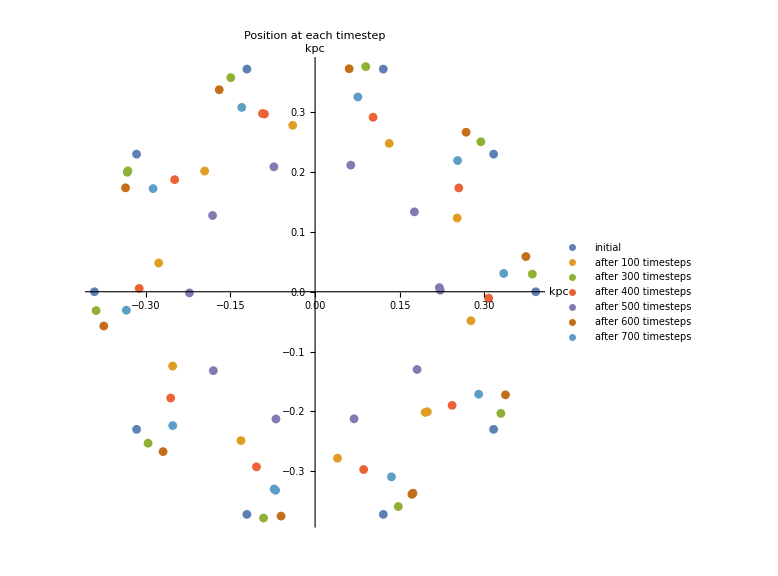

```mathematica
bp4posgraph = ListPlot[{bp4pos1,bp4pos100,bp4pos300,bp4pos400,bp4pos500,bp4pos600,bp4pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```

#### Comparing Position with run 1

```mathematica
diff = {}
g[a_,b_]:=(a - ((b * 38.3609 )/ (15) ))

For[j=1,j<11,j++,diff = Append[diff,g[bp1pos1[[j]],bp4pos1[[j]]]] ]
Print[diff]
```

{}

{{9.6336×10^-7,-1.16895×10^-6},{-5.08647×10^-7,7.80233×10^-7},{5.08647×10^-7,7.80233×10^-7},{-9.6336×10^-7,-1.16895×10^-6},{-3.8662×10^-7,3.84143×10^-22},{-9.6336×10^-7,1.16895×10^-6},{5.08647×10^-7,-7.80233×10^-7},{-5.08647×10^-7,-7.80233×10^-7},{9.6336×10^-7,1.16895×10^-6},{3.8662×10^-7,4.87453×10^-22}}

```mathematica
diff={}
For[j=1,j<11,j++,diff = Append[diff,g[bp1pos2[[j]],bp4pos2[[j]]]] ]
Print[diff]
```

{}

{{3.8662×10^-7,4.87453×10^-22},{-0.00370981,0.00519545},{-0.00605386,0.00202368},{-0.00608609,-0.00192238},{-0.00379358,-0.00513386},{-0.0000515345,-0.00638284},{0.00370981,-0.0051929},{0.00605386,-0.00202112},{0.00608609,0.00192238},{0.00379358,0.00513386}}

```mathematica
diff={}
For[j=1,j<11,j++,diff = Append[diff,g[bp1pos10[[j]],bp4pos10[[j]]]] ]
Print[diff]
```

{}

{{0.00423287,0.0573654},{-0.0332272,0.0546196},{-0.0589868,0.0246592},{-0.0622119,-0.0147272},{-0.041666,-0.0484868},{-0.00520468,-0.0637187},{0.0332503,-0.0546017},{0.0589945,-0.024631},{0.0622078,0.0147426},{0.0416711,0.0484842}}

#### Comparing Velocity with run 1

```mathematica
bp1vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10,9;;10}]
bp4vel1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10,9;;10}]
```

{{3.69316,-5.0832},{5.97566,-1.94161},{5.97566,1.94161},{3.69316,5.0832},{3.84734×10^-16,6.28319},{-3.69316,5.0832},{-5.97566,1.94161},{-5.97566,-1.94161},{-3.69316,-5.0832},{-1.1542×10^-15,-6.28319}}

{{110.644,-152.289},{179.026,-58.1691},{179.026,58.1691},{110.644,152.289},{1.15263×10^-14,188.239},{-110.644,152.289},{-179.026,58.1691},{-179.026,-58.1691},{-110.644,-152.289},{-3.4579×10^-14,-188.239}}

```mathematica
diff = {}
h[a_,b_]:=(a - ((b * 38.3609*(1.94249*10^16) )/ (15*(75.4212*10^9*yrsec)) ))

For[j=1,j<11,j++,diff = Append[diff,h[bp1vel1[[j]],bp4vel1[[j]]]] ]
Print[diff]
```

{}

{{1.38376,-1.90457},{2.23897,-0.727486},{2.23897,0.727486},{1.38376,1.90457},{1.44153×10^-16,2.3542},{-1.38376,1.90457},{-2.23897,0.727486},{-2.23897,-0.727486},{-1.38376,-1.90457},{-4.32456×10^-16,-2.3542}}

```mathematica
bp1magvel = 6.28319
bp4magvel = 301.029
h[bp1magvel,bp4magvel]
```

6.28319

301.029

0.0000152055

#### Converting Position from ChplUltra to dimensionless units

```mathematica
d[a_,b_]:=a - (b/0.391023)
pos={}
For[j=1,j<11,j++,pos = Append[pos,d[bp1pos200[[j]],bp4pos200[[j]]]] ]
Print[pos]
```

{}

{{1.57881,0.248705},{1.14413,1.12716},{0.264401,1.58442},{-0.717221,1.43619},{-1.42392,0.738822},{-1.58431,-0.241177},{-1.13761,-1.12714},{-0.25695,-1.58063},{0.721494,-1.43052},{1.42541,-0.735235}}

#### Comparing dot products

```mathematica
bp1dp1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10020,1}];
bp4dp1 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10020,1}];
```

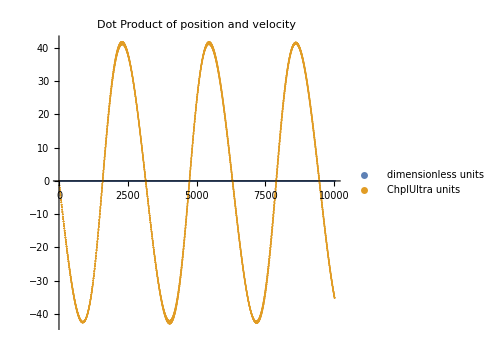

```mathematica
dp1graph = ListPlot[{bp1dp1,bp4dp1},PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"dimensionless units","ChplUltra units"}, PlotLabel->"Dot Product of position and velocity"]
```

```mathematica
bp1dp2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp1.csv",{"Data",1;;10020,2}];
bp4dp2 =  Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp4.csv",{"Data",1;;10020,2}];
```

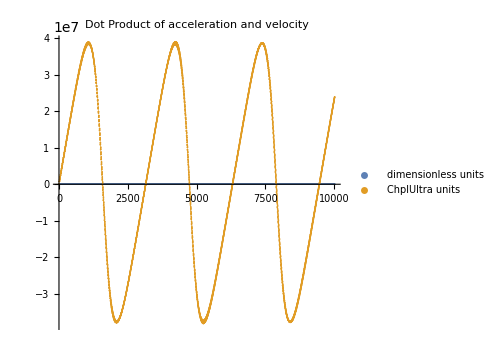

```mathematica
dp2graph = ListPlot[{bp1dp2,bp4dp2},PlotRange->Automatic,AspectRatio->1,ImageSize->Medium,PlotLegends->{"dimensionless units","ChplUltra units"}, PlotLabel->"Dot Product of acceleration and velocity"]
```

#### 5. ChplUltra units with 128 box, with initial velocity fixed NFW parameters = {417.0 km/s, 36.54 * kpckm, 90.0 * pi / 180, 1.0, 1.0, 1.0} (NO TRIAXIALITY) leapfrog with dimensionless units 10 test particles, 1000 timesteps of 1 Myr each r0 = 15 kpc box potential has units (128 by 128 by 128), ranges from (-20 kpc, 20 kpc)

#### Import Coordinates

```mathematica
bp5pos1 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1;;10,6;;7}];
bp5pos2 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",10;;20,6;;7}];
bp5pos10 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",100;;110,6;;7}];
bp5pos20 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",200;;210,6;;7}];
bp5pos30 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",300;;310,6;;7}];
bp5pos100 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",990;;1000,6;;7}];
bp5pos200 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",1990;;2000,6;;7}];
bp5pos300 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",2990;;3000,6;;7}];
bp5pos400 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",3990;;4000,6;;7}];
bp5pos500 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",4990;;5000,6;;7}];
bp5pos600 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",5990;;6000,6;;7}];
bp5pos700 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",6990;;7000,6;;7}];
bp5pos800 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",7990;;8000,6;;7}];
bp5pos900 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",8990;;9000,6;;7}];
bp5pos1000 = Import["/Users/clairerecamier/Desktop/Github/Streakline/TestingHDF5/mathematica/bp5.csv",{"Data",9990;;10000,6;;7}];
```

#### Position

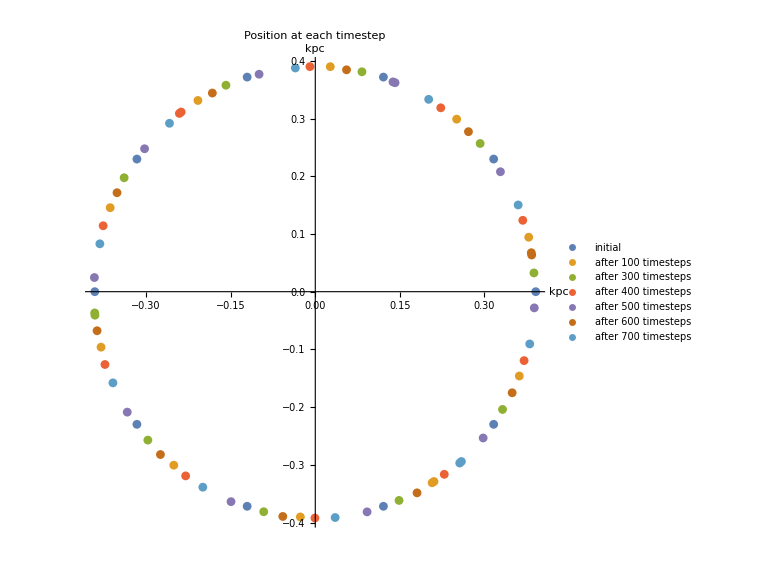

```mathematica
bp5posgraph = ListPlot[{bp5pos1,bp5pos100,bp5pos300,bp5pos400,bp5pos500,bp5pos600,bp5pos700},PlotRange->Automatic,AspectRatio->1,ImageSize->Large,PlotLegends->{"initial","after 100 timesteps","after 300 timesteps","after 400 timesteps","after 500 timesteps","after 600 timesteps","after 700 timesteps", "after 800 timesteps","after 900 timesteps","after 1000 timesteps"},AxesLabel->{"kpc","kpc"}, PlotLabel->"Position at each timestep"]
```